## functions

```mathematica
SwitchCounts[list_List]:=Module[{counts},counts=ConstantArray[0,Length[list]];
For[i=2,i<=Length[list],i++,If[list[[i]]===list[[i-1]],counts[[i]]=counts[[i-1]]+1,counts[[i]]=0];];
counts]
```

```mathematica
FindContiguousPositions[data_List,target_]:=Module[{positions={},startPos=None,endPos=None},Do[If[data[[i]]==target,If[startPos===None,startPos=i;];
endPos=i;,If[startPos=!=None,AppendTo[positions,{startPos,endPos}];
startPos=None;];];,{i,1,Length[data]}];
(*After the loop,check if there's an ongoing sequence*)If[startPos=!=None,AppendTo[positions,{startPos,endPos}];];
positions];
```

```mathematica
Off[InterpolatingFunction::dmval];
Off[InterpolatingFunction::dval];
Off[InterpolatingFunction::dmwarn];
Off[InterpolatingFunction::dzero];
```

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinuteString[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
MinuteOfDayToHourAndMinuteList[minuteOfDay_]:={IntegerPart[minuteOfDay/60],FractionalPart[minuteOfDay/60]60}
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
DateExtend[dateObject_,hour_,minute_]:=DateObject[Flatten[{DateList[dateObject][[1;;3]],{hour,minute}}]]
```

```mathematica
(*Function to normalize DateObjects to the same granularity*)
NormalizeDate[date_]:=DateObject[DateList[date][[1;;3]]]

(*Function to find the index of the first element not less than a given date*)
FindFirstIndexNotLessThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<normDate,low=mid+1,high=mid];];
low]

(*Function to find the index of the first element greater than a given date*)
FindFirstIndexGreaterThan[list_,date_]:=Module[{len=Length[list],low=1,high,mid,normDate},normDate=NormalizeDate[date];
high=len;
While[low<high,mid=Quotient[low+high,2];
If[NormalizeDate[First[list[[mid]]]]<=normDate,low=mid+1,high=mid];];
low]

(*Define the function to select elements by date range*)
SelectElementsByDateRange[list_,startDate_,endDate_]:=Module[{startIndex,endIndex,normStartDate,normEndDate},(*Normalize dates*)normStartDate=NormalizeDate[startDate];
normEndDate=NormalizeDate[endDate];
(*Find the starting and ending indices*)startIndex=FindFirstIndexNotLessThan[list,normStartDate];
endIndex=FindFirstIndexGreaterThan[list,normEndDate];
(*Return the sublist within the range*)list[[startIndex;;endIndex-1]]]
```

```mathematica
MapFunctionToGranularity[function_,data_List,granularity_String]:=Module[
{extractedComponents,groupedData,mappedData},
(*Extract the relevant component (e.g.,month) from each DateObject and pair with value*)extractedComponents=({DateValue[#[[1]],granularity],#[[2]]}&/@data);
(*Group data by the extracted component and calculate the mean for each group*)
groupedData=GroupBy[extractedComponents,First->Last];
(*Replace each group key with an average value*)
mappedData=function/@groupedData;
SortBy[Transpose[{Keys[mappedData],Values[mappedData]}],First]
]
```

```mathematica
dayNameToDayOfWeek={"Mon"->1,"Tue"->2,"Wed"->3,"Thu"->4,"Fri"->5,"Sat"->6,"Sun"->7};
```

```mathematica
RemoveOutliers[list_,sd_]:=Module[{mean,stdDev,lowerBound,upperBound},mean=Mean[list];
stdDev=StandardDeviation[list];
lowerBound=mean-sd stdDev;
upperBound=mean+sd stdDev;
Select[list,lowerBound<=#<=upperBound&]]
```

## misc

## heatmeter read-in

```mathematica
ToStringWithDateCorrection[expression_]:=If[
Length[StringSplit[ToString[expression],""]]==1,
"0"<>ToString[expression],
ToString[expression]
]
ToStringWithDateCorrection[expression_,correctLength_]:=If[
Length[StringSplit[ToString[expression],""]]<correctLength,
StringRiffle[ConstantArray["0",correctLength-Length[StringSplit[ToString[expression],""]]],""]<>ToString[expression],
ToString[expression]
]
```

```mathematica
MinuteOfDayToHourAndMinute[minuteOfDay_]:=ToStringWithDateCorrection[IntegerPart[minuteOfDay/60]]<>":"<>ToStringWithDateCorrection[FractionalPart[minuteOfDay/60]60]
```

```mathematica
HourAndMinuteToMinuteOfDay[hour_,minute_]:=60hour+minute
```

```mathematica
HourAndMinuteToMinuteOfDay[hourAndMinuteString_]:=If[
StringContainsQ[hourAndMinuteString,":"],
StringSplit[hourAndMinuteString,":"]//ToExpression[#[[1]]]60+ToExpression[#[[2]]]&,
ToExpression[StringTake[hourAndMinuteString,{1,2}]]60+ToExpression[StringTake[hourAndMinuteString,{3,4}]]
]
```

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
path=formattedDataRoot;
fileName="heat_stock_net.csv";
lastLoadDay=Module[
{dirs,sortedDirs,foundFile},
(*Get list of directories*)
dirs=FileNames["*",path];
(*Sort directories in decreasing order*)
sortedDirs=Sort[dirs,DateObject[#1]>DateObject[#2]&];
(*Search for the file*)
foundFile=SelectFirst[sortedDirs,FileExistsQ[FileNameJoin[{#,fileName}]]&];
StringSplit[foundFile,"\\"][[-1]]
];
loadDayStamps=Map[StringRiffle[Map[ToStringWithDateCorrection,#[[1;;3]]],"-"]&,DateRange[{2024,2,1},DateObject[lastLoadDay]]];
heatStockDataOriginal=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
heatStockDataNet=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
loadDayStamps]]/.{$Failed->"no data"};
badDays=Flatten[Intersection[Flatten[Position[heatStockDataOriginal,$Failed]],Flatten[Position[heatStockDataNet,$Failed]]]];
goodDays=Complement[Range[Length[loadDayStamps]],badDays];
Manipulate[
Module[
{dayN,timeStamps},
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=Map[
HourAndMinuteToMinuteOfDay[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
];
Grid[{
{"day","original","net","diff"},
{
loadDayStamps[[dayN]],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]],"no data"],
If[Dimensions[heatStockDataOriginal[[dayN]]]!={}&&Dimensions[heatStockDataNet[[dayN]]]!={},heatStockDataNet[[dayN]][[-1]][[2;;5]]-heatStockDataOriginal[[dayN]][[-1]][[2;;5]],"no data"]
},
Table[ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Nothing]
},
Joined->True,PlotRange->All,Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.25]}&,Range[0,24 60, 120]],Automatic},ImageSize->250,PlotLabel->"cycle "<>ToString[cycle],Prolog->{If[showCaptures,{Pink,Thin,Map[Line[{{#,0},{#,10000}}]&,timeStamps]}]}
],{cycle,1,4}]
}]
],
{showCaptures,{False,True}},
{{day,loadDayStamps[[goodDays]][[-1]]},loadDayStamps[[goodDays]]}
]
```

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringJoin::string: String expected at position 1 in rawDataRoot<>\2024-03-29\heatmeter_images\.

StringJoin::string: String expected at position 1 in rawDataRoot<>\\2024-03-29\\heatmeter_images\\.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part -1 of Symbol[] does not exist.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

Part::partw: Part -1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 5 in Symbol[]⟦-1⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

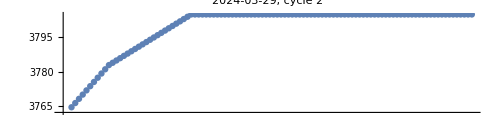
-Graphics-
1500 | 1510 | 1520 | 1530 | 1540 | 1550 | 1600 | 1610 | 1620 | 1630 | 1640 | 1650 | 1700 | 1710 | 1720 | 1730 | 1740 | 1750 | 1800 | 1810 | 1820 | 1830 | 1840 | 1850 | 1900 | 1910 | 1920 | 1930 | 1940 | 1950 | 2000 | 2010 | 2020 | 2030 | 2040 | 2050 | 2100 | 2110 | 2120 | 2130 | 2140 | 2150 | 2200 | 2210 | 2220 | 2230 | 2240 | 2250 | 2300 | 2310 | 2320 | 2330 | 2340 | 2350
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
cycle=2;timeSpan={15,24}100;
day=loadDayStamps[[goodDays]][[-1]];
dayN=Position[loadDayStamps,day][[1]][[1]];
timeStamps=DeleteDuplicates[Map[
ToExpression[StringTake[#,{-10,-7}]]&,
Select[FileNames[All,rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"],StringEndsQ[#,".png"]&]
]];
cycleImagesForTimeSpan=Map[
Import[rawDataRoot<>"\\"<>day<>"\\heatmeter_images\\"<>ToStringWithDateCorrection[#,4]<>"_"<>ToString[cycle]<>".png"]
&,Select[timeStamps,Between[#,timeSpan]&]];
{
ListPlot[
{
If[Dimensions[heatStockDataOriginal[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataOriginal[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing],
If[Dimensions[heatStockDataNet[[dayN]]]!={},Select[Transpose[Transpose[heatStockDataNet[[dayN]]][[{1,1+cycle}]]],Between[#[[1]],Map[HourAndMinuteToMinuteOfDay,Map[ToStringWithDateCorrection[#,4]&,timeSpan]]]&],Nothing]
},
Ticks->{Map[{#,Rotate[MinuteOfDayToHourAndMinute[#],Pi 0.5]}&,Range[0,24 60, 10]],Automatic},ImageSize->500,AspectRatio->0.25,PlotLabel->day<>", cycle "<>ToString[cycle]
],
{Select[timeStamps,Between[#,timeSpan]&],cycleImagesForTimeSpan}//Grid
}//Column
```

```mathematica
heatFlowDataOriginal=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow.csv"]&,
loadDayStamps];
```

```mathematica
heatFlowDataNet=Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_flow_net.csv"]&,
loadDayStamps];
```

```mathematica
Table[
Table[
ListPlot[
{
Transpose[Transpose[heatFlowDataOriginal[[day]]][[{1,1+cycle}]]],
Transpose[Transpose[heatFlowDataNet[[day]]][[{1,1+cycle}]]]
},
Joined->True,PlotRange->All
]
,{cycle,1,4}]
,{day,goodDays}]//Grid
```

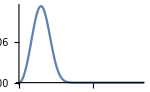
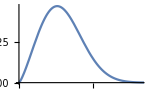
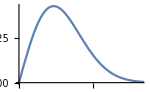
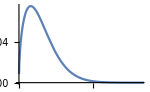

```mathematica
weibullParameters={
{3,10.3,0.001},
{2.3,20,0.001},
{2,20,0.001},
{1.5,10,0.001}
};
Table[Plot[
PDF[WeibullDistribution[weibullParameters[[cycle]][[1]],weibullParameters[[cycle]][[2]],weibullParameters[[cycle]][[3]]],power],{power,0,100},PlotRange->{{0,50},All},ImageSize->150
],{cycle,1,4}]//Row
```

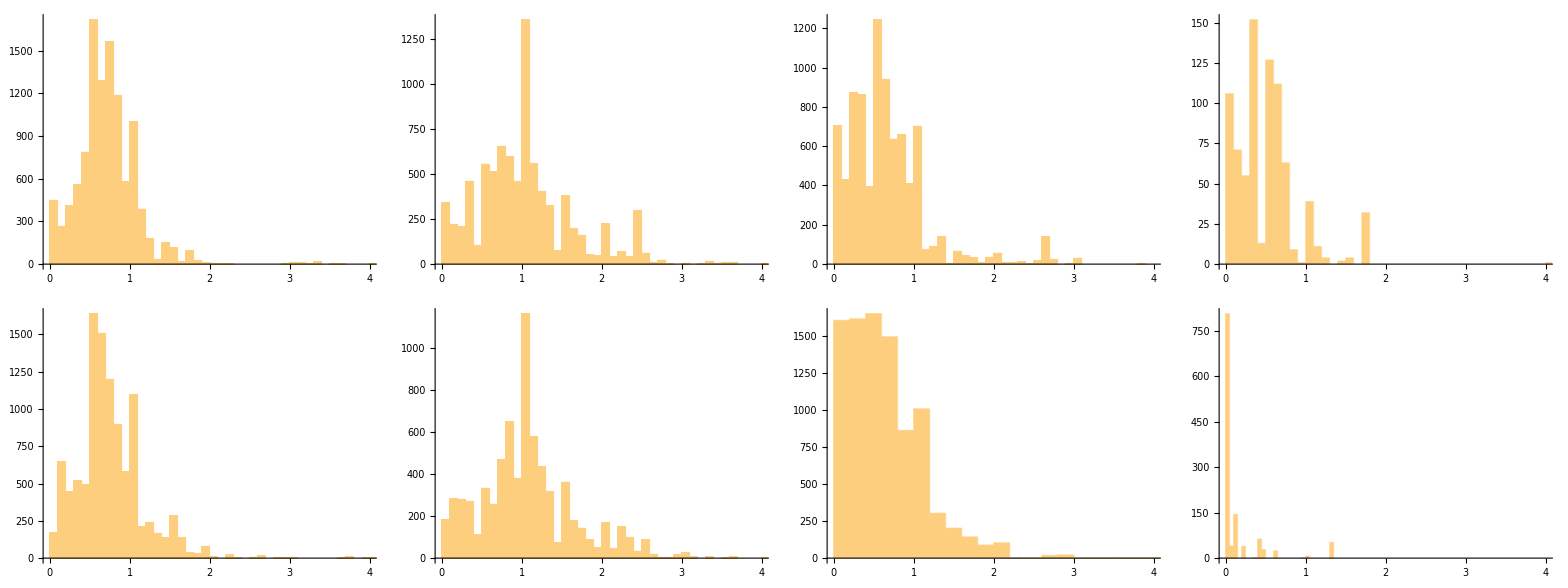

```mathematica
{
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataOriginal[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}],
Table[
Histogram[
Select[Flatten[Table[
Differences[Transpose[heatStockDataNet[[dayN]]][[1+cycle]]]
,{dayN,goodDays}]],0.01<#<100&],PlotRange->{{0,4},All}
],{cycle,1,4}]
}//Grid
```

## adatok

```mathematica
rawDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\raw";
```

```mathematica
formattedDataRoot="C:\\Users\\Beno\\Documents\\SZAKI\\dev\\kazankontroll-dashboard\\data\\formatted";
```

```mathematica
seasonDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

## hő

```mathematica
heatDataDays=Map[DateObject,DateRange[{2023,11,22},{2024,3,29}]];
```

```mathematica
heatStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heat_stock_net.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatDataDays]]];
```

```mathematica
heatStockDated=Map[Flatten[#,1]&,Transpose[Table[
Module[
{dayDateList},
dayDateList=DateList[heatDataDays[[dayN]]];
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatStockLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],heatStockLine[[2;;5]]}]
,{heatStockLine,heatStockPre[[dayN]]}]]
]
,{dayN,1,Length[heatDataDays]}]]];
(*1-es kör átfordulás: jan 20-21*)
(*2-es kör átfordulás: feb 4-5*)
```

```mathematica
cycle=2;
Map[
SortBy[heatStock[[cycle]][[#[[1]];;#[[1]]+1]],First]&,
Map[Position[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#][[1]]&,Select[Differences[Transpose[heatStockDated[[cycle]]][[2]]],#<-10&]]
]
```

{{{Thu 14 Dec 2023 23:55:00GMT+2,4247},{Fri 15 Dec 2023 00:00:00GMT+2,4228.81}},{{Sun 4 Feb 2024 23:55:00GMT+2,9937},{Mon 5 Feb 2024 00:00:00GMT+2,125.}}}

```mathematica
heatStockDated[[1]]=Map[
If[
DateObject[{2024,1,20,23,59}]<#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[1]]];
```

```mathematica
heatStockDated[[2]]=Quiet[Map[
If[
DateObject[{2024,2,4,23,59}]<=#[[1]],
{#[[1]],#[[2]]+10000},
#
]
&,heatStockDated[[2]]]];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDated.mx",heatStock];
```

```mathematica
heatStockSeason=Table[
Transpose[{
Transpose[heatStockDated[[cycle]]][[1]],
Transpose[heatStockDated[[cycle]]][[2]]-heatStockDated[[cycle]][[1]][[2]]
}],{cycle,1,4}];
```

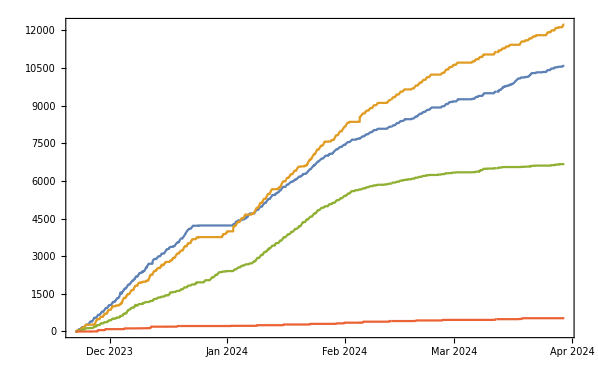

```mathematica
DateListPlot[heatStockSeason]
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockSeason.mx",heatStockSeason];
```

```mathematica
heatStockSeason=Import[NotebookDirectory[]<>"\\heatStockSeason.mx"];
```

```mathematica
heatStockDaily=Table[Table[
Module[
{dailyCumulative},
dailyCumulative=SelectElementsByDateRange[heatStockSeason[[cycle]],DateExtend[day,0,0],DateExtend[day,23,59]];
If[
dailyCumulative!={},
Transpose[{
Transpose[dailyCumulative][[1]],
Transpose[dailyCumulative][[2]]-dailyCumulative[[1]][[2]]
}],
None]
]
,{day,seasonDays}],{cycle,1,4}];
```

```mathematica
Export[NotebookDirectory[]<>"\\heatStockDaily.mx",heatStockDaily];
```

```mathematica
heatStockDaily=Import[NotebookDirectory[]<>"\\heatStockDaily.mx"];
```

## gáz

```mathematica
gasDataDays=Map[DateObject,Join[
DateRange[{2023,11,23},{2023,12,6}],
DateRange[{2023,12,15},{2024,5,16}]
]];
```

```mathematica
gasStockPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\gas_stock.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,gasDataDays]]];
```

```mathematica
gasStockDaily=Table[
If[
MemberQ[gasDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[gasDataDays,day][[1]][[1]];
dayDateList=DateList[gasDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[gasStockLine[[1]]];
Transpose[{DateObject[dayDateList],gasStockLine[[2]]}]
,{gasStockLine,gasStockPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\gasStockDaily.mx",gasStockDaily];
```

```mathematica
gasStockDaily=Import[NotebookDirectory[]<>"\\gasStockDaily.mx"];
```

```mathematica
gasStock2023Monthly={{DateObject[{2022,11,30}],34363-7 50},{DateObject[{2022,12,30},"Day","Gregorian",2.],35355},{DateObject[{2023,1,31},"Day","Gregorian",2.],36583},{DateObject[{2023,2,28},"Day","Gregorian",2.],37878},{DateObject[{2023,3,31},"Day","Gregorian",2.],38842},{DateObject[{2023,4,21},"Day","Gregorian",2.],39277}};
```

```mathematica
Map[
Total[#[[All,2]]]&,
GatherBy[
Map[If[Length[#]>0,#[[-1]],Nothing]&,gasStockDaily],
#[[1]][[1]][[2]]&
]
]
```

{378.3,1116.2,1489.7,910.4,826.6,435.1,144.3}

```mathematica
gasBillMonthly={
{0,1,2022,11,555148,None,None},
{0,2,2022,12,1349784,1342,1000},
{0,3,2023,1,732472,1228,567},
{0,4,2023,2,712951,1295,550},
{0,5,2023,3,487518,964,505},
{0,6,2023,4,246102,435,565},
{1,1,2023,11,531400,None,None},
{1,2,2023,12,519340,1116,465},
{1,3,2024,1,575200,1490,386},
{1,4,2024,2,312511,910,343},
{1,5,2024,3,267658,827,323},
{1,6,2024,4,147366,435,338}
};
```

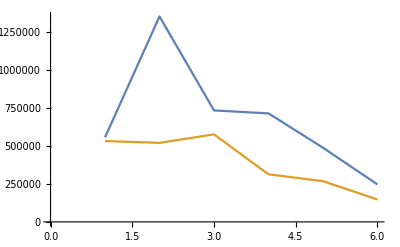

```mathematica
ListPlot[
Map[
#[[All,{2,5}]]&,
GatherBy[gasBillMonthly,First]
],Joined->True
]
```

```mathematica
gasStock2223=Map[
If[
NumberQ[#[[2]]],
{DateObject[#[[1]]],#[[2]]},
Nothing
]&
,Import[NotebookDirectory[]<>"gas_202223.csv"]
];
```

```mathematica
gasFlow2223DailyTotals=

Transpose[{Drop[gasStock2223[[All,1]],1],Differences[gasStock2223[[All,2]]]/(Differences[Map[UnixTime,gasStock2223[[All,1]]]]/(60 60 24))}];
```

```mathematica
gasFlowDailyTotals=Map[
If[
Length[#]!=0,
#[[-1]],
Nothing
]&,
gasStockDaily];
```

```mathematica
monthLengths={31,28,31,30,31,30,31,31,30,31,30,31};
```

```mathematica
calendarMonthToSeasonMonth={3,4,5,6,0,0,0,0,0,0,1,2};
seasonMonthToCalendarMonth={11,12,1,2,3,4};
seasonMonthNames={"Nov","Dec","Jan","Feb","Márc","Ápr"};
```

```mathematica
CalendarDayToSeasonDay[calendarDay_]:=
Total[monthLengths[[Range[1,calendarMonthToSeasonMonth[[calendarDay[[1]][[2]]]]-1]]]]+calendarDay[[1]][[3]]
```

## szobák hőmérséklete

```mathematica
roomTempDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
roomTempsPre=Table[Quiet[
Map[
Import[formattedDataRoot<>"\\"<>#<>"\\room_"<>ToString[room]<>"_temps.csv"]
&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,roomTempDataDays]]
],{room,1,10}];
```

```mathematica
roomTempsDaily=Table[Table[
If[
MemberQ[roomTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[roomTempDataDays,day][[1]][[1]];
dayDateList=DateList[roomTempDataDays[[dayN]]];
If[
Dimensions[roomTempsPre[[room]][[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[roomTempLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],4],roomTempLine[[2;;5]]}]
,{roomTempLine,roomTempsPre[[room]][[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}],{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"\\roomTempsDaily.mx",roomTempsDaily];
```

```mathematica
roomTempsDaily=Import[NotebookDirectory[]<>"\\roomTempsDaily.mx"];
```

```mathematica
setTempLowForAtLeastOneRoomDaily=Transpose[
{roomTempDataDays,
Quiet[Map[
Min[#]<0&,
Transpose[Table[
Table[
Min[Select[Transpose[roomTemp[[1]]][[2]]-Transpose[roomTemp[[2]]][[2]],NumberQ]]
,{roomTemp,roomTempsDaily[[room]]}]
,{room,1,10}]]
]]
}];
```

## fűtési állapot

```mathematica
heatingStateDataDays=Map[DateObject,DateRange[{2023,11,8},{2024,5,16}]];
```

```mathematica
heatingStatePre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\heating_state.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,heatingStateDataDays]]];
```

```mathematica
heatingStateDaily=Table[
If[
MemberQ[heatingStateDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[heatingStateDataDays,day][[1]][[1]];
dayDateList=DateList[heatingStateDataDays[[dayN]]];
If[
Dimensions[heatingStatePre[[dayN]]]!={},
Transpose[Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[heatingStateLine[[1]]];
Transpose[{ConstantArray[DateObject[dayDateList],5],heatingStateLine[[2;;6]]}]
,{heatingStateLine,heatingStatePre[[dayN]]}]],
None
]
],
None
]
,{day,seasonDays}];
```

```mathematica
Position[heatingStateDaily,None]
```

{{56},{57},{96},{97},{110},{111},{119},{120},{138},{145},{146},{152},{153},{154},{157},{158},{159},{160},{161},{162},{163},{167},{168},{173},{174},{175},{179},{180},{181},{182},{183},{184},{185},{186},{187},{188},{189},{190},{191},{192}}

```mathematica
heatingStateNoDataDays=heatingStateDataDays[[Flatten[Position[heatingStatePre,$Failed]]]];
```

```mathematica
noHeatingDays=Transpose[Select[setTempLowForAtLeastOneRoomDaily,#[[2]]==False&]][[1]];
```

```mathematica
Table[
Module[
{dayDateList,minutes,blankDayData,dayPosition},
dayDateList=DateList[day];
minutes=Map[
DateObject[Join [dayDateList[[1;;3]],MinuteOfDayToHourAndMinuteList[#]]]&
,Transpose[heatingStatePre[[1]]][[1]]];
blankDayData=ConstantArray[
Transpose[
{
minutes,
ConstantArray[0,288]
}
],5];
dayPosition=Position[seasonDays,day][[1]][[1]];
heatingStateDaily[[dayPosition]]=blankDayData;
]
,{day,Intersection[heatingStateNoDataDays,noHeatingDays]}]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Position[heatingStateDaily,None]
```

{{95},{96},{109},{110},{153},{162},{166},{167},{172},{174}}

```mathematica
Export[NotebookDirectory[]<>"\\heatingStateDaily.mx",heatingStateDaily];
```

```mathematica
heatingStateDaily=Import[NotebookDirectory[]<>"\\heatingStateDaily.mx"];
```

## egyéb

### külső hőmérséklet

```mathematica
externalTempDataDays=Complement[Map[DateObject,DateRange[{2023,11,22},{2024,5,16}]]];
```

```mathematica
externalTempPre=Quiet[Map[
Import[formattedDataRoot<>"\\"<>#<>"\\external_temp.csv"]&,
Map[StringRiffle[Map[ToStringWithDateCorrection,DateList[#][[1;;3]]],"-"]&,externalTempDataDays]]];
```

```mathematica
externalTempDaily=Table[
If[
MemberQ[externalTempDataDays,day],
Module[
{dayN,dayDateList},
dayN=Position[externalTempDataDays,day][[1]][[1]];
dayDateList=DateList[externalTempDataDays[[dayN]]];
Table[
dayDateList[[{4,5}]]=MinuteOfDayToHourAndMinuteList[externalTempLine[[1]]];
Transpose[{DateObject[dayDateList],externalTempLine[[2]]}]
,{externalTempLine,externalTempPre[[dayN]]}]
],
None
]
,{day,seasonDays}];
```

```mathematica
Export[NotebookDirectory[]<>"\\externalTempDaily.mx",externalTempDaily];
```

```mathematica
externalTempDaily=Import[NotebookDirectory[]<>"\\externalTempDaily.mx"];
```

### környezeti változók

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
gasPricePerCubicMeter=700;
```

```mathematica
airSpecificMass=1.2;(*kg/m3*)
```

```mathematica
airSpecificHeatCapacity=1012;(*J/kg/K*)
```

```mathematica
roomNames={"ovi","PK","SZGK","Gólyairoda","Mérce","vendégtér","kisterem","trafóház","Oktopusz","Lahmacun","Kazán közös terek","műhely"};
```

```mathematica
roomsWithTempData={1,2,3,4,5,6,7,9,10};
```

```mathematica
roomToCycle={1,1,2,2,2,3,3,4,1,2};
roomsByCycle=Table[Flatten[Position[roomToCycle,cycle]],{cycle,1,4}];
```

```mathematica
roomAreas={53,26,29,26.5,72,100,60.25,240,66,24,50,26.5} ;
```

```mathematica
roomExternalWallLength={9.8,4.8,5.4,6,10.2,15.4,10.2,25,9,5.2,None,2.5} ;
roomInternalWallLength={18.5,14.9,15.6,8.3,23,20.4,0,0,21,14.2};
```

```mathematica
roomHeight=3.2;
```

```mathematica
radiatorHeight=0.6;
roomRadiatorLength={4 140,280,300,180,540+150,6 120,4 120,0,2 140,100}/100;
```

```mathematica
heatingWaterMax=65;
heatingWaterMin=45;
```

```mathematica
roomColors={Black,Red,Green,Blue,Orange,Purple,Pink,Darker[Yellow],Magenta,Darker[Cyan]};
```

## elemzés

## jegyzetek

úgy érdemes tekinteni, mint egy cél felé hajtott rendszert

kontrollváltozók:
	- fő kontrollváltozók: fogyasztott gáz és kiküldött hő
		> korrellált kontrollváltozók: fűtési állapot
	- nem irányított kontrollváltozó: kinti hőmérséklet, besugárzás
függő változók: szobák hőmérséklete

hibajel: beállított hőmérséklet - aktuális hőmérséklet

fő kérdések:
- milyen költséggel milyen mértékben lehet csökkenteni a hibát?
- hogy teljesít a rendszer, lehet-e jellemezni valahogy?
- külső körülmények hogyan befolyásolják?
- van-e olyan szcenárió, amivel jelentősen jobban teljesítene?
- lehet-e jellemezni a szobákat?
- hogyan viszonyul a tavalyi adatokhoz?

- pontosítani a szobák hőtechnikai jellemzőit (homennyisegbol becsülni? figyelembe venni aktuális hőmérsékletet hokapacitashoz? fűtővíz hőmérséklete?)
- karakterizalni, h milyen költsége van  egy szoba felfutesenek adott külső hőmérséklet mellett 
- jellemezni a szitut költség - komfort síkon, akár szezonon belül is
- modellezni, hogy szabályozás vagy beavatkozás mennyit tol a síkon milyen irányba

## gázból hő

### gázfogyasztás és gázár

```mathematica
gasBillMonthly
```

{{0,1,2022,11,555148,None,None},{0,2,2022,12,1349784,1342,1000},{0,3,2023,1,732472,1228,567},{0,4,2023,2,712951,1295,550},{0,5,2023,3,487518,964,505},{0,6,2023,4,246102,435,565},{1,1,2023,11,531400,None,None},{1,2,2023,12,519340,1116,465},{1,3,2024,1,575200,1490,386},{1,4,2024,2,312511,910,343},{1,5,2024,3,267658,827,323},{1,6,2024,4,147366,435,338}}

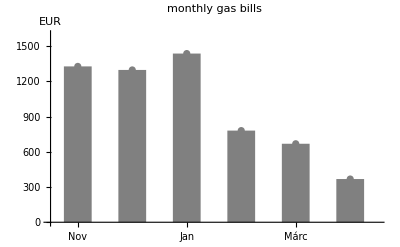

```mathematica
plot=ListPlot[
Map[
{
calendarMonthToSeasonMonth[[#[[4]]]],
#[[5]]/400
}&,
Select[gasBillMonthly,#[[1]]==1&]
],Joined->False,PlotStyle->{Gray},Filling->Axis,Axes->{True,True},FillingStyle->{Black,Thickness[0.05]},PlotRange->{{0.5,6.5},{0,1600}},Ticks->{Transpose[{Range[6],seasonMonthNames}],Automatic},PlotLabel->"monthly gas bills",ImageSize->400,AxesLabel->{None,"EUR"}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\monthly_gas_bills.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\monthly_gas_bills.png

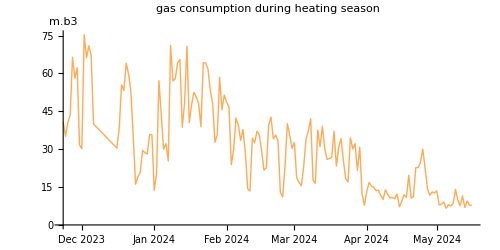

```mathematica
plot=DateListPlot[{
Select[Map[{#[[1]][[1]],#[[-1]][[2]]}&,DeleteCases[gasStockDaily,None]],#[[2]]<150&]
},Joined->True,PlotRange->All,PlotStyle->{{Thick,Lighter[Orange]},{Thick,Darker[Pink]}},ImageSize->500,
PlotLabel->"gas consumption during heating season",AxesLabel->{None,"m.b3"},Axes->{True,True},Frame->False,AspectRatio->0.5
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\gas_consumption_2324.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\gas_consumption_2324.png

### nem fűtésre elmenő gáz becslése

```mathematica
daysWithMissingGasStockData=Flatten[Position[gasStockDaily,None]];
daysWithMissingHeatingStateData=Flatten[Position[heatingStateDaily,None]];
```

```mathematica
gasStockAndHeatingState=Flatten[Table[
Transpose[{
Drop[Map[#[[1]][[4]]60+#[[1]][[5]]&,gasStockDaily[[day]][[All,1]]],1],
Differences[gasStockDaily[[day]][[All,2]]],
Drop[heatingStateDaily[[day]][[1]][[All,2]],1],
Drop[SwitchCounts[heatingStateDaily[[day]][[1]][[All,2]]],1]
}]
,{day,Complement[Range[Length[seasonDays]],Flatten[{daysWithMissingGasStockData,daysWithMissingHeatingStateData}]]}],1];
```

```mathematica
gasFlowByHeatingStateByMinuteOfDay=Table[
Transpose[Map[Flatten[{
#[[1]][[1]],
GetMeanAndSEM[#[[All,2]]]
}]&,GatherBy[SortBy[Select[gasStockAndHeatingState,#[[3]]==heatingOnOrOff&],First],First]]]
,{heatingOnOrOff,{0,1}}];
```

```mathematica
NonHeatingGasRatioInterpolation[minOfDay_]:=Interpolation[
Transpose[{
MovingAverage[Transpose[gasFlowByHeatingStateByMinuteOfDay[[1]][[1]]],240/5],
MovingAverage[Transpose[gasFlowByHeatingStateByMinuteOfDay[[1]][[2]]],240/5]/MovingAverage[Transpose[gasFlowByHeatingStateByMinuteOfDay[[2]][[2]]],240/5]
}],InterpolationOrder->1
][minOfDay]
HeatingGasRatioInterpolation[minOfDay_]:=1-NonHeatingGasRatioInterpolation[minOfDay]
```

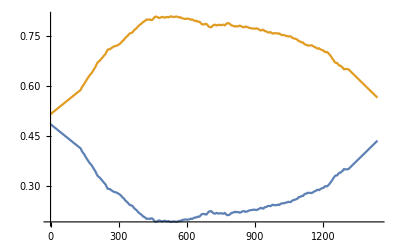

```mathematica
Plot[
{
NonHeatingGasRatioInterpolation[x],
HeatingGasRatioInterpolation[x]
},
{x,0,24 60}
]
```

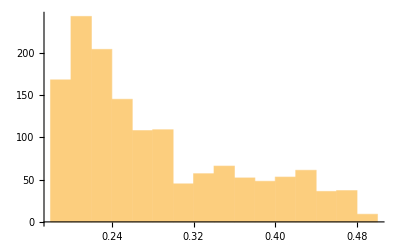

```mathematica
Histogram[NonHeatingGasRatioInterpolation[Range[0,24 60,1]]]
```

```mathematica
Mean[NonHeatingGasRatioInterpolation[Range[0,24 60,1]]]
```

0.282479

```mathematica
nonHeatingGasRatio=0.28247875662234045;
heatingGasRatio=1-nonHeatingGasRatio;
```

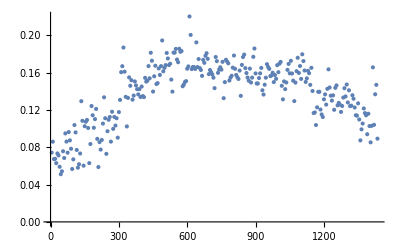

```mathematica
ListPlot[
Map[
{
#[[1]],
(1-NonHeatingGasRatioInterpolation[#[[1]]])#[[2]]
}
&,Transpose[gasFlowByHeatingStateByMinuteOfDay[[2]]]
]
]
```

```mathematica
gasFlowByHeatingStateByMinuteOfDay=Join[
gasFlowByHeatingStateByMinuteOfDay,
{Transpose[Map[
{
#[[1]],
(1-NonHeatingGasRatioInterpolation[#[[1]]])#[[2]],
(1-NonHeatingGasRatioInterpolation[#[[1]]])#[[3]]
}
&,Transpose[gasFlowByHeatingStateByMinuteOfDay[[2]]]
]]}
];
```

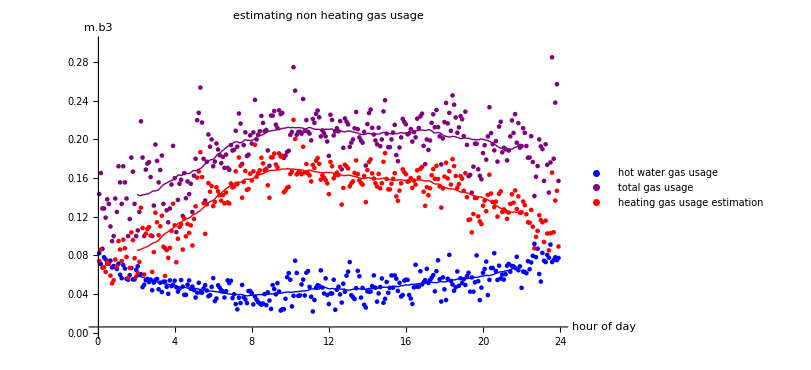

```mathematica
plotState=3;
plot=ErrorListPlot[
gasFlowByHeatingStateByMinuteOfDay[[1;;plotState]],
{Blue,Purple,Red},
{
PlotLabel->"estimating non heating gas usage",ImageSize->600,AxesLabel->{"hour of day","m.b3"},PlotRange->{All,{0,0.3}},PlotLegends->Placed[
{
{"mean gas usage when heating is off","hot water gas usage"}[[plotState-1]],
{"when heating is on","total gas usage"}[[plotState-1]],
{"","heating gas usage estimation"}[[plotState-1]]
},Bottom],
Epilog->{
Thickness->0.01,
Table[{
{Blue,Purple,Red}[[measure]],
Line[MovingAverage[Transpose[gasFlowByHeatingStateByMinuteOfDay[[measure]][[{1,2}]]],240/5]]
}
,{measure,1,plotState}]
},
Ticks->{Map[{# 60, #}&,Range[0,24]],Automatic}
},
{False,False,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\heating_gas_estimation_2.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\heating_gas_estimation_2.png

```mathematica
nonHeatingRatioOfGasFlow=Transpose[{
gasFlowByHeatingStateByMinuteOfDay[[1]][[1]],
gasFlowByHeatingStateByMinuteOfDay[[1]][[2]]/gasFlowByHeatingStateByMinuteOfDay[[2]][[2]]
}];
```

```mathematica
nonHeatingGasRatio=EstimateMode[Select[nonHeatingRatioOfGasFlow,4 60<#[[1]]<20 60&][[All,2]]];
```

```mathematica
nonHeatingGasRatio=0.1980919308726855;
heatingGasRatio=1-nonHeatingGasRatio;
```

### kazánok hatékonyságának becslése

```mathematica
daysWithMissingGasStockData=Flatten[Position[gasStockDaily,None]];
daysWithMissingHeatStockData=DeleteDuplicates[Flatten[Table[Position[heatStockDaily[[cycle]],None],{cycle,1,4}]]];
```

```mathematica
gasStockAndHeatOutput=Select[Table[
Transpose[{
seasonDays[[day]],
Total[Differences[gasStockDaily[[day]][[All,2]]]HeatingGasRatioInterpolation[Range[5,24 60-5,5]]]energyContentInGasPerCubicMeter,
Total[Table[heatStockDaily[[cycle]][[day]][[-1]][[2]],{cycle,1,4}]]
}]
,{day,Complement[Range[Length[seasonDays]],Flatten[{daysWithMissingGasStockData,daysWithMissingHeatStockData}]]}],
#[[2]]<600&
];
```

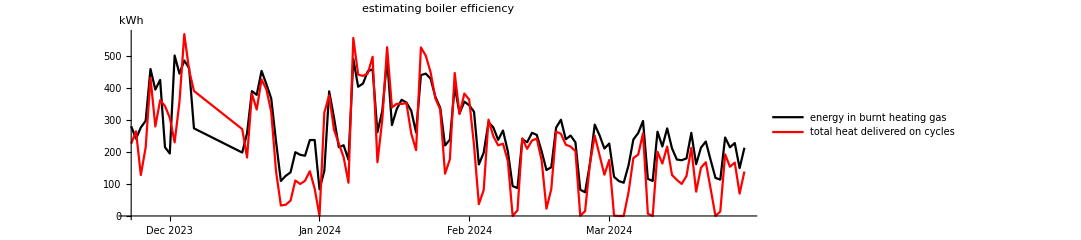

```mathematica
plot=DateListPlot[
{
gasStockAndHeatOutput[[All,{1,2}]],
gasStockAndHeatOutput[[All,{1,3}]]
},PlotStyle->{Black,Red},PlotLegends->Placed[{"energy in burnt heating gas","total heat delivered on cycles"},Bottom],ImageSize->800,AspectRatio->0.3,
PlotLabel->"estimating boiler efficiency",AxesLabel->{None,"kWh"},Axes->{True,True},Frame->False
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\boiler_efficiency_estimation.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\boiler_efficiency_estimation.png

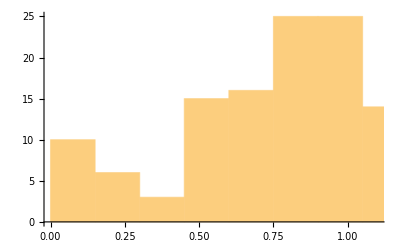

```mathematica
Histogram[gasStockAndHeatOutput[[All,3]]/gasStockAndHeatOutput[[All,2]],{0.15},PlotRange->{{0,1.1},All}]
```

```mathematica
boilerEfficiencyEstimate=EstimateMode[Select[gasStockAndHeatOutput[[All,3]]/gasStockAndHeatOutput[[All,2]],0.6<#<1.2&]]
```

```mathematica
boilerEfficiencyEstimate=0.9308950499052587;
```

## szobák hődinamikája

```mathematica
HeatingCurve[externalTemp_,maxTemp_,minTemp_]:=Module[{supplyTemp},(*Define the relationship between external temperature and supply water temperature*)supplyTemp=If[externalTemp<=-10,maxTemp,If[externalTemp>=20,minTemp,maxTemp-(maxTemp-minTemp)/(20+10)(externalTemp+10)]];
supplyTemp]
```

### hőkarakterisztikák becslése

#### jól jellemző hőmérsékletváltozási periódusok összegyűjtése

```mathematica
minDuration=60;(*min*)
minTempChange=1;(*K*)
minTempChangeIntensity=0.5;(*K/h*)
CheckPeriodForCharacteristics[periodData_]:=Module[
{periodTimeVector,periodTempVector},
periodTimeVector=Transpose[periodData][[1]];
periodTempVector=Transpose[periodData][[2]];
minDuration<periodTimeVector[[-1]]-periodTimeVector[[1]]&&
minTempChange<Abs[periodTempVector[[-1]]-periodTempVector[[1]]]&&
minTempChangeIntensity<Max[Abs[Differences[periodTempVector]/(Differences[periodTimeVector]/60)]]
]
```

```mathematica
maxDiscontiguityInTime=60;(*120*)
wellBehavedTemperatureChangePeriodsForRooms=Table[
If[
room!=8,
Module[
{
unifiedTempDataForRoom,timeVector,
decreaseIncreaseSigned,decreaseIncreaseSwitches,decreaseIncreasePeriods,coolingPeriods,warmingPeriods
},
unifiedTempDataForRoom=Select[Flatten[Table[
If[
Length[roomTempsDaily[[room]][[dayN]]]!=0&&Length[externalTempDaily[[dayN]]]!=0&&Length[heatingStateDaily[[dayN]]]!=0,
Transpose[{
(dayN-1)24 60+Range[5,24 60,5],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Transpose[externalTempDaily[[dayN]]][[2]],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]]
}],
Nothing
],{dayN,1,Length[seasonDays]}],1],NumberQ[#[[2]]]&];
timeVector=Transpose[unifiedTempDataForRoom][[1]];
decreaseIncreaseSigned=Select[Transpose[{
Drop[Transpose[unifiedTempDataForRoom][[1]],1],
Sign[Differences[Transpose[unifiedTempDataForRoom][[2]]]]
}],MemberQ[{-1,1},#[[2]]]&];
decreaseIncreaseSwitches=Flatten[Map[
Position[timeVector,#]
&,Transpose[Select[Transpose[{
Drop[Transpose[decreaseIncreaseSigned][[1]],1],
Differences[Transpose[decreaseIncreaseSigned][[2]]]
}],Abs[#[[2]]]==2&]][[1]]
]];
decreaseIncreasePeriods=Transpose[{decreaseIncreaseSwitches,RotateLeft[decreaseIncreaseSwitches,1]-1}][[2;;-2]];
coolingPeriods={};warmingPeriods={};
Table[
If[
unifiedTempDataForRoom[[period[[2]]]][[2]]-unifiedTempDataForRoom[[period[[1]]]][[2]]<0,
coolingPeriods=If[Length[coolingPeriods]==0,coolingPeriods={period},Join[coolingPeriods,{period}]],
warmingPeriods=If[Length[warmingPeriods]==0,warmingPeriods={period},Join[warmingPeriods,{period}]]
]
,{period,decreaseIncreasePeriods}];
{coolingPeriods,warmingPeriods}=Table[
Select[Flatten[Table[
Module[
{periodTimeVector,discontiguityPositions,discontiguityBoundaries,newPeriods},
periodTimeVector=Transpose[unifiedTempDataForRoom[[period[[1]];;period[[2]]]]][[1]];
discontiguityPositions=Flatten[Position[Sign[Floor[Differences[periodTimeVector]/maxDiscontiguityInTime]],1]];newPeriods=If[
Length[discontiguityPositions]!=0,
discontiguityBoundaries=Join[
{{1,discontiguityPositions[[1]]}},
1+Transpose[{
discontiguityPositions,
Join[Drop[RotateLeft[discontiguityPositions],-1],{Length[periodTimeVector]-1}]
}]
];
period[[1]]-1+discontiguityBoundaries,
{period}
]
],{period,{coolingPeriods,warmingPeriods}[[coolingOrWarming]]}],1],CheckPeriodForCharacteristics[unifiedTempDataForRoom[[#[[1]];;#[[2]]]]]&]
,{coolingOrWarming,1,2}];
{coolingPeriods,warmingPeriods}=Table[Table[
Module[
{periodData,periodTimeVector,interpolatedPeriodData,interpolatedPeriodDataD1MovAv,inflectionPoint,inflectionPointPosition},
periodData=Transpose[Transpose[unifiedTempDataForRoom[[period[[1]];;period[[2]]]]][[{1,2}]]];
periodTimeVector=Transpose[periodData][[1]];
interpolatedPeriodData=Map[
{
#,
Mean[{
Interpolation[Transpose[Map[Downsample[#,2]&,Transpose[periodData]]],InterpolationOrder->1][#],
Interpolation[Transpose[Map[Downsample[#,4]&,Transpose[periodData]]],InterpolationOrder->1][#]
}]
}
&,Range[periodTimeVector[[1]],periodTimeVector[[-1]],1]
];
interpolatedPeriodDataD1MovAv=MovingAverage[Transpose[
{
Drop[Transpose[interpolatedPeriodData][[1]],1],
Differences[Transpose[interpolatedPeriodData][[2]]]
}
],Round[Length[interpolatedPeriodData]0.2]];
inflectionPoint=interpolatedPeriodDataD1MovAv[[ArgMinMaxList[Transpose[interpolatedPeriodDataD1MovAv][[2]]][[coolingOrWarming]]]][[1]][[1]];
inflectionPointPosition=Position[periodTimeVector,Nearest[periodTimeVector,inflectionPoint][[1]]][[1]][[1]];
If[
CheckPeriodForCharacteristics[periodData[[inflectionPointPosition;;-1]]],
{period[[1]]-1+inflectionPointPosition,period[[2]]},
Nothing
]
]
,{period,{coolingPeriods,warmingPeriods}[[coolingOrWarming]]}],{coolingOrWarming,1,2}];
{
Map[unifiedTempDataForRoom[[#[[1]];;#[[2]]]]&,coolingPeriods],
Map[unifiedTempDataForRoom[[#[[1]];;#[[2]]]]&,warmingPeriods]
}
],
None
],{room,1,10}];
```

```mathematica
Export[NotebookDirectory[]<>"wellBehavedTemperatureChangePeriodsForRooms.mx",wellBehavedTemperatureChangePeriodsForRooms]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\wellBehavedTemperatureChangePeriodsForRooms.mx

```mathematica
wellBehavedTemperatureChangePeriodsForRooms=Import[NotebookDirectory[]<>"wellBehavedTemperatureChangePeriodsForRooms.mx"];
```

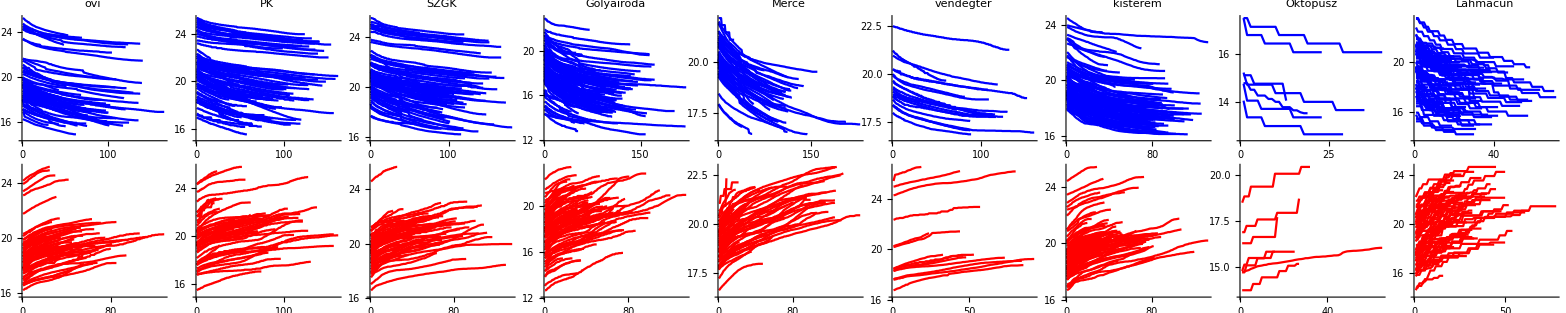

```mathematica
Table[
Table[
ListPlot[
Table[
Transpose[period][[2]]
,{period,wellBehavedTemperatureChangePeriodsForRooms[[room]][[coolingOrWarming]]}],Joined->True,PlotStyle->{Blue,Red}[[coolingOrWarming]],PlotLabel->{roomNames[[room]],""}[[coolingOrWarming]]
],{coolingOrWarming,1,2}],{room,roomsWithTempData}]//Transpose//Grid
```

#### épület falhőmérsékletének becslése

feltételezés: valamilyen simított belső hőmérséklet és külső hőmérséklet határozza meg a fal hőmérsékletét

```mathematica
roomNames
```

{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,trafóház,Oktopusz,Lahmacun,Kazán közös terek,műhely}

```mathematica
wallTempEstimatorRooms={1,2,3,4,5};
```

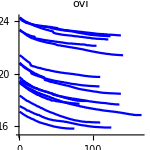
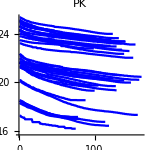
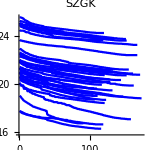
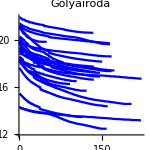
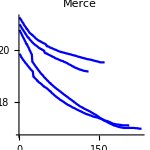

```mathematica
coolingOrWarming=1;
Table[
ListPlot[
Table[
If[
Abs[Mean[Differences[period[[-Min[{Length[period],15}];;-1]][[All,2]]]/Differences[period[[-Min[{Length[period],15}];;-1]][[All,1]]]]]<0.001,
period[[All,2]],
Nothing
]
,{period,wellBehavedTemperatureChangePeriodsForRooms[[room]][[coolingOrWarming]]}],Joined->True,PlotStyle->{Blue,Red}[[coolingOrWarming]],PlotLabel->{roomNames[[room]],""}[[coolingOrWarming]],ImageSize->150,AspectRatio->1
],{room,wallTempEstimatorRooms}]//Row
```

```mathematica
coolingOrWarming=1;
minTemperatureDailyByRoom=Table[
Table[
If[
Abs[Mean[Differences[period[[-Min[{Length[period],15}];;-1]][[All,2]]]/Differences[period[[-Min[{Length[period],15}];;-1]][[All,1]]]]]<0.001,
{IntegerPart[(period[[1]][[1]])/(24 60)],Min[period[[All,2]]]-1},
Nothing
]
,{period,wellBehavedTemperatureChangePeriodsForRooms[[room]][[coolingOrWarming]]}]
,{room,wallTempEstimatorRooms}];
```

```mathematica
meanInternalTemp=Select[Table[Flatten[{
dayN,
GetCentralTendencyAndWidth[
Flatten[
Table[
If[
Length[roomTempsDaily[[room]][[dayN]]]!=0,
Select[roomTempsDaily[[room]][[dayN]][[1]][[All,2]],NumberQ],
Nothing
],
{room,wallTempEstimatorRooms}]
],EstimateMode,StandardDeviation
]
}],{dayN,1,Length[seasonDays]}],NumberQ[Total[#]]&];
```

```mathematica
meanExternalTemp=Select[Table[Flatten[{
dayN,
GetCentralTendencyAndWidth[
If[
Length[externalTempDaily[[dayN]]]!=0,
Select[externalTempDaily[[dayN]][[All,2]],NumberQ],
Nothing
],EstimateMode,StandardDeviation
]
}],{dayN,1,Length[seasonDays]}],NumberQ[Total[#]]&];
```

```mathematica
meanEstimatedWallTemp=Select[Table[
Select[Flatten[minTemperatureDailyByRoom,1],#[[1]]==dayN&][[All,2]]//If[Length[#]!=0,Join[{dayN},Quiet[GetCentralTendencyAndWidth[#,EstimateMode,StandardError]]],Nothing]&
,{dayN,1,Length[seasonDays]}],MemberQ[#,{}]==False&];
```

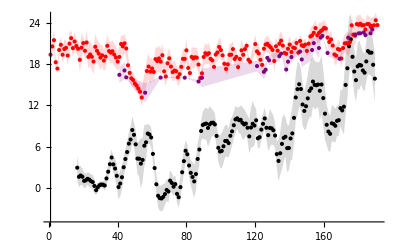

```mathematica
ErrorListPlot[
{
Transpose[MovingAverage[meanExternalTemp,4]],
Transpose[MovingAverage[meanInternalTemp,1]],
Transpose[MovingAverage[meanEstimatedWallTemp,1]]
},
{Black,Red,Purple},
{PlotRange->{All,{-5,25}},AxesOrigin->{1,-5}},
{False,True,False}
]
```

```mathematica
MeanExternalTempInterpolation=Interpolation[
Transpose[Transpose[MovingAverage[meanExternalTemp,14]][[{1,2}]]],
InterpolationOrder->1
];
```

```mathematica
MeanInternalTempInterpolation=Interpolation[
Transpose[Transpose[MovingAverage[meanInternalTemp,1]][[{1,2}]]],
InterpolationOrder->1
];
MeanWallTempInterpolation=Interpolation[
Transpose[Transpose[MovingAverage[meanEstimatedWallTemp,1]][[{1,2}]]],
InterpolationOrder->2];
```

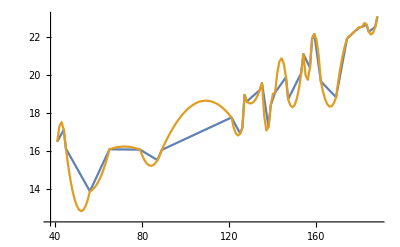

```mathematica
ListPlot[
{
Transpose[Transpose[meanEstimatedWallTemp][[{1,2}]]],
Table[{dayN,MeanWallTempInterpolation[dayN]},{dayN,Min[meanEstimatedWallTemp[[All,1]]],Max[meanEstimatedWallTemp[[All,1]]]}]
},Joined->True
]
```

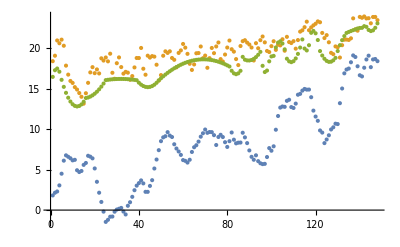

```mathematica
wallTempEstimationData=Table[
{
MeanExternalTempInterpolation[dayN],
MeanInternalTempInterpolation[dayN-1],
MeanWallTempInterpolation[dayN]
}
,{dayN,Min[meanEstimatedWallTemp[[All,1]]],Max[meanEstimatedWallTemp[[All,1]]]}];
ListPlot[Transpose[wallTempEstimationData]]
```

```mathematica
wallTempModelFit=LinearModelFit[wallTempEstimationData,{1,extT,intT},{extT,intT}];
wallTempParams=wallTempModelFit["BestFitParameters"];
wallTempModelFit["BestFit"]
```

3.96751+0.20041 extT+0.629006 intT

```mathematica
Manipulate[
ListPlot[
Transpose[Table[
{
MeanExternalTempInterpolation[dayN],
MeanInternalTempInterpolation[dayN-1],
MeanWallTempInterpolation[dayN],
baseTemp+extTempW MeanExternalTempInterpolation[dayN]+intTempW MeanInternalTempInterpolation[dayN-1]
}
,{dayN,Min[meanEstimatedWallTemp[[All,1]]],Max[meanEstimatedWallTemp[[All,1]]]}]],Joined->{False,False,False,True}
],
{{baseTemp,wallTempParams[[1]]},-20,20,0.01},
{{extTempW,wallTempParams[[2]]},0,2,0.01},
{{intTempW,wallTempParams[[3]]},0,2,0.01}
]
```

```mathematica
WallTempEstimator[extT_,intT_]:=8.19+0.36extT+0.26intT
```

```mathematica
coolingOrWarming=1;
stabilizedCoolingPeriodsForRooms=Table[
If[room!=8,
Table[
If[
Abs[Mean[Differences[period[[-Min[{Length[period],15}];;-1]][[All,2]]]/Differences[period[[-Min[{Length[period],15}];;-1]][[All,1]]]]]<0.001,
period,
Nothing
]
,{period,wellBehavedTemperatureChangePeriodsForRooms[[room]][[coolingOrWarming]]}],
None]
,{room,1,10}];
```

```mathematica
coolingOrWarming=1;
Manipulate[
ListPlot[
Map[
#[[All,2]]&,
stabilizedCoolingPeriodsForRooms[[room]]
],
Joined->True,PlotStyle->{Blue,Red}[[coolingOrWarming]],PlotLabel->{roomNames[[room]],""}[[coolingOrWarming]],ImageSize->250,AspectRatio->1,PlotRange->{All,{12,28}},
Prolog->Table[
Module[
{dayN,wallTemp},
dayN=IntegerPart[period[[1]][[1]]/(24 60)];
wallTemp=WallTempEstimator[MeanExternalTempInterpolation[dayN],MeanInternalTempInterpolation[dayN-1]]+roomWallTempShift;
{
Red,
Line[{{0,wallTemp},{1000,wallTemp}}]
}
],{period,stabilizedCoolingPeriodsForRooms[[room]]}]
],
{{roomWallTempShift,0},-5,5,0.1},
{room,roomsWithTempData}
]
```

#### burkolófelületek teljes hőkonduktivitása (W/K)

U felülvonás, [U] = W/K, minél kisebb, annál jobb
m^2-re vonatkoztatva [U] = W/(m^2 K), minél kisebb, annál jobb, tipikus értéke 0,2-5 között mozog

##### csak külső hőmérséklet, összes adat

```mathematica
calculationSpan=30;
spanError=0.1;
minTempDiffAcrossWall=3;
roomEnvelopeThermalResistanceEstimations=Table[
Module[
{roomHeatCapacity,calculationData,timeVector,TimeNearestFunction,PositionFinder},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
calculationData=Select[Flatten[DeleteCases[Table[If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[
{
dayN 24 60+Range[5,24 60,5],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Transpose[externalTempDaily[[dayN]]][[2]]
}
],
None
],{dayN,1,Length[seasonDays]}],None],1],NumberQ[Total[#]]&];
timeVector=Transpose[calculationData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,periodData,Δt,ΔT,externalTempAverage,roomTempAverage,periodDerivedParameters,Tdiff},
pos2=PositionFinder[calculationData[[pos1]][[1]]+calculationSpan];
periodData=calculationData[[pos1;;pos2]];
Δt=(periodData[[-1]][[1]]-periodData[[1]][[1]]);
periodDerivedParameters={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Total[Transpose[periodData][[2]]]==0,(*2 no heating during period*)
Min[Differences[Transpose[periodData][[3]]]]<0,(*3 monotonous cooling during period*)
Mean[Transpose[periodData][[3]]],(*4 avg room temp*)
Mean[Transpose[periodData][[4]]],(*5 avg external temp*)
Quiet[(periodData[[-1]][[3]]-periodData[[1]][[3]])/(60Δt)](*6 ΔT / Δt*)
};
Tdiff=periodDerivedParameters[[4]]-periodDerivedParameters[[5]];
If[
periodDerivedParameters[[1]]&&
periodDerivedParameters[[2]]&&
periodDerivedParameters[[3]]&&
minTempDiffAcrossWall<=Tdiff&&
periodDerivedParameters[[6]]<0&&
roomHeatCapacity periodDerivedParameters[[6]]!=0,
Tdiff/Abs[(roomHeatCapacity periodDerivedParameters[[6]])],(*R_total calculation*)
Nothing
]
],{pos1,2,Length[calculationData]}]
]
,{room,1,10}];
```

```mathematica
roomEnvelopeThermalResistanceEstimations=Import[NotebookDirectory[]<>"roomEnvelopeThermalResistanceEstimations.mx"];
```

```mathematica
Export[NotebookDirectory[]<>"roomEnvelopeThermalResistanceEstimations.mx",roomEnvelopeThermalResistanceEstimations]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\roomEnvelopeThermalResistanceEstimations.mx

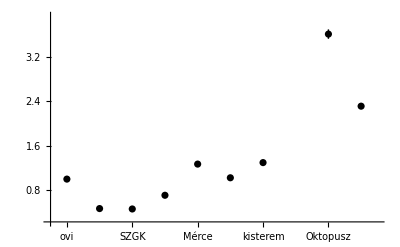

```mathematica
ErrorListPlot[
{
Transpose[Map[Flatten,Transpose[{Range[10],Map[GetMeanAndSEM[1/#]&,roomEnvelopeThermalResistanceEstimations]}][[roomsWithTempData]]]]
},
{Black},
{Ticks->{Transpose[{Range[10],Map[Rotate[#,Pi/2]&,roomNames[[1;;10]]]}],Automatic}},
{False,False,True}
]
```

```mathematica
roomEnvelopeThermalConductivities=Map[Mean[1/#]&,roomEnvelopeThermalResistanceEstimations];(*K/W*)
```

```mathematica
roomEnvelopeThermalConductivities1={0.9982577999173019,0.46863221112434744,0.4613273636460981,0.7076400111322203,1.2682439879749117,1.0221875156356737,1.2950835880618299,None,3.605230507310251,2.309339847023162};
```

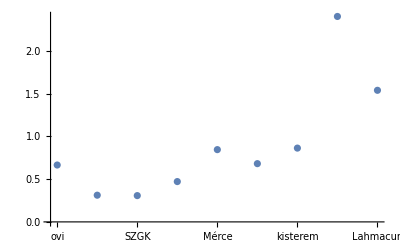

```mathematica
ListPlot[
(roomEnvelopeThermalConductivities1/roomExternalWallLength[[room]]roomHeight)[[roomsWithTempData]],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},PlotRange->All
]
```

##### csak külső hőmérséklet, válogatott adat

```mathematica
calculationSpan=120;
spanError=0.1;
minTempDiffAcrossWall=5;
roomEnvelopeThermalResistanceEstimations2=Table[
If[
room!=8,
Module[
{roomHeatCapacity},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
Select[
Table[
Module[
{timeVector,TimeNearestFunction,PositionFinder},
timeVector=Transpose[periodData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,Δt,ΔT,subPeriodData,externalTempAverage,roomTempAverage,subPeriodDerivedData,Tdiff},
pos2=PositionFinder[periodData[[pos1]][[1]]+calculationSpan];
subPeriodData=periodData[[pos1;;pos2]];
Δt=(subPeriodData[[-1]][[1]]-subPeriodData[[1]][[1]]);
subPeriodDerivedData={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Total[Transpose[subPeriodData][[4]]]==0,(*2 no heating during period*)
Min[Differences[Transpose[subPeriodData][[2]]]]<0,(*3 monotonous cooling during period*)
Mean[Transpose[subPeriodData][[2]]],(*4 avg room temp*)
Mean[Transpose[subPeriodData][[3]]],(*5 avg external temp*)
Quiet[(subPeriodData[[-1]][[2]]-subPeriodData[[1]][[2]])/(60 Δt)](*6 ΔT / Δt*)
};
Tdiff=subPeriodDerivedData[[4]]-subPeriodDerivedData[[5]];
If[
subPeriodDerivedData[[1]]&&
subPeriodDerivedData[[2]]&&
subPeriodDerivedData[[3]]&&
minTempDiffAcrossWall<=Tdiff&&
subPeriodDerivedData[[6]]<0&&
roomHeatCapacity subPeriodDerivedData[[6]]!=0,
Tdiff/Abs[(roomHeatCapacity subPeriodDerivedData[[6]])],(*R_total calculation*)
Nothing
]
],{pos1,1,Length[periodData]}]
]
,{periodData,wellBehavedTemperatureChangePeriodsForRooms[[room]][[1]]}],Length[#]>0&]
],None],{room,1,10}];
```

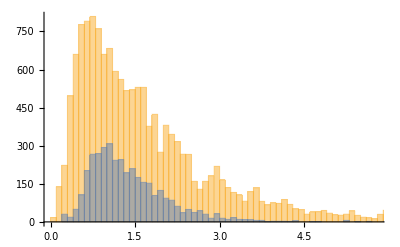
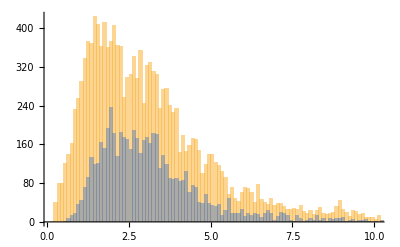
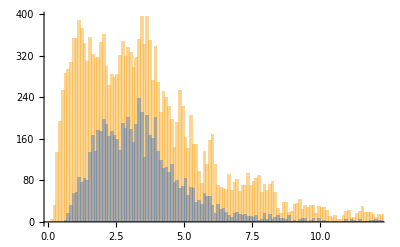
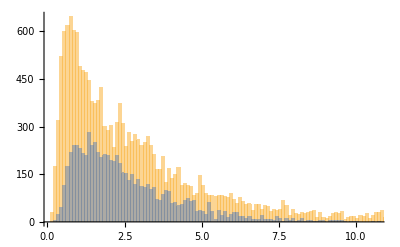
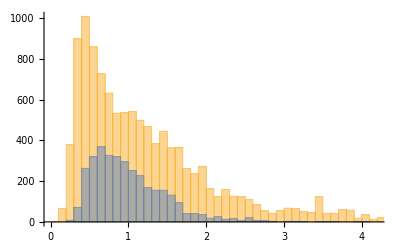
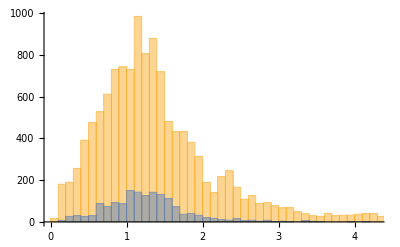
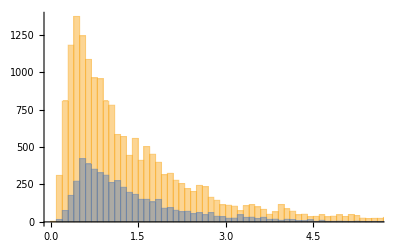
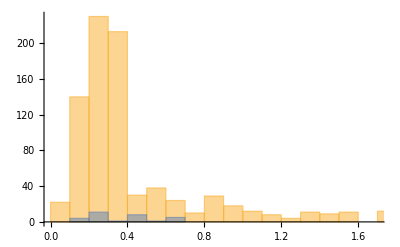

```mathematica
Table[Histogram[
{
roomEnvelopeThermalResistanceEstimations[[room]],
Flatten[roomEnvelopeThermalResistanceEstimations2[[room]]]
},{0.1}
],{room,roomsWithTempData}]
```

```mathematica
1/Map[EstimateMode[#]&,roomEnvelopeThermalResistanceEstimations]
```

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{}] should be a vector or a matrix of real numbers or a valid TemporalData object.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Table::iterb: Iterator {x,∞,-∞,-∞} does not have appropriate bounds.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Table::iterb: Iterator {x,∞,-∞,-∞} does not have appropriate bounds.

Table::iterb: Iterator {x,PDF[SmoothKernelDistribution[{}],x]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{1.48722,0.625411,0.854408,1.10885,1.87475,0.825585,2.27105,1/x,3.79191,2.34091}

```mathematica
1/Map[EstimateMode[Flatten[#]]&,roomEnvelopeThermalResistanceEstimations2]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[None].

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[Flatten[None]] should be a vector or a matrix of real numbers or a valid TemporalData object.

{1.00851,0.512941,0.294451,0.747658,1.51631,0.865935,1.20589,1/Flatten[None],3.86931,1.62289}

```mathematica
roomEnvelopeThermalConductivities2={1.0607677578521426,0.46840273862704324,0.31384032467390105,0.8308359733942713,1.516313557887951,0.8538825095917243,1.2058880587771799,None,3.79749914469404,1.8591852660560526}
```

{1.06077,0.468403,0.31384,0.830836,1.51631,0.853883,1.20589,None,3.7975,1.85919}

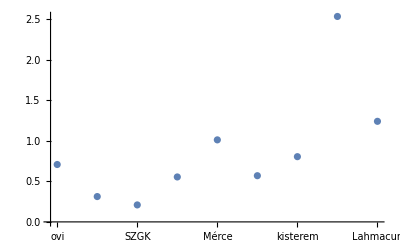

```mathematica
ListPlot[
(roomEnvelopeThermalConductivities2/roomExternalWallLength[[room]]roomHeight)[[roomsWithTempData]],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},PlotRange->All
]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[None].

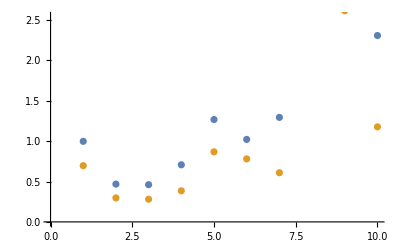

```mathematica
ListPlot[
{
roomEnvelopeThermalConductivities,
1/Map[Mean[Flatten[#]]&,roomEnvelopeThermalResistanceEstimations2]
}
]
```

##### h_int és h_ext külön, válogatott adat

```mathematica
calculationSpan=2 60;
spanError=0.1;
minTempDiffAcrossWall=5;
roomEnvelopeThermalResistanceData=Table[
If[
room!=8,
Module[
{roomHeatCapacity,roomInternalWallArea,roomExternalWallArea,wallTempCorrection},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomInternalWallArea=roomInternalWallLength[[room]]roomHeight;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
wallTempCorrection=If[room==9,3,0];
Select[
Table[
Module[
{timeVector,TimeNearestFunction,PositionFinder},
timeVector=Transpose[periodData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,Δt,ΔT,dayNFractional,subPeriodData,externalTempAverage,roomTempAverage,subPeriodDerivedData,Tdiff},
pos2=PositionFinder[periodData[[pos1]][[1]]+calculationSpan];
subPeriodData=periodData[[pos1;;pos2]];
Δt=(subPeriodData[[-1]][[1]]-subPeriodData[[1]][[1]]);
dayNFractional=Mean[subPeriodData[[1]]]/(24 60);
subPeriodDerivedData={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Total[Transpose[subPeriodData][[4]]]==0,(*2 no heating during period*)
Min[Differences[Transpose[subPeriodData][[2]]]]<0,(*3 monotonous cooling during period*)
minTempDiffAcrossWall<=Mean[Transpose[subPeriodData][[2]]]-Mean[Transpose[subPeriodData][[3]]],(*4*)
Mean[Transpose[subPeriodData][[2]]],(*5 avg room temp*)
Mean[Transpose[subPeriodData][[3]]],(*6 avg external temp*)
WallTempEstimator[
MeanExternalTempInterpolation[dayNFractional],
MeanInternalTempInterpolation[dayNFractional]
]-wallTempCorrection,(*7 internal wall temperature estimation*)
(subPeriodData[[-1]][[2]]-subPeriodData[[1]][[2]]),(*8 ΔT*)
60Δt (*9 Δt in seconds*)
};
If[
subPeriodDerivedData[[1]]&&subPeriodDerivedData[[2]]&&subPeriodDerivedData[[3]]&&subPeriodDerivedData[[4]]&&subPeriodDerivedData[[8]]<0&&subPeriodDerivedData[[8]]!=0&&
subPeriodDerivedData[[6]]<subPeriodDerivedData[[7]]<subPeriodDerivedData[[5]]
,
{
roomInternalWallArea(subPeriodDerivedData[[5]]-subPeriodDerivedData[[7]]),(*1 room temp - int temp*)
roomExternalWallArea(subPeriodDerivedData[[5]]-subPeriodDerivedData[[6]]),(*2 room temp - ext temp*)
-roomHeatCapacity subPeriodDerivedData[[8]]/subPeriodDerivedData[[9]](*3 ΔT/Δt in seconds*)
},
Nothing
]
],{pos1,1,Length[periodData]}]
]
,{periodData,wellBehavedTemperatureChangePeriodsForRooms[[room]][[1]]}],Length[#]>0&]
],None],{room,1,10}];
```

```mathematica
Map[Length[Flatten[#,1]]&,roomEnvelopeThermalResistanceData]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[None,1].

{3428,4705,6061,5926,3443,1547,5040,2,30,683}

```mathematica
Table[
ListPlot[
Transpose[SortBy[Flatten[roomEnvelopeThermalResistanceData[[room]],1],#[[3]]&]],
PlotLegends->Placed[{"Troom - Tint","Troom - Text","heat"},Bottom],ImageSize->400
],{room,{1,2,3,4,5,6,9,10}}]
```

```mathematica
alma=Table[
Module[
{fit},
fit=LinearModelFit[Flatten[roomEnvelopeThermalResistanceData[[room]],1],{hi,he},{hi,he},IncludeConstantBasis->False];
{fit["BestFitParameters"],fit["RSquared"]}
],{room,roomsWithTempData}];
alma
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

{{{0.000500325,0.0275395},0.852365},{{-0.00323721,0.0289567},0.838125},{{-0.000196138,0.019912},0.809643},{{0.00397887,0.0310326},0.728868},{{0.018882,0.0234291},0.860143},{{0.0265486,0.00973777},0.833892},{{0.,0.0309514},0.727443},{{0.168656,-0.0149482},0.919929},{{0.0359512,0.049481},0.843721}}

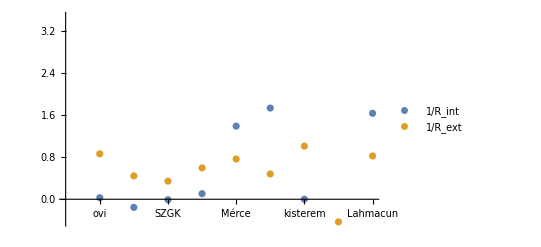

```mathematica
ListPlot[
{
Transpose[alma[[All,1]]][[1]](roomHeight roomInternalWallLength[[roomsWithTempData]]),
Transpose[alma[[All,1]]][[2]](roomHeight roomExternalWallLength[[roomsWithTempData]])
},PlotLegends->{"1/R_int","1/R_ext"},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

##### fal arányban átlagolt hűlési hőmérséklet, válogatott adat

```mathematica
calculationSpan=2 60;
spanError=0.1;
minTempDiffAcrossWall=5;
roomEnvelopeThermalResistanceData=Table[
If[
room!=8,
Module[
{roomHeatCapacity,roomInternalWallArea,roomExternalWallArea,totalWallArea,internalWallWeight,externalWallWeight},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomInternalWallArea=roomInternalWallLength[[room]]roomHeight;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
totalWallArea=roomInternalWallArea+roomExternalWallArea;
internalWallWeight=roomInternalWallArea/totalWallArea;
externalWallWeight=roomExternalWallArea/totalWallArea;
Select[
Table[
Module[
{timeVector,TimeNearestFunction,PositionFinder},
timeVector=Transpose[periodData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,Δt,ΔT,dayNFractional,subPeriodData,externalTempAverage,roomTempAverage,subPeriodDerivedData,Tdiff},
pos2=PositionFinder[periodData[[pos1]][[1]]+calculationSpan];
subPeriodData=periodData[[pos1;;pos2]];
Δt=(subPeriodData[[-1]][[1]]-subPeriodData[[1]][[1]]);
dayNFractional=Mean[subPeriodData[[1]]]/(24 60);
subPeriodDerivedData={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Total[Transpose[subPeriodData][[4]]]==0,(*2 no heating during period*)
Min[Differences[Transpose[subPeriodData][[2]]]]<0,(*3 monotonous cooling during period*)
minTempDiffAcrossWall<=Mean[Transpose[subPeriodData][[2]]]-Mean[Transpose[subPeriodData][[3]]],(*4*)
Mean[Transpose[subPeriodData][[2]]],(*5 avg room temp*)
Mean[Transpose[subPeriodData][[3]]],(*6 avg external temp*)
WallTempEstimator[
MeanExternalTempInterpolation[dayNFractional],
MeanInternalTempInterpolation[dayNFractional]
],(*7 internal wall temperature estimation*)
(subPeriodData[[-1]][[2]]-subPeriodData[[1]][[2]]),(*8 ΔT*)
60Δt (*9 Δt in seconds*)
};
If[
subPeriodDerivedData[[1]]&&subPeriodDerivedData[[2]]&&subPeriodDerivedData[[3]]&&subPeriodDerivedData[[4]]&&subPeriodDerivedData[[8]]<0&&subPeriodDerivedData[[8]]!=0&&
subPeriodDerivedData[[6]]<subPeriodDerivedData[[7]]<subPeriodDerivedData[[5]]
,
{
totalWallArea(subPeriodDerivedData[[5]]-(internalWallWeight subPeriodDerivedData[[7]]+externalWallWeight subPeriodDerivedData[[6]])),(*1 room temp - avg temp*)
-roomHeatCapacity subPeriodDerivedData[[8]]/subPeriodDerivedData[[9]](*2 ΔT/Δt in seconds*)
},
Nothing
]
],{pos1,1,Length[periodData]}]
]
,{periodData,wellBehavedTemperatureChangePeriodsForRooms[[room]][[1]]}],Length[#]>0&]
],None],{room,1,10}];
```

```mathematica
Map[Length[Flatten[#,1]]&,roomEnvelopeThermalResistanceData]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[None,1].

{3428,4705,6061,5926,3443,1547,5040,2,14,683}

```mathematica
roomEnvelopeThermalHeatTransferCoefficients=Quiet[Table[
Module[
{fit},
fit=LinearModelFit[Flatten[roomEnvelopeThermalResistanceData[[room]],1],{h},{h},IncludeConstantBasis->False];
{fit["BestFitParameters"],fit["RSquared"]}
],{room,1,10}][[All,1]][[All,1]]]
```

```mathematica
roomEnvelopeThermalHeatTransferCoefficients={0.01857740025303244,0.011157386895852559,0.00921118661636712,0.024180881646858624,0.021587217272691524,0.013973212020756952,0.03095141368116588,None,0.06363742877522778,0.04376707517680901};
```

```mathematica
roomEnvelopeThermalHeatTransferCoefficients(roomExternalWallLength[[1;;10]]+roomInternalWallLength[[1;;10]])roomHeight
```

{1.68237,0.703362,0.618992,1.10652,2.29343,1.60077,1.01025,80. None,6.10919,2.71706}

```mathematica
roomEnvelopeThermalConductivities3={1.6823693669146178,0.7033616699145453,0.6189917406198705,1.1065171441602508,2.2934259630507476,1.6007711690979165,1.0102541425532543,None,6.109193162421867,2.717060026976303};
```

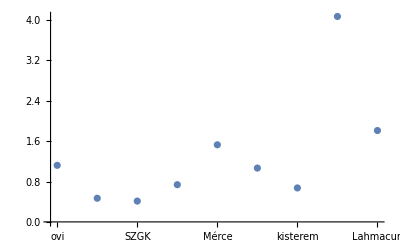

```mathematica
ListPlot[
(roomEnvelopeThermalConductivities3/roomExternalWallLength[[room]]roomHeight)[[roomsWithTempData]],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},PlotRange->All
]
```

##### többféle számítás összevetése

```mathematica
roomEnvelopeThermalConductivitiesAllVersions={
roomEnvelopeThermalConductivities1,roomEnvelopeThermalConductivities2,roomEnvelopeThermalConductivities3
};
```

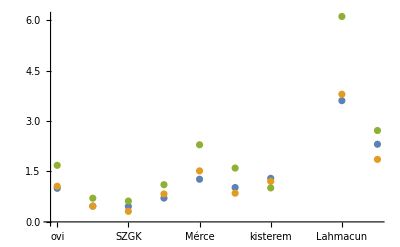

```mathematica
(*teljes, W/K*)
ListPlot[
Table[
roomEnvelopeThermalConductivitiesAllVersions[[version]] 
,{version,1,3}],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},PlotRange->All
]
```

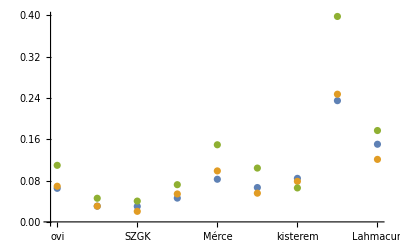

```mathematica
(*fajlagos, W/(K m2)*)
ListPlot[
Table[
(roomEnvelopeThermalConductivitiesAllVersions[[version]]/(roomExternalWallLength[[room]]roomHeight))[[roomsWithTempData]]
,{version,1,3}],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic},PlotRange->All
]
```

```mathematica
roomEnvelopeThermalConductivities=roomEnvelopeThermalConductivitiesAllVersions[[1]]
```

```mathematica
roomEnvelopeThermalConductivities={0.9982577999173019,0.46863221112434744,0.4613273636460981,0.7076400111322203,1.2682439879749117,1.0221875156356737,1.2950835880618299,None,3.605230507310251,2.309339847023162};
```

```mathematica
roomEnvelopeThermalConductivitiesPerExternalWallArea=roomEnvelopeThermalConductivities/(roomExternalWallLength[[room]]roomHeight)
```

```mathematica
roomEnvelopeThermalConductivitiesPerExternalWallArea={0.06499074218211601,0.03050990957840804,0.030034333570709514,0.04607031322475393,0.08256796796711666,0.06654866638253085,0.08431533776444206,0.06510416666666667 None,0.2347155278196778,0.15034764629057046};
```

#### radiátorok konvektív hőátadási tényezője (W/m^2 K) --> valójában szobák teljes melegedése, a radiátornak nincs itt értelme

##### csak külső hőmérséklet, összes adat

```mathematica
calculationSpan=10;
spanError=0.1;
roomRadiatorConvectiveHeatTransferCoefficientEstimations=Table[
Module[
{roomHeatCapacity,roomEnvelopeThermalConductivity,roomRadiatorArea,calculationData,timeVector,TimeNearestFunction,PositionFinder},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomEnvelopeThermalConductivity=roomEnvelopeThermalConductivities[[room]];(*W/K!*)
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
calculationData=Select[Flatten[DeleteCases[Table[If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[
{
dayN 24 60+Range[5,24 60,5],
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],
Transpose[externalTempDaily[[dayN]]][[2]],
Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[externalTempDaily[[dayN]]][[2]]]
}
],
None
],{dayN,1,Length[seasonDays]}],None],1],NumberQ[Total[#]]&];
timeVector=Transpose[calculationData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,periodData,Δt,ΔT,externalTempAverage,roomTempAverage,periodDerivedParameters,TdiffExt,TdiffHeater,Qroom,Qheater,Qwall},
pos2=PositionFinder[calculationData[[pos1]][[1]]+calculationSpan];
periodData=calculationData[[pos1;;pos2]];
Δt=(periodData[[-1]][[1]]-periodData[[1]][[1]]);
periodDerivedParameters={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Mean[Transpose[periodData][[2]]]==1,(*2 constant heating during period*)
Min[Differences[Transpose[periodData][[3]]]]>0,(*3 monotonous warming during period*)
Mean[Transpose[periodData][[3]]],(*4 avg room temp*)
Mean[Transpose[periodData][[4]]],(*5 avg external temp*)
Mean[Transpose[periodData][[5]]],(*6 avg heater temp*)
Quiet[(periodData[[-1]][[3]]-periodData[[1]][[3]])/(60Δt)](*7 ΔT / Δt*)
};
TdiffExt=periodDerivedParameters[[4]]-periodDerivedParameters[[5]];
TdiffHeater=periodDerivedParameters[[6]]-periodDerivedParameters[[4]];
Qwall=TdiffExt roomEnvelopeThermalConductivity;
Qroom=roomHeatCapacity periodDerivedParameters[[7]];
Qheater=Qroom+Qwall;
If[
periodDerivedParameters[[1]]&&
periodDerivedParameters[[2]]&&
periodDerivedParameters[[3]]&&
periodDerivedParameters[[7]]>0&&
roomHeatCapacity periodDerivedParameters[[7]]!=0,
Qheater/(roomRadiatorArea TdiffHeater),(*h calculation*)
Nothing
]
]
,{pos1,1,Length[calculationData]}]
]
,{room,1,10}];
```

$Aborted

```mathematica
Export[NotebookDirectory[]<>"roomRadiatorConvectiveHeatTransferCoefficientEstimations.mx",roomRadiatorConvectiveHeatTransferCoefficientEstimations]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\roomRadiatorConvectiveHeatTransferCoefficientEstimations.mx

```mathematica
roomRadiatorConvectiveHeatTransferCoefficients=Transpose[{Range[10],Quiet[Map[EstimateMode,roomRadiatorConvectiveHeatTransferCoefficientEstimations]]}];
```

```mathematica
roomRadiatorThermalConductivities1=roomRadiatorConvectiveHeatTransferCoefficients[[All,2]]
```

{0.148588,0.237615,0.14286,0.42138,0.191558,0.139379,0.136319,x,0.769451,3.24288}

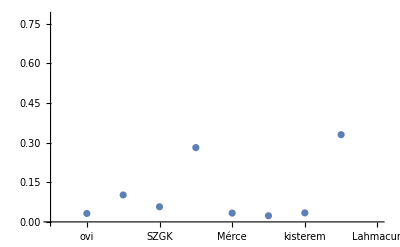

```mathematica
ListPlot[
Quiet[(roomRadiatorThermalConductivities1/roomRadiatorLength radiatorHeight 2)[[roomsWithTempData]] ],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

##### fal arányban átlagolt hűlési hőmérséklet, összes adat

```mathematica
calculationSpan=30;
spanError=0.1;
roomRadiatorConvectiveHeatTransferCoefficientData=Quiet[Table[
Module[
{roomHeatCapacity,roomInternalWallArea,roomExternalWallArea,totalWallArea,internalWallWeight,externalWallWeight,roomRadiatorArea,calculationData,timeVector,TimeNearestFunction,PositionFinder},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomInternalWallArea=roomInternalWallLength[[room]]roomHeight;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
totalWallArea=roomInternalWallArea+roomExternalWallArea;
internalWallWeight=roomInternalWallArea/totalWallArea;
externalWallWeight=roomExternalWallArea/totalWallArea;
roomRadiatorArea=roomRadiatorLength[[room]]radiatorHeight 2;
calculationData=Select[Flatten[DeleteCases[Table[If[
Dimensions[roomTempsDaily[[room]][[dayN]]]!={}&&Dimensions[externalTempDaily[[dayN]]]!={}&&Dimensions[heatingStateDaily[[dayN]]]!={},
Transpose[
{
dayN 24 60+Range[5,24 60,5],(*1*)
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],(*2*)
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],(*3*)
Transpose[externalTempDaily[[dayN]]][[2]],(*4*)
Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[externalTempDaily[[dayN]]][[2]]],(*5*)
WallTempEstimator[
MeanExternalTempInterpolation[dayN],
MeanInternalTempInterpolation[dayN]
](*6*)
}
],
None
],{dayN,1,Length[seasonDays]}],None],1],NumberQ[Total[#]]&];
timeVector=Transpose[calculationData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,periodData,Δt,ΔT,externalTempAverage,roomTempAverage,periodDerivedParameters,TdiffAvg,TdiffHeater,Qroom,Qgain,Qloss},
pos2=PositionFinder[calculationData[[pos1]][[1]]+calculationSpan];
periodData=calculationData[[pos1;;pos2]];
Δt=(periodData[[-1]][[1]]-periodData[[1]][[1]]);
periodDerivedParameters={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Mean[Transpose[periodData][[2]]]==1,(*2 constant heating during period*)
Min[Differences[Transpose[periodData][[3]]]]>0,(*3 monotonous warming during period*)
Mean[Transpose[periodData][[3]]],(*4 avg room temp*)
Mean[Transpose[periodData][[4]]],(*5 avg external temp*)
Mean[Transpose[periodData][[5]]],(*6 avg heater temp*)
Mean[Transpose[periodData][[6]]],(*7 avg wall temp*)
Quiet[(periodData[[-1]][[3]]-periodData[[1]][[3]])/(60Δt)](*8 ΔT / Δt*)
};
TdiffAvg=(periodDerivedParameters[[4]]-(internalWallWeight periodDerivedParameters[[7]]+externalWallWeight periodDerivedParameters[[5]]));
TdiffHeater=periodDerivedParameters[[6]]-periodDerivedParameters[[4]];
Qloss=TdiffAvg roomEnvelopeThermalConductivities[[room]];
Qroom=roomHeatCapacity periodDerivedParameters[[8]];
Qgain=Qroom+Qloss;
If[
periodDerivedParameters[[1]]&&
periodDerivedParameters[[2]]&&
periodDerivedParameters[[3]]&&
periodDerivedParameters[[8]]>0&&
roomHeatCapacity periodDerivedParameters[[8]]!=0,
{roomRadiatorArea TdiffHeater,Qgain},(*h estimation data*)
Nothing
]
]
,{pos1,1,Length[calculationData]}]
]
,{room,1,10}]];
```

ez valamiért nem működik, pedig valszeg pontosabb becslést ad, mint a többi, fittelni kell majd a két oszlopot

```mathematica
roomRadiatorThermalConductivities2={0.15250229638926738,0.168703360142732,0.16873584837102043,0.4008207756252688,0.15917869450450967,0.1431452552523042,0.2362745543903207,None,0.5166470326430609,3.1308364744008643};
```

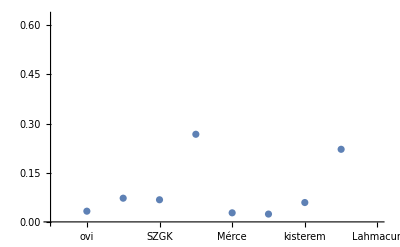

```mathematica
ListPlot[
Quiet[(roomRadiatorThermalConductivities2/roomRadiatorLength radiatorHeight 2)[[roomsWithTempData]] ],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

```mathematica
(roomRadiatorThermalConductivities2/roomRadiatorLength radiatorHeight 2)[[roomsWithTempData]]
```

```mathematica
(*roomRadiatorThermalConductivities={1.0248154317358766,0.5668432900795795,0.6074490541356735,0.8657728753505807,
1.31799959049734,1.2367750053799085,1.360941433288247,0.,1.7359340296806842,3.757003769281037};*)
```

##### fal arányban átlagolt hűlési hőmérséklet, válogatott adat

```mathematica
calculationSpan=30;
spanError=0.1;
roomRadiatorConvectiveHeatTransferCoefficientsData=Table[
If[
room!=8,
Module[
{roomHeatCapacity,roomInternalWallArea,roomExternalWallArea,totalWallArea,internalWallWeight,externalWallWeight,roomRadiatorArea},
roomHeatCapacity=roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity;
roomInternalWallArea=roomInternalWallLength[[room]]roomHeight;
roomExternalWallArea=roomExternalWallLength[[room]]roomHeight;
totalWallArea=roomInternalWallArea+roomExternalWallArea;
internalWallWeight=roomInternalWallArea/totalWallArea;
externalWallWeight=roomExternalWallArea/totalWallArea;
roomRadiatorArea=2roomRadiatorLength[[room]]radiatorHeight;
Select[
Table[
Module[
{timeVector,TimeNearestFunction,PositionFinder},
timeVector=Transpose[periodData][[1]];
TimeNearestFunction=Nearest[timeVector];
PositionFinder[val_]:=Position[timeVector,TimeNearestFunction[val][[1]]][[1]][[1]];
Table[
Module[
{pos2,Δt,ΔT,dayNFractional,subPeriodData,externalTempAverage,roomTempAverage,subPeriodDerivedData,Tdiff},
pos2=PositionFinder[periodData[[pos1]][[1]]+calculationSpan];
subPeriodData=periodData[[pos1;;pos2]];
Δt=(subPeriodData[[-1]][[1]]-subPeriodData[[1]][[1]]);
dayNFractional=Mean[subPeriodData[[1]]]/(24 60);
subPeriodDerivedData={
(Abs[Δt-calculationSpan])/calculationSpan<spanError,(*1 Δt is in the desired range*)
Mean[Transpose[subPeriodData][[4]]]>0.9,(*2 at least 90% heating during period*)
Min[Differences[Transpose[subPeriodData][[2]]]]>0,(*3 monotonous warming during period*)
None,
Mean[Transpose[subPeriodData][[2]]],(*5 avg room temp*)
Mean[Transpose[subPeriodData][[3]]],(*6 avg external temp*)
WallTempEstimator[
MeanExternalTempInterpolation[dayNFractional],
MeanInternalTempInterpolation[dayNFractional]
],(*7 internal wall temperature estimation*)
Mean[Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[subPeriodData][[3]]]],(*8 avg heating water temp*)
(subPeriodData[[-1]][[2]]-subPeriodData[[1]][[2]]),(*9 ΔT*)
60Δt (*10 Δt in seconds*)
};
If[
subPeriodDerivedData[[1]]&&subPeriodDerivedData[[2]]&&subPeriodDerivedData[[3]]&&subPeriodDerivedData[[8]]>0&&subPeriodDerivedData[[8]]!=0&&
subPeriodDerivedData[[6]]<subPeriodDerivedData[[5]],
{
roomRadiatorArea(subPeriodDerivedData[[8]]-subPeriodDerivedData[[5]]),(*1 warming*)
roomHeatCapacity subPeriodDerivedData[[9]]/subPeriodDerivedData[[10]]-roomEnvelopeThermalHeatTransferCoefficients[[room]]totalWallArea(subPeriodDerivedData[[5]]-(internalWallWeight subPeriodDerivedData[[7]]+externalWallWeight subPeriodDerivedData[[6]]))(*2 room heat change - cooling*)
},
Nothing
]
],{pos1,1,Length[periodData]}]
]
,{periodData,wellBehavedTemperatureChangePeriodsForRooms[[room]][[2]]}],Length[#]>0&]
],None],{room,1,10}];
```

```mathematica
Map[Length[Flatten[#,1]]&,roomRadiatorConvectiveHeatTransferCoefficientsData]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[None,1].

{1168,267,1437,812,2597,248,2328,2,33,1}

```mathematica
Quiet[Table[
Module[
{fit},
fit=LinearModelFit[Flatten[roomRadiatorConvectiveHeatTransferCoefficientsData[[room]],1],{h},{h},IncludeConstantBasis->False];
{fit["BestFitParameters"],fit["RSquared"]}
],{room,1,10}][[All,1]][[All,1]]]
```

```mathematica
{0.04582109939516246,0.05970461601040744,0.05359593313357529,0.21175929110522904,0.027410913730274763,0.046005095605829965,0.07273046695640674,"BestFitParameters",-0.007165951433135245,1.7794203310950425}
```

##### többféle számítás összevetése

```mathematica
roomRadiatorThermalConductivitiesAllVersions={
roomRadiatorThermalConductivities1,roomRadiatorThermalConductivities2
};
```

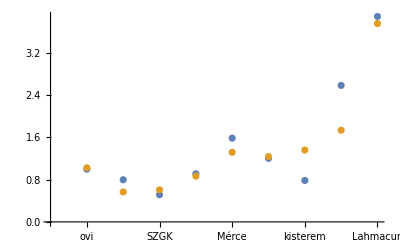

```mathematica
(*teljes hőkonduktivitás ami a szobát éri*)
ListPlot[
Table[
Quiet[(roomRadiatorThermalConductivitiesAllVersions[[version]] roomRadiatorLength radiatorHeight 2)[[roomsWithTempData]]]
,{version,1,2}],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

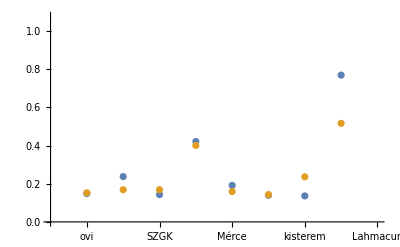

```mathematica
(*fajlagos*)
ListPlot[
Table[
(roomRadiatorThermalConductivitiesAllVersions[[version]])[[roomsWithTempData]]
,{version,1,2}],
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/2]&,roomNames[[roomsWithTempData]]]}],Automatic}
]
```

```mathematica
roomRadiatorThermalConductivitiesPerRadiatorArea=roomRadiatorThermalConductivitiesAllVersions[[2]]
```

```mathematica
roomRadiatorThermalConductivitiesPerRadiatorArea={0.15250229638926738,0.168703360142732,0.16873584837102043,0.4008207756252688,0.15917869450450967,0.1431452552523042,0.2362745543903207,None,0.5166470326430609,3.1308364744008643};
```

```mathematica
roomHeatingThermalConductivities=Quiet[(roomRadiatorThermalConductivitiesAllVersions[[2]] roomRadiatorLength radiatorHeight 2)]
```

```mathematica
roomHeatingThermalConductivities={1.0248154317358766,0.5668432900795795,0.6074490541356735,0.8657728753505807,1.31799959049734,1.2367750053799085,1.360941433288247,0.,1.7359340296806842,3.757003769281037};
```

```mathematica
roomRadiatorThermalConductivities=Quiet[(4 roomRadiatorLength radiatorHeight 2)]
```

```mathematica
roomRadiatorThermalConductivities={26.88,13.44,14.399999999999999,8.64,33.12,34.56,23.04,0.,13.44,4.8};
```

#### értelmezés

```mathematica
day=40;
```

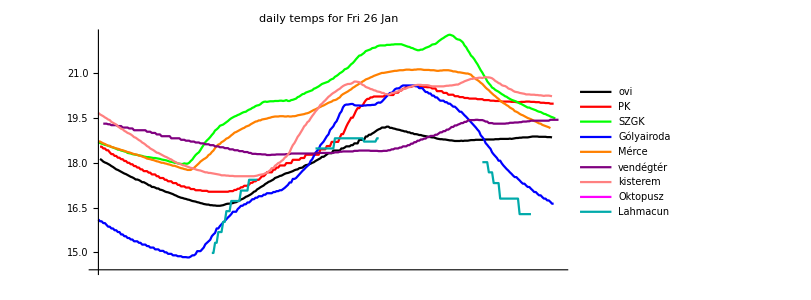

```mathematica
day=80;
plot=DateListPlot[
Table[Transpose[roomTempsDaily][[day]][[room]][[1]],{room,roomsWithTempData}],
Frame->None,AspectRatio->0.5,ImageSize->600,PlotLegends->Placed[roomNames[[roomsWithTempData]],Bottom],PlotStyle->roomColors[[roomsWithTempData]],PlotLabel->"daily temps for "<>StringTake[DateString[seasonDays[[day]]],{1,10}]
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\room_temps_example.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\room_temps_example.png

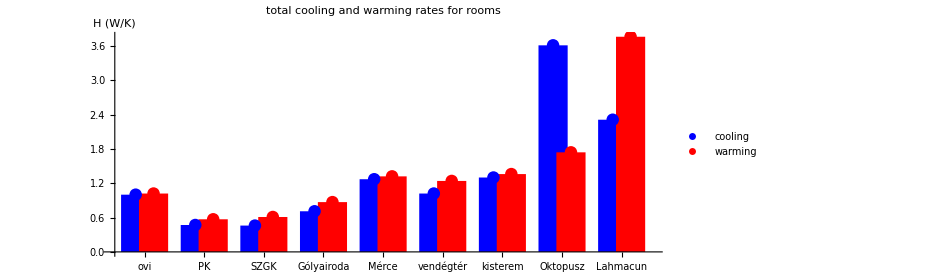

```mathematica
plot=ListPlot[
{
Transpose[{
Range[9]-0.15,
Round[roomEnvelopeThermalConductivities,0.01][[roomsWithTempData]]
}],
Transpose[{
Range[9]+0.15,
Round[roomHeatingThermalConductivities,0.01][[roomsWithTempData]]
}]
},
PlotRange->{{0.5,9.5},All},AxesOrigin->{0.5,0},PlotStyle->{Blue,Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4 ]&,roomNames[[roomsWithTempData]]]}],Automatic},
AxesLabel->{None,"H (W/K)"},AspectRatio->0.4,ImageSize->700,
PlotLegends->Placed[{"cooling","warming"},Bottom],ImageSize->600,PlotLabel->"total cooling and warming rates for rooms"
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\total_cooling_and_warming.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\total_cooling_and_warming.png

látszik, hogy a legtöbb szobát ki lehet fűteni, kivéve az Oktopuszt, és az is látszik, hogy valami fura van a Lahmacunnal --> egyrészt lyuk, másrészt hőmérő rossz helyen

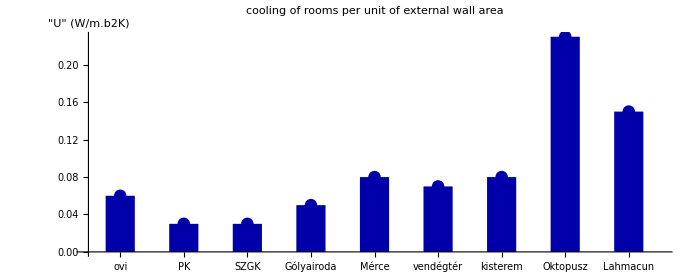

```mathematica
plot=ListPlot[
{
Transpose[{
Range[9],
Round[roomEnvelopeThermalConductivitiesPerExternalWallArea,0.01][[roomsWithTempData]]
}]
},
PlotRange->{{0.5,9.5},All},AxesOrigin->{0.5,0},PlotStyle->{Darker[Blue],Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},AspectRatio->0.4,ImageSize->700,
AxesLabel->{None,"\"U\" (W/m.b2K)"},ImageSize->600,PlotLabel->"cooling of rooms per unit of external wall area"
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\cooling_per_external_wall.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\cooling_per_external_wall.png

nagyjából azonos, kivéve a két kiugrót, és az is látszik, hogy itt már eléri a határait a módszer, mert irreálisak az értékek
--> de az arányok használhatóak

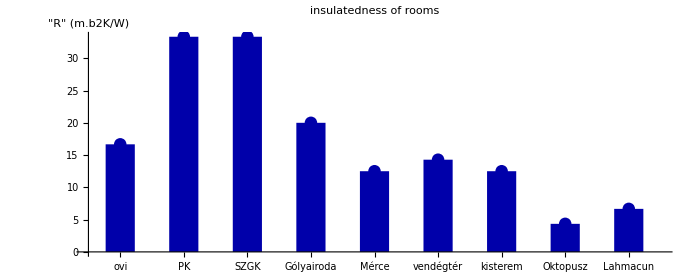

```mathematica
plot=ListPlot[
{
Transpose[{
Range[9],
1/Round[roomEnvelopeThermalConductivitiesPerExternalWallArea,0.01][[roomsWithTempData]]
}]
},
PlotRange->{{0.5,9.5},All},AxesOrigin->{0.5,0},PlotStyle->{Darker[Blue],Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},AspectRatio->0.4,ImageSize->700,
AxesLabel->{None,"\"R\" (m.b2K/W)"},ImageSize->600,PlotLabel->"insulatedness of rooms"
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\insulatedness.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\insulatedness.png

mint fönt, csak itt jobban kiugranak az arányok, lehet ezt érdemes mutatni inkább

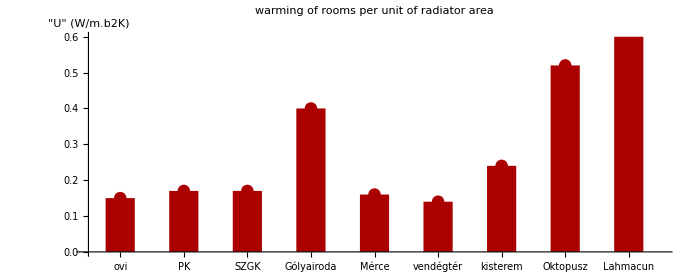

```mathematica
plot=ListPlot[
Quiet[{
Transpose[{
Range[9],
Round[roomHeatingThermalConductivities/(2 roomRadiatorLength radiatorHeight),0.01][[roomsWithTempData]]
}]
}],
PlotRange->{{0.5,9.5},{0,0.6}},AxesOrigin->{0.5,0},
PlotStyle->{Darker[Red]},Filling->Axis,FillingStyle->{Thickness[0.03]},PlotRange->{{0.5,9},Automatic},
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},AspectRatio->0.4,ImageSize->700,
AxesLabel->{None,"\"U\" (W/m.b2K)"},ImageSize->600,PlotLabel->"warming of rooms per unit of radiator area"
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\warming_per_radiator_area.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\warming_per_radiator_area.png

```mathematica
Quiet[(roomHeatingThermalConductivities/(2 roomRadiatorLength radiatorHeight))][[{2,3}]]
```

{0.168703,0.168736}

mutatja a módszer erejét, mert azonos értékek jöttek ki azokra a szobákra, ahol csak radiátort használtak
de mutatja a határait is, mert maga az érték nem reális
Gólyairoda, Oktopusz - space heater
Lahmacun - rosszul elhelyezett hőmérő
kisterem - tömeg

a konzisztens értékű szobákból esetleg lehetne korrigálni a becslés többi részét a radiátor specifikációja alapján?

### hőleadási arányok körönként -- körök relatív súlya az egész rendszerben

melyik kör súlya mekkora a totálból naponta, havonta, egész ciklusra

```mathematica
daysWithMissingHeatStockData=DeleteDuplicates[Flatten[Map[First,Position[Transpose[heatStockDaily],None]]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191}

```mathematica
cycleHeatingDaily=Quiet[Table[
If[
MemberQ[daysWithMissingHeatStockData,day],
ConstantArray[None,4],
Transpose[{
ConstantArray[seasonDays[[day]],4],
Table[
Transpose[heatStockDaily][[day]][[cycle]][[-1]][[2]]
,{cycle,1,4}]
}]
]
,{day,Range[Length[seasonDays]]}]];
```

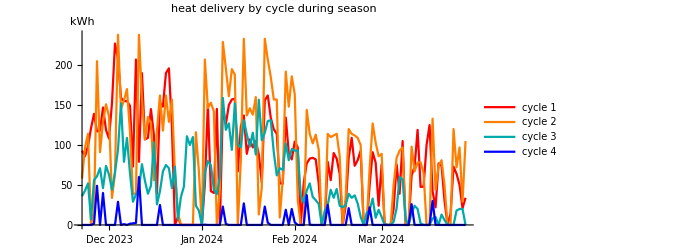

```mathematica
plot=DateListPlot[
Transpose[Select[cycleHeatingDaily,MemberQ[#,None]==False&]],Frame->None,ImageSize->500,PlotLabel->"heat delivery by cycle during season",AspectRatio->0.5,PlotStyle->{Red,Orange,Darker[Cyan],Blue},PlotLegends->Placed[{"cycle 1","cycle 2","cycle 3","cycle 4"},Bottom],AxesLabel->{None,"kWh"}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\heat_delivery_by_cycle.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\heat_delivery_by_cycle.png

```mathematica
cycleHeatingWeightsDaily=Quiet[Table[
If[
MemberQ[daysWithMissingHeatStockData,day],
ConstantArray[None,4],
Transpose[{
ConstantArray[seasonDays[[day]],4],
Table[
Transpose[heatStockDaily][[day]][[cycle]][[-1]][[2]]
,{cycle,1,4}]/Total[Map[#[[-1]][[2]]&,Transpose[heatStockDaily][[day]]]]
}]
]
,{day,Range[Length[seasonDays]]}]];
```

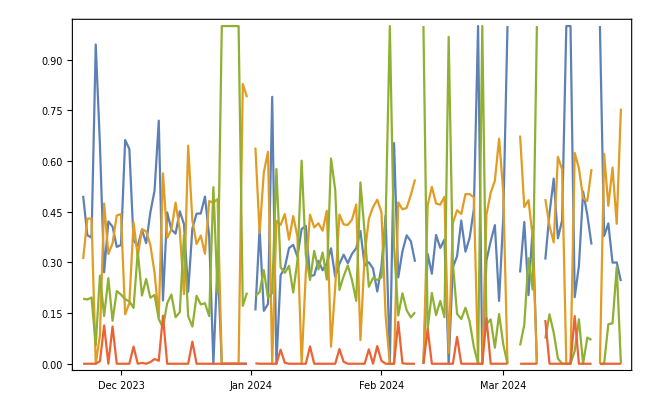

```mathematica
DateListPlot[Transpose[Select[cycleHeatingWeightsDaily,MemberQ[#,None]==False&]]]
```

### hőfelvételi arányok szobánként

#### szobák relatív súlya egy körön

```mathematica
radiatorThermalConductivityPerUnitArea=Mean[roomRadiatorThermalConductivitiesPerRadiatorArea[[{1,2,3,5,6}]]]
```

```mathematica
radiatorThermalConductivityPerUnitArea=0.15845309093196674;
```

```mathematica
fullHeatDynamics=Quiet[
Table[
Table[
Table[
Module[
{dayN,roomEnvelopeThermalConductivity,roomRadiatorThermalConductivity,roomTemp,externalTemp,heaterTemp,tempDiffExt,tempDiffHeater,roomExternalWallArea,heatLoss,roomRadiatorArea,heatGain},
dayN=Position[seasonDays,day][[1]][[1]];
roomEnvelopeThermalConductivity=roomEnvelopeThermalConductivities[[room]];
roomRadiatorThermalConductivity=radiatorThermalConductivityPerUnitArea(2 roomRadiatorLength[[room]] radiatorHeight);
roomTemp=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
heaterTemp=Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[externalTempDaily[[dayN]]][[2]]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=heaterTemp-roomTemp;
heatLoss= tempDiffExt roomEnvelopeThermalConductivity;
heatGain=tempDiffHeater roomRadiatorThermalConductivity Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]];
Transpose[{
Transpose[externalTempDaily[[dayN]]][[1]],(*1 time*)
Transpose[heatingStateDaily[[dayN]][[1+cycle]]][[2]],(*2 heating state*)
1000Clip[Differences[Transpose[heatStockDaily[[cycle]][[dayN]]][[2]]]/(5/60),{0,Infinity}]//Flatten[{#[[1]],#[[1;;-1]]}]&(*3 W*),
heatGain(*4 W*),
heatLoss(*5 W*),
externalTemp(*6 W*),
roomTemp(*7 W*)
}]
]
,{day,Drop[heatDataDays,1]}]
,{room,Flatten[Position[roomToCycle,cycle]]}]
,{cycle,1,3}]
];
```

```mathematica
heatingPeriodHeatDynamics=Table[
roomsOnCycle=Flatten[Position[roomToCycle,cycle]];
Select[
Module[
{dataForSeasonByRoom,heatingStateSwitch,heatingPeriods},
dataForSeasonByRoom=Table[Quiet[Select[Flatten[fullHeatDynamics[[cycle]][[roomOnCycleN]],1],ListQ]],{roomOnCycleN,1,Length[roomsOnCycle]}];
heatingStateSwitch=Differences[Transpose[dataForSeasonByRoom[[1]]][[2]]];
heatingPeriods=Transpose[{
Map[First,Position[heatingStateSwitch,1]],
Map[First,Position[heatingStateSwitch,-1]]
}];
Table[
{
Total[(5/60)Transpose[dataForSeasonByRoom[[1]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]]][[3]]/1000],(*conversion back to kWh*)
Table[
Module[
{heatingPeriodDataForRoom},
heatingPeriodDataForRoom=dataForSeasonByRoom[[roomOnCycleN]][[heatingPeriod[[1]]+1;;Min[heatingPeriod[[2]]+5,Length[dataForSeasonByRoom[[1]]]]]];
If[
Max[Differences[Map[UnixTime,Transpose[heatingPeriodDataForRoom][[1]]]]]<30 60,
Table[
Total[
Transpose[{
Differences[Map[UnixTime,heatingPeriodDataForRoom[[All,1]]]]/(60 60),(*passed time in h*)
Drop[Transpose[heatingPeriodDataForRoom][[heatGainOrLoss]],1]/1000(*power in kW*)
}]//Join[{#[[1]]},#]&//#[[All,1]]#[[All,2]]&(*conversion to kWh*)
]
,{heatGainOrLoss,4,5}],
{None,None}
]
],{roomOnCycleN,1,Length[roomsOnCycle]}]
}
,{heatingPeriod,heatingPeriods[[1;;{229,191,208}[[cycle]]]]}]
],ListQ]
,{cycle,1,3}];
```

```mathematica
heatSumsForHeatingPeriods=Quiet[Table[Select[Map[
{
#[[1]],(*supply*)
Total[Transpose[#[[2]]][[1]]],(*gain*)
Total[Transpose[#[[2]]][[2]]],(*loss*)
Total[Transpose[#[[2]]][[1]]]-Total[Transpose[#[[2]]][[2]]](*balance*)
}
&,heatingPeriodHeatDynamics[[cycle]]
],ListQ],{cycle,1,3}]];
```

```mathematica
dims={1,2};
Table[
Select[
Quiet[
Transpose[
Transpose[
Select[
heatSumsForHeatingPeriods[[cycle]],
NumberQ[#[[dims[[1]]]]+#[[dims[[2]]]]]&
]
][[{dims[[1]],dims[[2]]}]]
]
],NumberQ[Total[#]]&]//Correlation[#[[All,1]],#[[All,2]]]&,{cycle,1,3}]
```

{0.981639,0.570441,0.948887}

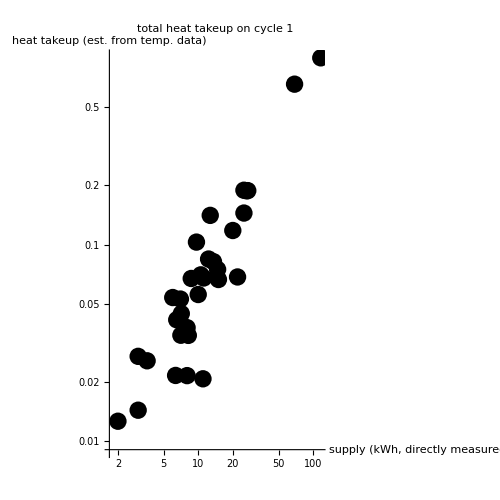

```mathematica
dimNames={
"supply\n(kWh, directly\nmeasured)",
"heat takeup\n(est. from\ntemp. data)",
"heat loss\n(est. from\ntemp. data)",
"heat balance\n(est. from\ntemp. data)"
};
plot=Table[
Table[
ListLogLogPlot[
Select[
Quiet[
Transpose[
Transpose[
Select[
heatSumsForHeatingPeriods[[cycle]],
NumberQ[#[[dims[[1]]]]+#[[dims[[2]]]]]&
]
][[{dims[[1]],dims[[2]]}]]
]
],NumberQ[Total[#]]&],
ImageSize->500,AspectRatio->1,PlotLabel->"total heat takeup on cycle "<>ToString[cycle],PlotRange->All,AxesLabel->dimNames[[dims]],PlotStyle->{Black,PointSize->0.025},BaseStyle->{FontSize->16}
]
,{cycle,1,3}]
,{dims,{{1,2}}}][[1]][[1]]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\cycle_1_supply_calc.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\cycle_1_supply_calc.png

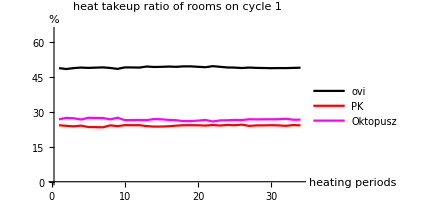
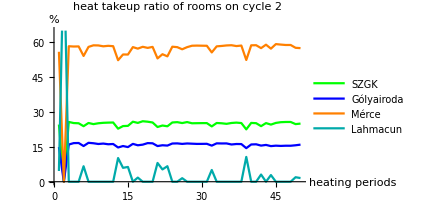
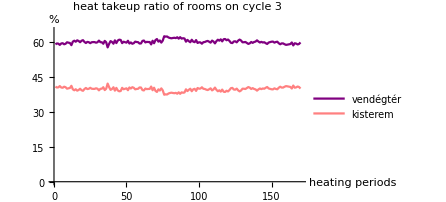

```mathematica
heatGainOrLoss=1;
plot=Quiet[Table[
ListPlot[
Transpose[Select[
Table[
Table[
If[Total[periodData]!=0,100roomPortion/Total[periodData],Nothing],
{roomPortion,periodData}],
{
periodData,
Map[
Transpose[#[[2]]][[heatGainOrLoss]]&,
Select[
heatingPeriodHeatDynamics[[cycle]],
NumberQ[Total[Transpose[#[[2]]][[heatGainOrLoss]]]]
&]]
}],Length[#]>0&]],Joined->True,PlotLegends->Placed[roomNames[[roomsByCycle[[cycle]]]],Bottom],PlotStyle->roomColors[[roomsByCycle[[cycle]]]],ImageSize->330,PlotRange->{All,{0,65}},
PlotLabel->"heat "<>{"takeup","loss"}[[heatGainOrLoss]]<>" ratio of rooms on cycle "<>ToString[cycle],
AxesLabel->{"heating\nperiods","%"}
],{cycle,1,3}]]//Row
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\heat_takeup_ratios_by_room.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\heat_takeup_ratios_by_room.png

```mathematica
roomHeatTakeupRatioDistributions=Table[Transpose[Select[
Table[
Table[
If[Total[periodData]!=0,roomPortion/Total[periodData],Nothing],
{roomPortion,periodData}],
{
periodData,
Map[
Transpose[#[[2]]][[heatGainOrLoss]]&,
Select[
heatingPeriodHeatDynamics[[cycle]],
NumberQ[Total[Transpose[#[[2]]][[heatGainOrLoss]]]]
&]]
}],Length[#]>0&]],{cycle,1,3}];
```

```mathematica
SortBy[
Flatten[Table[
Transpose[{roomsByCycle[[cycle]],Map[Mean,roomHeatTakeupRatioDistributions[[cycle]]]}],
{cycle,1,3}],1],First][[All,2]]
```

```mathematica
roomHeatTakeupRatiosRelativeToCycle={0.49133364850683514,0.24111167684793228,0.24466971474396015,0.15628253403093204,0.5625861109608646,0.6019682232026279,0.398031776797372,1,0.267555,0.03646164026424313};
```

#### szobák abszolút súlya egy körön, relatív súlya a rendszerben és ebből számolt abszolút költsége

```mathematica
roomHeatTakeupStockDaily=Table[Table[
If[
MemberQ[daysWithMissingHeatStockData,day],
None,
{seasonDays[[day]],cycleHeatingDaily[[day]][[roomToCycle[[room]]]][[2]]roomHeatTakeupRatiosRelativeToCycle[[room]]}
]
,{day,1,Length[seasonDays]}],{room,1,10}];
```

```mathematica
roomHeatTakeupRatioDaily=Quiet[Table[
Table[
If[
MemberQ[daysWithMissingHeatStockData,day],
None,
{seasonDays[[day]],roomHeatTakeupStockDaily[[room]][[day]][[2]]/Total[Transpose[roomHeatTakeupStockDaily][[day]][[All,2]]]}
]
,{day,1,Length[seasonDays]}]
,{room,1,10}]];
```

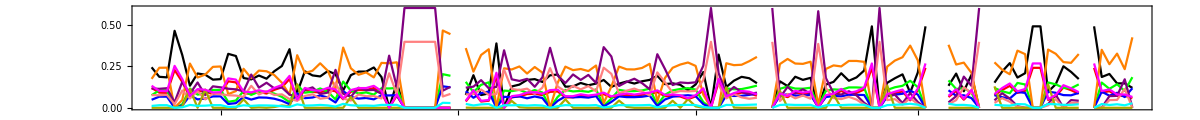

```mathematica
DateListPlot[
Map[DeleteCases[#,None]&,roomHeatTakeupRatioDaily],
PlotStyle->roomColors,PlotLegends->roomNames,ImageSize->1200,AspectRatio->0.1
]
```

```mathematica
roomHeatTakeupRatiosMonthly=Table[Transpose[
Map[
EstimateMode[
Select[#[[All,2]],NumberQ]
]&,
GatherBy[
DeleteCases[roomHeatTakeupRatioDaily[[room]],None],
#[[1]][[1]][[2]]&
]]],{room,1,10}];
```

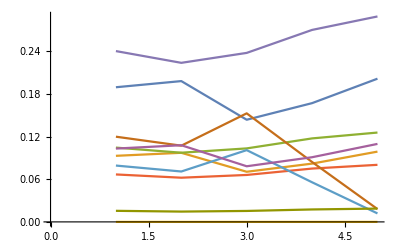

```mathematica
ListPlot[roomHeatTakeupRatiosMonthly,Joined->True]
```

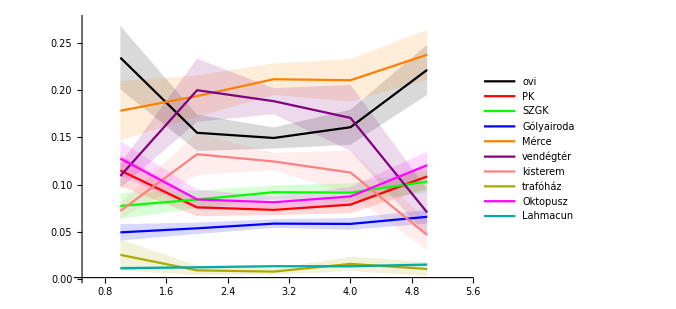

```mathematica
ErrorListPlot[
Table[Transpose[
Map[
Flatten[{
calendarMonthToSeasonMonth[[#[[1]][[1]][[1]][[2]]]],
GetMeanAndSEM[
Select[#[[All,2]],NumberQ]
]
}]&,
GatherBy[
DeleteCases[roomHeatTakeupRatioDaily[[room]],None],
#[[1]][[1]][[2]]&
]]],{room,1,10}],
roomColors,
{PlotLegends->roomNames,ImageSize->500},
{True,True,False}
]
```

```mathematica
roomHeatTakeupRatiosRelativeToSystem=Map[EstimateMode[Select[DeleteCases[#,None],NumberQ[#[[2]]]&][[All,2]]]&,roomHeatTakeupRatioDaily]
```

{0.171967,0.0843891,0.109472,0.0699253,0.251717,0.108354,0.0716457,0.,0.0936442,0.016314}

```mathematica
roomHeatTakeupRatiosRelativeToSystem={0.17196672102719981,0.0843890594403935,0.1094722209397262,0.06992527094069702,0.2517170999327754,0.10835428017647304,0.071645719823527,0.,0.09364421953240673,0.016313979615372783};
```

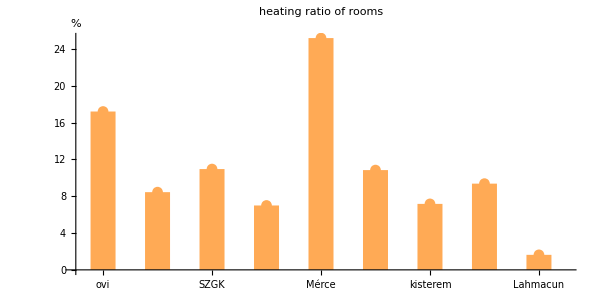

```mathematica
plot=ListPlot[
100roomHeatTakeupRatiosRelativeToSystem[[roomsWithTempData]],
PlotRange->{{0.5,9.5},All},PlotStyle->{Lighter[Orange]},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.5,ImageSize->600,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},
PlotLabel->"heating ratio of rooms",AxesLabel->{None,"%"}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\heating_ratio_of_rooms.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\heating_ratio_of_rooms.png

## szezon teljesítménye

### szobák fogyasztása

```mathematica
Select[gasBillMonthly,#[[1]]==1&]//Grid
```

1 | 1 | 2023 | 11 | 531400 | None | None
1 | 2 | 2023 | 12 | 519340 | 1116 | 465
1 | 3 | 2024 | 1 | 575200 | 1490 | 386
1 | 4 | 2024 | 2 | 312511 | 910 | 343
1 | 5 | 2024 | 3 | 267658 | 827 | 323
1 | 6 | 2024 | 4 | 147366 | 435 | 338

```mathematica
heatingGasRatio
```

0.717521

```mathematica
heatingGasRatio
```

0.717521

```mathematica
roomHeatTakeupRatiosMonthly[[room]][[1]]
```

x

```mathematica
roomsCostMonthly=Table[Table[
{seasonMonth,roomHeatTakeupRatiosMonthly[[room]][[seasonMonth]] heatingGasRatio Select[gasBillMonthly,#[[1]]==1&][[seasonMonth]][[5]]/1000}
,{seasonMonth,1,5}],{room,1,10}];
```

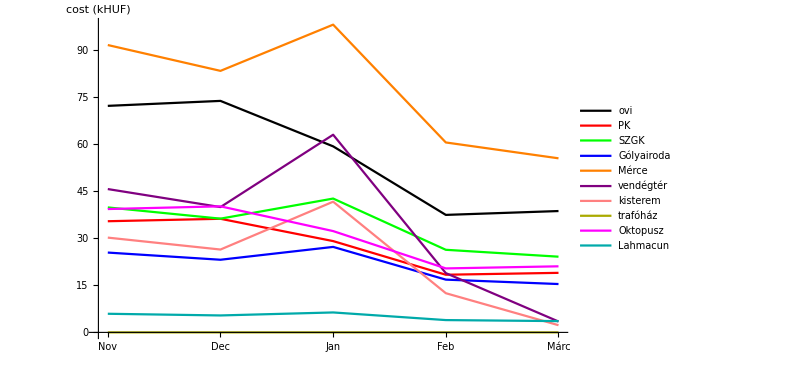

```mathematica
ListPlot[
roomsCostMonthly,
Joined->True,PlotStyle->roomColors,PlotLegends->roomNames,
ImageSize->600,AxesLabel->{None,"cost\n(kHUF)"},Ticks->{Transpose[{Range[Length[seasonMonthNames]],seasonMonthNames}],Automatic}
]
```

```mathematica
roomsCostTotal=Map[Total[#][[2]]&,roomsCostMonthly];
```

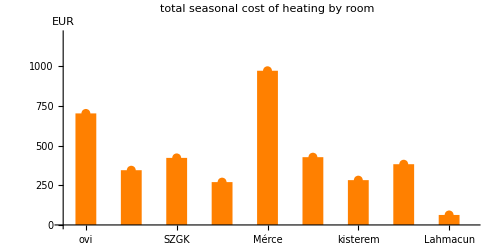

```mathematica
plot=ListPlot[
roomsCostTotal[[roomsWithTempData]]1000/400,
PlotRange->{{0.5,9.5},{0,1200}},PlotStyle->{Orange},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.5,ImageSize->500,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},
PlotLabel->"total seasonal cost of heating by room",AxesLabel->{None,"EUR"}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\total_cost_by_room.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\total_cost_by_room.png

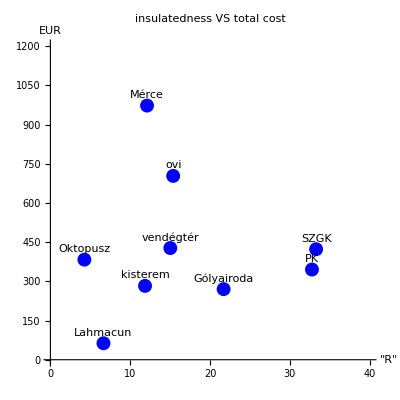

```mathematica
plotData=Select[Transpose[{
1/roomEnvelopeThermalConductivitiesPerExternalWallArea,
roomsCostTotal 1000/400,
roomNames[[1;;10]]
}],MemberQ[#,None]==False&][[roomsWithTempData]];
plot=ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"insulatedness VS total cost",PlotStyle->{PointSize->0.025,Blue},AspectRatio->1,PlotRange->{{0,40},{0,1200}},
Joined->False,AxesLabel->{"\"R\"","EUR"},
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0,40}]
}&,plotData]
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\insulatedness_vs_cost.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\insulatedness_vs_cost.png

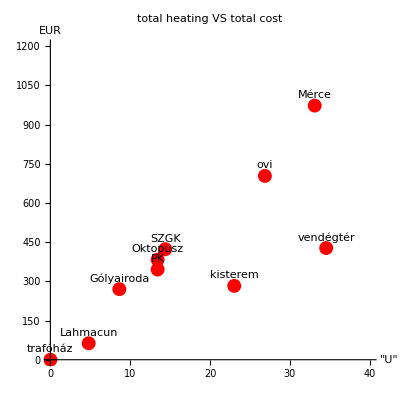

```mathematica
plotData=Select[Transpose[{
roomRadiatorThermalConductivities,
roomsCostTotal 1000/400,
roomNames[[1;;10]]
}],MemberQ[#,None]==False&];
plot=ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->"total heating VS total cost",PlotStyle->{PointSize->0.025,Red},AspectRatio->1,PlotRange->{{0,40},{0,1200}},
Joined->False,AxesLabel->{"\"U\"","EUR"},
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{0,40}]
}&,plotData]
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\heating_vs_cost.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\heating_vs_cost.png

### szobák céltartása

```mathematica
roomSetTempDiffDaily=Quiet[Table[
If[
MemberQ[roomsWithTempData,room],Table[
If[
Dimensions[roomsWithTempData[[room]][[dayN]]]!={},
Select[
Transpose[
{
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[1]],(*1 time*)
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]],(*2 room temp*)
Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]],(*3 set temp*)
Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]]-Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]],(*4 diff*)
Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]],(*5 heating state*)
5SwitchCounts[Transpose[heatingStateDaily[[dayN]][[1+roomToCycle[[room]]]]][[2]]](*6 time since heating state switched*)
}
],NumberQ[#[[2]]]&],
None
]
,{dayN,1,Length[seasonDays]}],
None],{room,1,10}]];
```

```mathematica
roomsPerformanceMetrics=Quiet[Table[Module[
{validDataPoints,heatingOn,roomIsContent,unnecessaryHeating,colderThanSetAndNoHeating,colderThanSetWithHeatingOnForSomeTime,colderThanSetWithHeatingOn},
validDataPoints=Select[Flatten[roomSetTempDiffDaily[[room]],1],Length[#]==6&];
heatingOn=Select[validDataPoints,#[[5]]==1&&60<#[[6]]&];
roomIsContent=Select[validDataPoints,#[[3]]<=#[[2]]&];
unnecessaryHeating=Select[validDataPoints,#[[5]]==1&&#[[3]]+0.7<=#[[2]]&];
colderThanSetAndNoHeating=Select[validDataPoints,#[[3]]-.5-0.2>=#[[2]]&&#[[5]]==0&&30<#[[6]]&];
colderThanSetWithHeatingOnForSomeTime=Select[validDataPoints,#[[3]]-.5-0.2>=#[[2]]&&#[[5]]==1&&30<#[[6]]&];
N[{
Length[roomIsContent]/Length[validDataPoints],(*1 szoba beállított hőmérséklet felett*)
Length[unnecessaryHeating]/Length[validDataPoints],(*2 felesleges fűtés aránya*)
Length[colderThanSetAndNoHeating]/Length[validDataPoints],(*3 rendszer nem válaszol aránya*)
Length[colderThanSetWithHeatingOnForSomeTime]/Length[validDataPoints](*4 rendszer elégtelen aránya*)
}]
],{room,1,10}]];
roomPerformanceMetricsNames={"room above set temp","unnecessary heating","no heating when cold","insufficient heating"};
roomPerformanceMetricsColors={Pink,Darker[Red],Lighter[Blue],Purple};
```

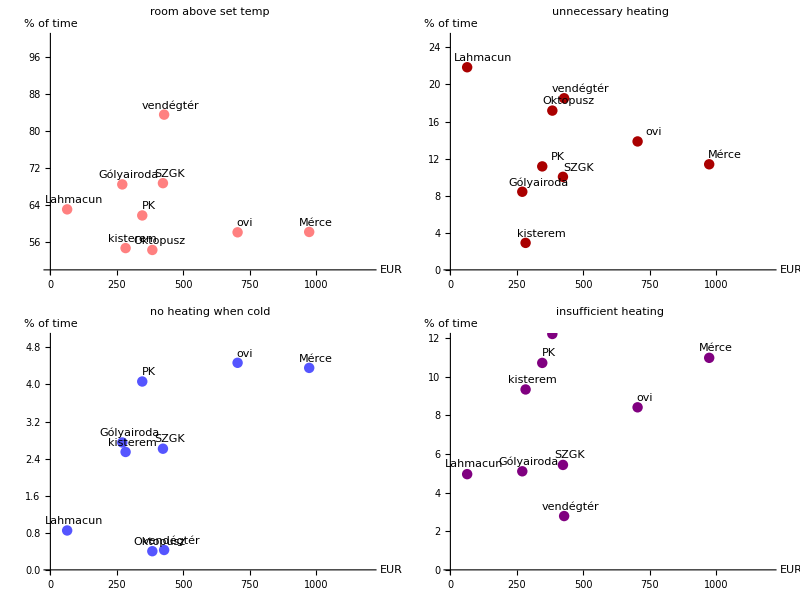

```mathematica
Table[
Module[
{plotData},
plotData=Select[Transpose[{
roomsCostTotal(1000/400),
100Transpose[roomsPerformanceMetrics][[metric]],
roomNames[[1;;10]]
}],MemberQ[#,None]==False&][[roomsWithTempData]];
ListPlot[
Transpose[Transpose[plotData][[{1,2}]]],
PlotLabel->roomPerformanceMetricsNames[[metric]],PlotStyle->{PointSize->0.025,roomPerformanceMetricsColors[[metric]]},AspectRatio->1,PlotRange->{{0,1200},{{50,100},{0,25},{0,5},{0,12}}[[metric]]},
Joined->False,AxesLabel->{"EUR","% of time"},ImageSize->300,
Epilog->Map[{
Text[#[[3]],#[[{1,2}]]+{{25,2},{60,1},{26,0.2},{25,0.5}}[[metric]]]
}&,plotData]
]
],{metric,1,4}]//ArrayReshape[#,{2,2}]&//Grid
```

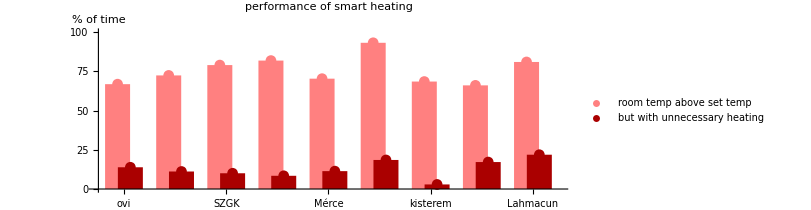

```mathematica
plot=ListPlot[
{
Transpose[{Range[9]-0.125,100Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[1]]}],
Transpose[{Range[9]+0.125,100Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[2]]}]
},
PlotRange->{{0.5,9.5},{0,100}},PlotStyle->{Pink,Darker[Red]},Filling->Axis,FillingStyle->{Thickness[0.03]},ImageSize->600,AspectRatio->0.35,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},
PlotLabel->"performance of smart heating",AxesLabel->{None,"% of time"},PlotLegends->Placed[{"room temp above set temp","but with unnecessary heating"},Bottom]
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\smart_heating_performance.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\smart_heating_performance.png

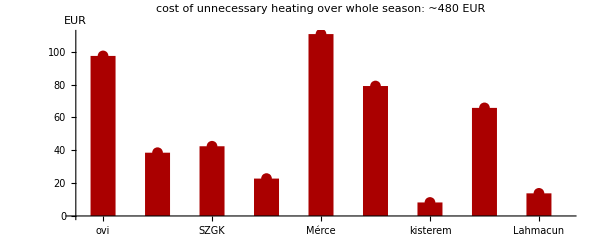

```mathematica
plot=ListPlot[
Transpose[{Range[9],(1000/400)roomsCostTotal[[roomsWithTempData]]Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[2]]}],
PlotRange->{{0.5,9.5},All},PlotStyle->{Darker[Red]},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.4,ImageSize->600,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},
PlotLabel->"cost of unnecessary heating over whole season: ~"<>ToString[Round[1000Total[roomsCostTotal[[roomsWithTempData]]Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[2]]]/400,10]]<>" EUR",AxesLabel->{None,"EUR"}
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\cost_of_unnecessary_heating.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\cost_of_unnecessary_heating.png

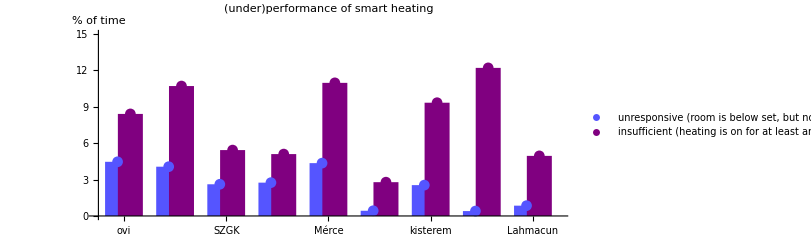

```mathematica
plot=ListPlot[
{
Transpose[{Range[9]-0.125,100Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[3]]}],
Transpose[{Range[9]+0.125,100Transpose[roomsPerformanceMetrics[[roomsWithTempData]]][[4]]}]
},
PlotRange->{{0.5,9.5},{0,15}},PlotStyle->{Lighter[Blue],Purple},Filling->Axis,FillingStyle->{Thickness[0.03]},AspectRatio->0.4,ImageSize->600,
Ticks->{Transpose[{Range[9],Map[Rotate[#,Pi/4]&,roomNames[[roomsWithTempData]]]}],Automatic},
PlotLabel->"(under)performance of smart heating",AxesLabel->{None,"% of time"},PlotLegends->Placed[{"unresponsive (room is below set, but no heating for at least 30 minutes)","insufficient (heating is on for at least an hour but room is still below set)"},Bottom]
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\underperformance_of_smart_heating.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\underperformance_of_smart_heating.png

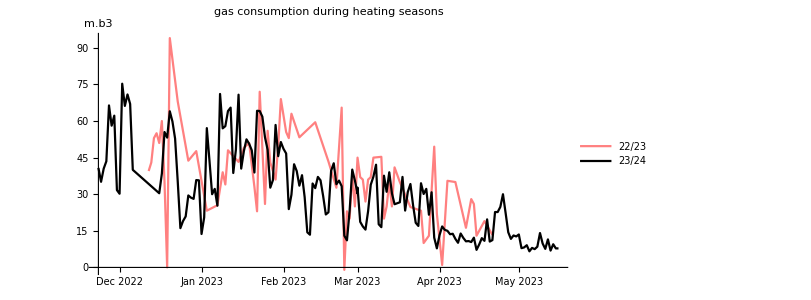

```mathematica
plot=DateListPlot[{
gasFlow2223DailyTotals,
Map[
{
DatePlus[#[[1]],{-1,"Year"}],
#[[2]]
}&,
Select[Map[{#[[1]][[1]],#[[-1]][[2]]}&,DeleteCases[gasStockDaily,None]],#[[2]]<150&]
]
},Joined->True,PlotRange->All,PlotStyle->{{Thick,Pink},{Thick,Black}},PlotLegends->Placed[{"22/23","23/24"},Bottom],ImageSize->600,AspectRatio->0.5,
PlotLabel->"gas consumption during heating seasons",AxesLabel->{None,"m.b3"},Axes->{True,True},Frame->False
]
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\gas_consumption_by_season.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\gas_consumption_by_season.png

```mathematica
roomResponseCurves=Quiet[Table[
Module[
{validDataPoints,heatingOn,heatingOnByTimeSinceHeatingOn},
validDataPoints=Select[Flatten[roomSetTempDiffDaily[[room]],1],Length[#]==6&];
heatingOn=Select[
validDataPoints,
#[[5]]==1&
];
heatingOnByTimeSinceHeatingOn=GatherBy[
SortBy[heatingOn,Last],
#[[6]]&];
Transpose[
Select[Map[
Flatten[{
#[[1]][[6]],
GetMeanAndSEM[Select[#[[All,2]],NumberQ]]
}]&,
heatingOnByTimeSinceHeatingOn
],Length[#]==3&]
]]
,{room,1,10}]];
```

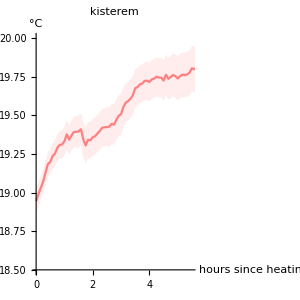
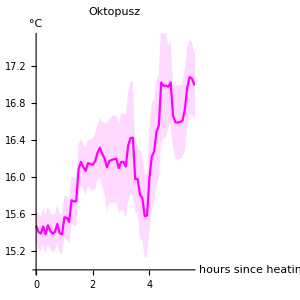
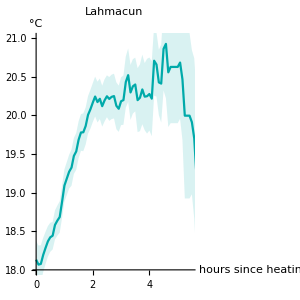

```mathematica
hoursToPlot=5.5;
plot=Table[
ErrorListPlot[
roomResponseCurves[[{room}]],
roomColors[[{room}]],
{
PlotRange->{
{0,hoursToPlot 60},
{
Floor[Min[Select[Transpose[roomResponseCurves[[room]]],#[[1]]<hoursToPlot 60&][[All,2]]],0.5],Ceiling[Max[Select[Transpose[roomResponseCurves[[room]]],#[[1]]<hoursToPlot 60&][[All,2]]],0.5]
}
},PlotLabel->roomNames[[room]],ImageSize->300,AspectRatio->1,
AxesOrigin->{0,Floor[Min[Select[Transpose[roomResponseCurves[[room]]],#[[1]]<hoursToPlot 60&][[All,2]]],0.5]},
Ticks->{Map[{60 #,#}&,Range[0,hoursToPlot]],Automatic},AxesLabel->{"hours since\nheating start","°C"}
},
{True,True,False}
],{room,{7,9,10}}]//Row
```

```mathematica
Export[NotebookDirectory[]<>"\\DUT\\room_response_curves_3.png",plot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazankontroll-dashboard\analysis\\DUT\room_response_curves_3.png

### költség vs komfort

```mathematica
roomHeatVsTempDiffDaily=Table[
If[
MemberQ[roomsWithTempData,room],
Select[
Quiet[Transpose[{
Map[
If[
 Dimensions[#]!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
gasPricePerCubicMeter Total[Transpose[#][[2]]]/(energyContentInGasPerCubicMeter boilerEfficiencyEstimate)
},
None
]&,
roomHeatTakeupDaily[[room]]],
Map[
If[
Dimensions[#]!={}&&#!={},
{
NormalizeDate[Transpose[#][[1]][[1]]],
Mean[Select[Transpose[Transpose[#][[{2,3}]]],#[[2]]==1&]][[1]]
},
None
]&,
roomSetTempDiffDaily[[room]]]
}]],
Dimensions[#[[1]]]!={}&&Dimensions[#[[2]]]!={}&
],
None
],{room,1,10}];
```

```mathematica
extTBinWidth=3;
roomPerformanceExternalTempBins=Table[
If[
MemberQ[roomsWithTempData,room],
Module[
{roomPerformaceCharacteristics,externalTempRange,binnedData},
roomPerformaceCharacteristics=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
externalTempRange=MinMax[Transpose[roomPerformaceCharacteristics][[3]]];
binnedData=Select[Quiet[Table[
{
extT+extTBinWidth,
Transpose[Transpose[Select[roomPerformaceCharacteristics,Between[#[[1]],{extT,extT+extTBinWidth}]&]][[{2,3}]]]
}
,{extT,Floor[externalTempRange[[1]],1],Ceiling[externalTempRange[[2]],1],extTBinWidth}]],NumberQ[Total[Flatten[#]]]&]
],
None
],{room,1,10}];
```

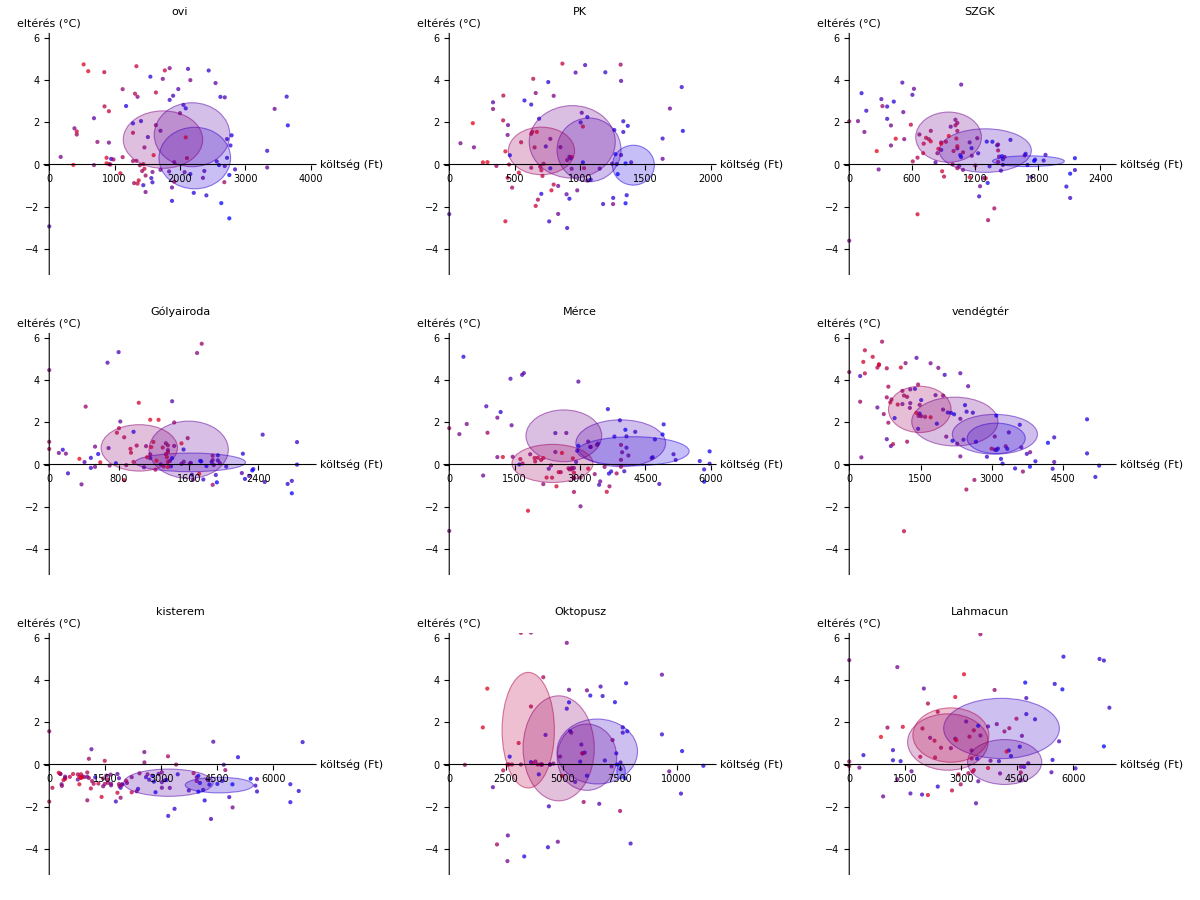

```mathematica
Quiet[Table[
ListPlot[
{},
PlotLabel->roomNames[[room]],
AxesLabel->{Rotate["költség (Ft)",Pi/2],"eltérés (°C)"},
ImageSize->350,
PlotRange->{
{0,
Ceiling[Max[
Map[
#[[1]][[2]]&,
roomHeatVsTempDiffDaily[[room]]]
],500]
},
{-5,6}
},AspectRatio->1,
Prolog->{
Table[
{
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.25
],
EdgeForm[
{
Thick,Dashed,
RGBColor[
(binData[[1]]+3)/(21-3),
0,
1-(binData[[1]]+3)/(21-3),
0.5
]
}
],
Ellipsoid[
GetMeanAndSD[binData[[2]]][[1]],
GetMeanAndSD[binData[[2]]][[2]]0.75
]
},{binData,roomPerformanceExternalTempBins[[room]]}
],
Map[
{
RGBColor[
(#[[1]]+3)/(21-3),
0,
1-(#[[1]]+3)/(21-3),
0.75
],
PointSize->0.0125,
Point[#[[{2,3}]]]
}&,
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]],
#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
]
}
],{room,roomsWithTempData}]]//ArrayReshape[#,{3,3}]&//Grid
```

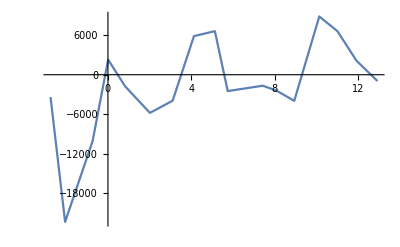
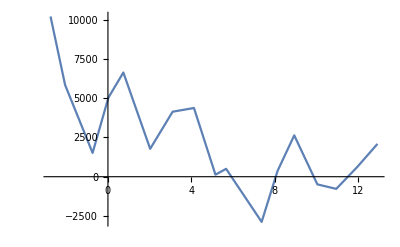
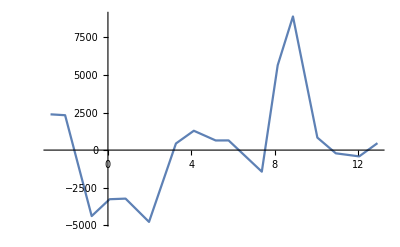
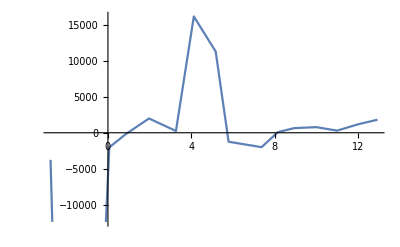
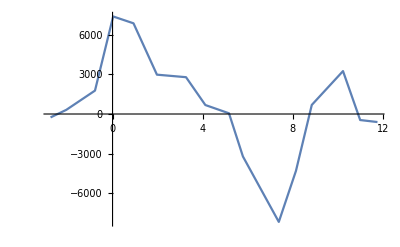
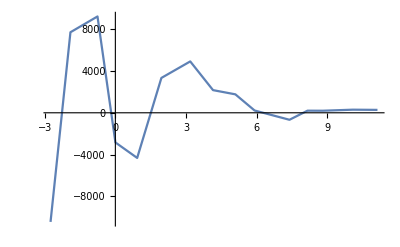
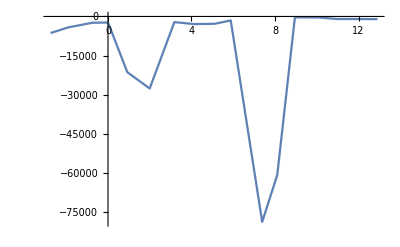
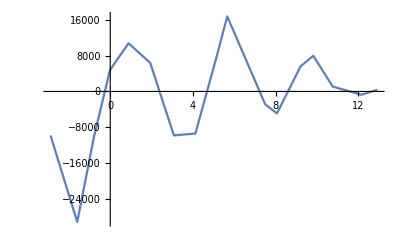

```mathematica
binWidth=2;
binStep=1;
Table[
ListPlot[
Module[
{dataToBin,binRange},
dataToBin=Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&];
binRange=MinMax[Transpose[dataToBin][[1]]];
Table[
Mean[Select[dataToBin,Between[#[[1]],{bin-binWidth/2,bin+binWidth/2}]&]]
,{bin,binRange[[1]],binRange[[2]],binStep}]
],Joined->True
],{room,roomsWithTempData}]
```

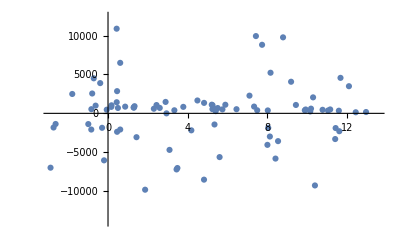
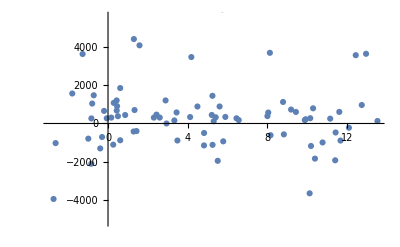
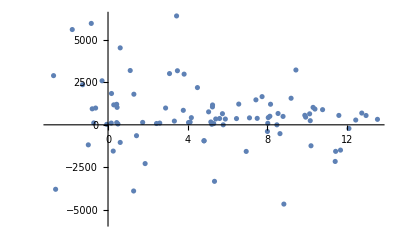
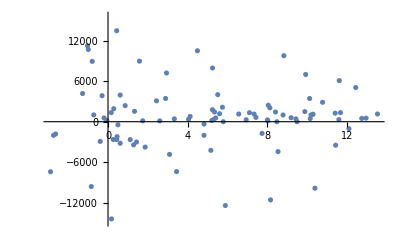
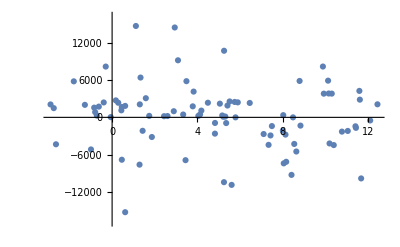
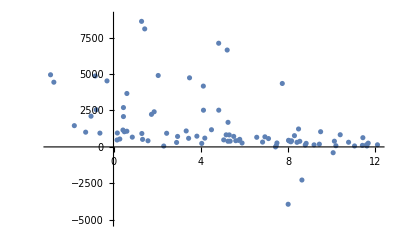
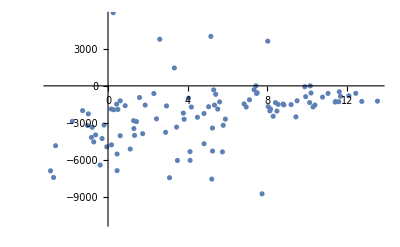
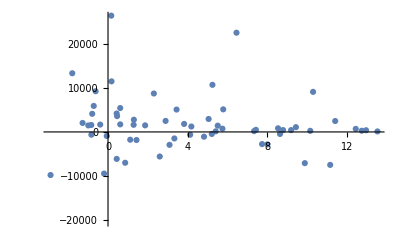

```mathematica
Table[
ListPlot[
Select[Quiet[Map[
{
Mean[Transpose[externalTempDaily[[Position[Map[NormalizeDate,seasonDays],#[[1]][[1]]][[1]][[1]]]]][[2]]],
#[[1]][[2]]/#[[2]][[2]]
}
&,roomHeatVsTempDiffDaily[[room]]]],NumberQ[Total[#]]&]
],{room,roomsWithTempData}]
```

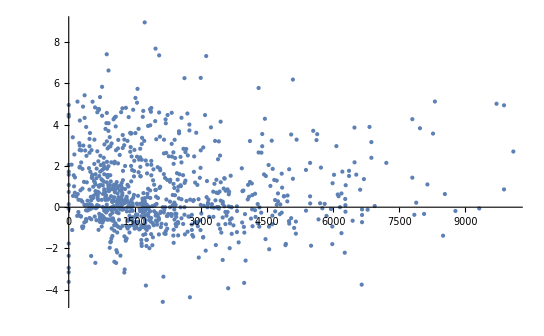

```mathematica
ListPlot[
Flatten[Table[
Select[Map[
{
#[[1]][[2]],
Quiet[#[[2]][[2]]]
}
&,roomHeatVsTempDiffDaily[[room]]],NumberQ[Total[#]]&]
,{room,roomsWithTempData}],1]
]
```

## szimuláció

- megnézni azt is, hogy a nem outlierek közti különbségek miből eredhetnek

## dev

### functions

#### core

```mathematica
SetSimulationParameters[]:={
startTimeBin=1;
timeScaling= 1/(60);
dt=5;
tStart=dt startTimeBin;
tEnd=24 60;
};
```

```mathematica
SetSimulatedCycle[cycleToSet_]:={
cycle=cycleToSet;
roomsOnCycle=Flatten[Position[roomToCycle,cycleToSet]];
roomEnvelopeThermalConductivity=Table[roomEnvelopeThermalConductivities[[room]],{room,roomsOnCycle}];
roomRadiatorThermalConductivity=Table[roomRadiatorThermalConductivities[[room]],{room,roomsOnCycle}];
roomHeatCapacity=Table[roomAreas[[room]]roomHeight airSpecificMass airSpecificHeatCapacity,{room,roomsOnCycle}];
};
```

```mathematica
SetSimulatedDay[dayNToSet_,roomsSetTempIn_,roomsLowerBufferIn_,roomsUpperBufferIn_,roomsTempStartIn_,heatingStateStartIn_]:={
dayN=dayNToSet;
roomsSetTemp=roomsSetTempIn;
roomsLowerBuffer=roomsLowerBufferIn;
roomsUpperBuffer=roomsUpperBufferIn;
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=roomsTempStartIn;
heatingStateStart=heatingStateStartIn;
};
```

```mathematica
SimulateDayForCycle[warmingCorrection_,coolingCorrection_]:=
Module[
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp},
Quiet[
simulation=Module[
{roomsTemp,roomsTempList,heatingState,heatingStateList,radiatorState,radiatorStateList,τStart,τEnd,dτ},
roomsTemp=roomsTempStart;
heatingState=heatingStateStart;
radiatorState=Table[heatingState,{roomN,1,Length[roomsOnCycle]}];
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

roomsTempList=Table[{},{roomN,1,Length[roomsOnCycle]}];
heatingStateList={};
radiatorStateList=Table[{},{roomN,1,Length[roomsOnCycle]}];
Table[
Module[
{heatingStateVotes},
heatingStateVotes=
Table[
Module[
{warmingPower,coolingPower,dRoomTemp,heatingStateVote},

roomsTempList[[roomN]]=If[
roomsTempList[[roomN]]=={},
{{timeScaling τ,roomsTemp[[roomN]]}},
Join[roomsTempList[[roomN]],{{timeScaling τ,roomsTemp[[roomN]]}}]
];

radiatorStateList[[roomN]]=If[
radiatorStateList[[roomN]]=={},
{{timeScaling τ,radiatorState[[roomN]]}},
Join[radiatorStateList[[roomN]],{{timeScaling τ,radiatorState[[roomN]]}}]
];

warmingPower=heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]roomRadiatorThermalConductivity[[roomN]](HeatingCurve[externalTemp[timeScaling τ],heatingWaterMax,heatingWaterMin]-roomsTemp[[roomN]]);
coolingPower=coolingCorrection[[roomsOnCycle[[roomN]]]]roomEnvelopeThermalConductivity[[roomN]](roomsTemp[[roomN]]-externalTemp[timeScaling τ]);

radiatorState[[roomN]]=If[roomsRadiatorOffTemp[[roomsOnCycle[[roomN]]]]<roomsTemp[[roomN]],0,If[20.5>roomsTemp[[roomN]],1,radiatorState[[roomN]]]];

dRoomTemp=dτ (radiatorState[[roomN]] warmingPower-coolingPower)/roomHeatCapacity[[roomN]];

roomsTemp[[roomN]]+=dRoomTemp;
heatingStateVote=If[
roomsTemp[[roomN]]<roomsSetTemp[[roomN]][timeScaling τ]-roomsLowerBuffer[[roomN]][timeScaling τ]&&dRoomTemp<0,
1,
If[
roomsTemp[[roomN]]>roomsSetTemp[[roomN]][timeScaling τ]+roomsUpperBuffer[[roomN]][timeScaling τ]&&dRoomTemp>0,
0,
heatingState
]
];
heatingStateVote
]
,{roomN,1,Length[roomsOnCycle]}];

heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

heatingState=Max[heatingStateVotes]

]
,{τ,τStart,τEnd,dτ}];
{
heatingStateList,
roomsTempList,
radiatorStateList
}
];
simulatedHeatDynamics=Table[Module[
{roomTemp,heatingState,radiatorState,externalTemp,tempDiffExt,tempDiffHeater,heatLoss,heatGain},
roomTemp=Transpose[simulation[[2]][[roomN]]][[2]];
heatingState=Transpose[simulation[[1]]][[2]];
radiatorState=Transpose[simulation[[3]][[roomN]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp;
heatLoss=coolingCorrection[[roomsOnCycle[[roomN]]]]tempDiffExt roomEnvelopeThermalConductivity[[roomN]];
heatGain=heatScalingFactors[[cycle]]radiatorState heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]tempDiffHeater roomRadiatorThermalConductivity[[roomN]];
{
heatLoss,
heatGain
}
],{roomN,1,Length[roomsOnCycle]}];
heatingSimulatedState=Interpolation[simulation[[1]],InterpolationOrder->1];
roomSimulatedTemp=Table[Interpolation[simulation[[2]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}];
];
{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp
}
]
```

#### spec

```mathematica
SetSimulatedDayForComparison[dayNToSet_,roomsTempStartIn_,heatingStateStartIn_]:={
dayN=dayNToSet;
heatingTrueState=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[heatingStateDaily[[dayNToSet]][[1+cycle]],#[[2]]!="n"&]
],
InterpolationOrder->0
];
roomsSetTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayNToSet]][[2]],#[[2]]!="n"&]
],
InterpolationOrder->0
],{room,roomsOnCycle}];
roomsLowerBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayN]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayN]][[3]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomsUpperBuffer=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[roomTempsDaily[[room]][[dayNToSet]][[4]],#[[2]]!="n"&]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
roomsTrueTemp=Table[
Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,roomTempsDaily[[room]][[dayNToSet]][[1]]
],
InterpolationOrder->0
]
,{room,roomsOnCycle}];
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=Quiet[Table[
If[NumberQ[roomsTempStartIn[[roomN]]],roomsTempStartIn[[roomN]],First[DeleteCases[Map[roomsTrueTemp[[roomN]],Range[0,24 60,5]],"n"]]
],{roomN,1,Length[roomsOnCycle]}]];
heatingStateStart=If[NumberQ[heatingStateStartIn],heatingStateStartIn,Transpose[heatingStateDaily[[dayNToSet]][[1+cycle]]][[2]][[1]]];
};
```

```mathematica
SetSimulatedDayWithTimedHeating[dayNToSet_,roomsSchedulesIn_,roomsTempStartIn_,radiatorStateStartIn_]:={
dayN=dayNToSet;
roomSchedules=roomsSchedulesIn;
externalTemp=Interpolation[
Map[
{
DateDifference[DateList[NormalizeDate[seasonDays[[dayNToSet]]]],#[[1]],"Minute"][[1]],
#[[2]]
}&
,Select[externalTempDaily[[dayNToSet]],#[[2]]!="n"&]
],
InterpolationOrder->1
];
roomsTempStart=roomsTempStartIn;
heatingStateStart=0;
radiatorStateStart=radiatorStateStartIn;
};
```

```mathematica
SimulateDayForCycleWithTimedHeating[warmingCorrection_,coolingCorrection_]:=
Module[
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp,radiatorSimulatedState},
Quiet[
simulation=Module[
{roomsTemp,roomsTempList,heatingState,heatingStateList,radiatorState,radiatorStateList,τStart,τEnd,dτ},
roomsTemp=roomsTempStart;
heatingState=heatingStateStart;
radiatorState=radiatorStateStart;
τStart=tStart/timeScaling;
τEnd=tEnd/timeScaling;
dτ=dt/timeScaling;

radiatorStateList=Table[{},{roomN,1,Length[roomsOnCycle]}];
roomsTempList=Table[{},{roomN,1,Length[roomsOnCycle]}];
heatingStateList={};
Table[
Module[
{heatingStateVotes},
heatingStateVotes=
Table[
Module[
{warmingPower,coolingPower,dRoomTemp,heatingStateVote},

roomsTempList[[roomN]]=If[
roomsTempList[[roomN]]=={},
{{timeScaling τ,roomsTemp[[roomN]]}},
Join[roomsTempList[[roomN]],{{timeScaling τ,roomsTemp[[roomN]]}}]
];

radiatorStateList[[roomN]]=If[
radiatorStateList[[roomN]]=={},
{{timeScaling τ,radiatorState[[roomN]]}},
Join[radiatorStateList[[roomN]],{{timeScaling τ,radiatorState[[roomN]]}}]
];

If[
8 60<timeScaling τ<20 60,
radiatorState[[roomN]]=If[roomsRadiatorOffTemp[[roomsOnCycle[[roomN]]]]<roomsTemp[[roomN]],0,If[20.5>roomsTemp[[roomN]],1,radiatorState[[roomN]]]];
];

warmingPower=heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]roomRadiatorThermalConductivity[[roomN]](HeatingCurve[externalTemp[timeScaling τ],heatingWaterMax,heatingWaterMin]-roomsTemp[[roomN]]);
coolingPower=coolingCorrection[[roomsOnCycle[[roomN]]]]roomEnvelopeThermalConductivity[[roomN]](roomsTemp[[roomN]]-externalTemp[timeScaling τ]);

dRoomTemp=dτ (radiatorState[[roomN]] warmingPower-coolingPower)/roomHeatCapacity[[roomN]];

roomsTemp[[roomN]]+=dRoomTemp;
heatingStateVote=roomSchedules[[roomN]][timeScaling τ];
heatingStateVote
]
,{roomN,1,Length[roomsOnCycle]}];

heatingStateList=If[
heatingStateList=={},
{{timeScaling τ,heatingState}},
Join[heatingStateList,{{timeScaling τ,heatingState}}]
];

heatingState=Max[heatingStateVotes]

]
,{τ,τStart,τEnd,dτ}];
{
heatingStateList,
roomsTempList,
radiatorStateList
}
];
simulatedHeatDynamics=Table[Module[
{roomTemp,heatingState,radiatorState,externalTemp,tempDiffExt,tempDiffHeater,heatLoss,heatGain},
roomTemp=Transpose[simulation[[2]][[roomN]]][[2]];
heatingState=Transpose[simulation[[1]]][[2]];
radiatorState=Transpose[simulation[[3]][[roomN]]][[2]];
externalTemp=Transpose[externalTempDaily[[dayN]]][[2]];
tempDiffExt=roomTemp-externalTemp;
tempDiffHeater=Map[HeatingCurve[#,heatingWaterMax,heatingWaterMin]&,Transpose[externalTempDaily[[dayN]]][[2]]]-roomTemp;
heatLoss=coolingCorrection[[roomsOnCycle[[roomN]]]]tempDiffExt roomEnvelopeThermalConductivity[[roomN]];
heatGain=heatScalingFactors[[cycle]]radiatorState heatingState warmingCorrection[[roomsOnCycle[[roomN]]]]tempDiffHeater roomRadiatorThermalConductivity[[roomN]];
{
heatLoss,
heatGain
}
],{roomN,1,Length[roomsOnCycle]}];
heatingSimulatedState=Interpolation[simulation[[1]],InterpolationOrder->1];
roomSimulatedTemp=Table[Interpolation[simulation[[2]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}];
radiatorSimulatedState=Table[Interpolation[simulation[[3]][[roomN]],InterpolationOrder->1],{roomN,1,Length[roomsOnCycle]}]
];
{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp,
radiatorSimulatedState
}
]
```

### model fitting via genetic algorithm

#### functions

```mathematica
EvaluateParameterVector[warmingParams_,coolingParams_]:=Module[
{warmingCorrection,coolingCorrection,simulation,simulatedHeatDynamics,heatingSimulatedState,roomSimulatedTemp,tempSimulationError,heatSimulationError},
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};

Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];

{
simulation,
simulatedHeatDynamics,
heatingSimulatedState,
roomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];

tempSimulationError=Table[
Mean[Select[
Table[
Abs[roomSimulatedTemp[[roomN]][t]-roomsTrueTemp[[roomN]][t]]
,{t,0,24 60,5}]
,NumberQ]]
,{roomN,1,Length[roomsOnCycle]}];
heatSimulationError=Join[
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]-100heatStockDaily[[cycle]][[dayN]][[-1]][[2]];
{
warmingCorrection,(*1*)
coolingCorrection,(*2*)
simulation,(*3*)
simulatedHeatDynamics,(*4*)
heatingSimulatedState,(*5*)
roomSimulatedTemp,(*6*)
tempSimulationError,(*7*)
heatSimulationError(*8*)
}
]
```

```mathematica
FitnessFunction[individual_,tempErrorWeight_,heatErrorWeight_,heatMeasureType_]:=Module[
{chromosomeLength,simulationResults},
chromosomeLength=Length[individual];
simulationResults=EvaluateParameterVector[
individual[[1;;chromosomeLength/2]],
individual[[chromosomeLength/2+1;;chromosomeLength]]
];
1/((tempErrorWeight Total[Abs[simulationResults[[-2]]]]+heatErrorWeight Abs[simulationResults[[-1]][[heatMeasureType]]])/100)
]
```

```mathematica
GenerateNewPopulation[
FitnessFunction_,tempErrorWeight_,heatErrorWeight_,heatMeasureType_,
population_,
tournamentSize_,tournamentWinnerNumber_,tournamentRounds_,
mutationMagnitude_
]:=
Module[
{chromosomeLength,populationFitness,parents,offspring,offspringFitness,newPopulation},
chromosomeLength=Length[population[[1]]];

populationFitness=Map[FitnessFunction[#,tempErrorWeight,heatErrorWeight,heatMeasureType]&,population];

parents=population[[Flatten[Table[Map[
Position[populationFitness,#]
&,Reverse[Sort[RandomSample[populationFitness,tournamentSize]]][[1;;tournamentWinnerNumber]]
],{round,1,tournamentRounds}]]]];

offspring=Flatten[Table[Table[
Module[
{crossoverPoint,child},
crossoverPoint=RandomInteger[{1,chromosomeLength-1}];
child=Clip[
Flatten[{
p1[[1;;crossoverPoint]],
p2[[crossoverPoint+1;;-1]]
}]+RandomReal[{-mutationMagnitude,mutationMagnitude},chromosomeLength]
,{0,Infinity}]
],{p2,parents}],{p1,parents}],1];
offspringFitness=Map[FitnessFunction[#,tempErrorWeight,heatErrorWeight,heatMeasureType]&,offspring];
newPopulation=Sort[Flatten[{population,offspring},1]][[-Length[population];;-1]];
{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}
]
```

#### fit for multiple days cycle 2

```mathematica
daysToFit={34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128};
```

##### calc fit

calc

```mathematica
SetSimulatedCycle[2];
SetSimulationParameters[];
```

```mathematica
tournamentSize=10;
tournamentWinnerNumber=3;
tournamentRounds=4;
mutationMagnitude=0.1;
```

```mathematica
initialPopulationSize=30;
chromosomeLength=8;
```

```mathematica
daysToFitCandidates=Range[30,125,5]+3;
dataExistenceCheck=Map[
Quiet[{#,Check[SetSimulatedDayForComparison[#,ConstantArray[None,Length[roomsOnCycle]],None],"error"]}]&,
daysToFitCandidates];
errorDays=daysToFitCandidates[[Transpose[Position[dataExistenceCheck,"error"]][[1]]]];
daysToFit=Complement[daysToFitCandidates,errorDays];
```

```mathematica
daysToFit={34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128};
```

```mathematica
dayFitResults={};
numOfGenerations=30;
tempErrorWeight=1;
heatErrorWeight=0;heatMeasureType=2;
Table[
dayN=daysToFit[[dayNN]];
startPopulation=Table[RandomReal[{0,2},chromosomeLength],{n,1,initialPopulationSize}];
Module[
{evolution},
Echo[DateString[Date[]]<>": starting "<>DateString[NormalizeDate[seasonDays[[dayN]]]]];
SetSimulatedDayForComparison[dayN,ConstantArray[None,Length[roomsOnCycle]],None];
evolution=Module[
{generations,population,newGeneration,newPopulation},
generations={};
Table[
If[
Mod[g,5]==0,
Echo[DateString[Date[]]<>": starting generation "<>ToString[g]];
];
If[g==1,population=startPopulation,population=generations[[-1]][[-1]]];
newGeneration=GenerateNewPopulation[
FitnessFunction,tempErrorWeight,heatErrorWeight,heatMeasureType,
population,
tournamentSize,tournamentWinnerNumber,tournamentRounds,
mutationMagnitude
];
If[g==1,generations={newGeneration},generations=Join[generations,{newGeneration}]];
,{g,1,numOfGenerations}];
generations
];
If[dayFitResults=={},dayFitResults={evolution},dayFitResults=Join[dayFitResults,{evolution}]];
Export[NotebookDirectory[]<>"\\ga_2.mx",dayFitResults];
]
,{dayNN,{1,4,7}}]
```

Wed 26 Jun 2024 18:42:48: starting Mon 11 Dec 2023

Wed 26 Jun 2024 18:43:34: starting generation 5

Wed 26 Jun 2024 18:44:29: starting generation 10

Wed 26 Jun 2024 18:45:23: starting generation 15

Wed 26 Jun 2024 18:46:17: starting generation 20

Wed 26 Jun 2024 18:47:11: starting generation 25

Wed 26 Jun 2024 18:48:05: starting generation 30

Wed 26 Jun 2024 18:48:16: starting Sun 24 Dec 2023

$Aborted

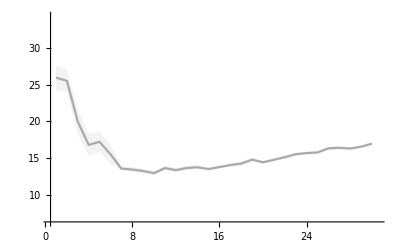

```mathematica
ErrorListPlot[
Table[Transpose[Table[
Flatten[{g,GetMeanAndSEM[100 /dayFitResults[[fittedDay]][[g]][[1]]]}]
,{g,1,30}]],{fittedDay,1,Length[dayFitResults]}],
Map[GrayLevel[1/(Length[dayFitResults]+2)+#/(Length[dayFitResults]+2)]&,Range[Length[dayFitResults]]],
{},
{True,True,False}
]
```

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}]
```

{{{9.8562,{2.02697,0.68016,0.742843,0.254999,1.71026,1.00485,1.18626,0.599588}},{9.7294,{2.12527,0.639153,0.817495,0.236023,1.75992,0.926417,1.22594,0.641915}},{9.62869,{1.93311,0.712787,0.726963,0.216066,1.70947,0.996493,1.86939,0.473319}},{9.4727,{2.10364,0.744541,0.793198,0.273052,1.61731,1.38753,1.23175,0.720552}},{9.21944,{2.2124,0.572339,0.736379,0.221582,1.79995,0.886868,1.16018,0.721562}}}}

```mathematica
Mean[Map[#[[2]]&,bestFiveFromEachDay[[1]]]]
```

{2.08028,0.669796,0.763376,0.240345,1.71938,1.04043,1.3347,0.631387}

```mathematica
(*Export[NotebookDirectory[]<>"\\ga_1.mx",dayFitResults];*)
```

best fits for each day fitted

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}];
```

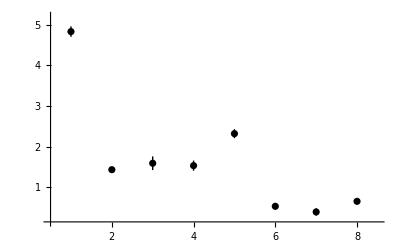

```mathematica
ErrorListPlot[
{
Join[
{Range[8]},
GetMeanAndSEM[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]]
]
},
{Black},
{},
{False,False,True}
]
```

```mathematica
bestFitMeansOverall=Mean[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]];
```

seasonal trends in correction?

```mathematica
(*{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}*)
```

```mathematica
seasonalCorrector=Mean[Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-20;;-1]]][[2]]]
,{fittedDayN,1,Length[daysToFit]}]]];
```

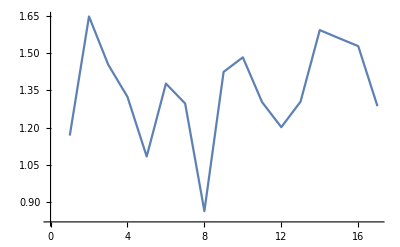

```mathematica
ListPlot[seasonalCorrector,Joined->True]
```

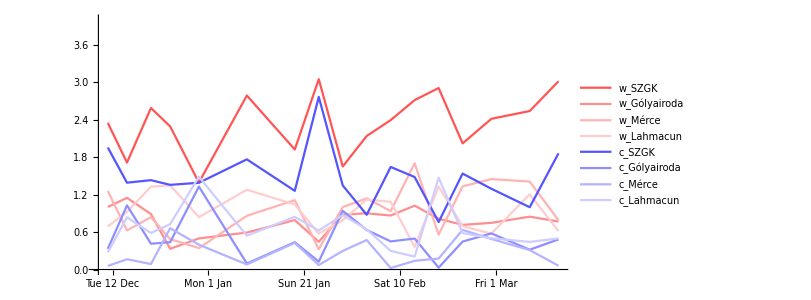

```mathematica
ListPlot[
Transpose[Table[
Transpose[{
ConstantArray[daysToFit[[fittedDayN]],8],
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
}]
,{fittedDayN,1,Length[daysToFit]}]],
Joined->True,PlotStyle->Flatten[{Map[Nest[Lighter,Red,#]&,Range[1,4]],Map[Nest[Lighter,Blue,#]&,Range[1,4]]}],
PlotLegends->Flatten[{Map["w_"<>#&,roomNames[[roomsOnCycle]]],Map["c_"<>#&,roomNames[[roomsOnCycle]]]}],
ImageSize->600,AspectRatio->0.5,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{0,4}}
]
```

```mathematica
seasonCorrectedBestFits=Map[Mean,Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
,{fittedDayN,1,Length[daysToFit]}]]]
```

```mathematica
seasonCorrectedBestFits={2.3480290895305607,0.7801014999645991,0.9513837546933651,0.9297576319359259,1.4780859968954623,0.5046262989177167,0.2679036077336363,0.6731878383370469}
```

{2.34803,0.780101,0.951384,0.929758,1.47809,0.504626,0.267904,0.673188}

##### eval fit

for one day

```mathematica
bestFitMeansOverall={3.1725563115559083,1.0683009750379302,1.29468510022947,1.278422223763722,1.9544085048287771,0.6946838470957711,0.3455993563985235,0.9222435820921898};
```

```mathematica
individual=bestFitMeansOverall
```

{4.82679,1.43645,1.59447,1.53515,2.32085,0.53767,0.398612,0.65944}

```mathematica
warmingParams=bestFitMeansOverall[[1 ;; 4]];
coolingParams=bestFitMeansOverall[[5 ;; 8]];
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};
Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];
warmingCorrection
coolingCorrection
```

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
```

```mathematica
roomTempStart
```

{0,0,0,0}

```mathematica
Evaluate[NumberQ[None]]
```

False

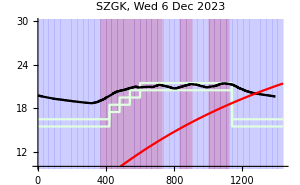
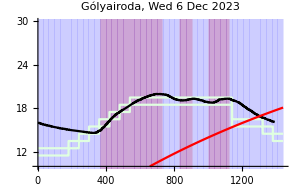
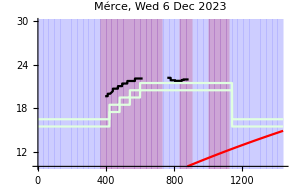
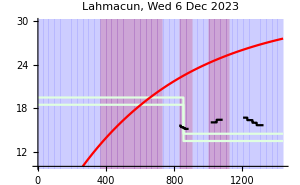

{15600.,12206.5,49042.7,30624.6}

```mathematica
simulatedDay=29;
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
{
daySimulation,
daySimulatedHeatDynamics,
dayHeatingSimulatedState,
dayRoomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomSimulatedTemp=dayRoomSimulatedTemp;
heatingSimulatedState=dayHeatingSimulatedState;
simulatedHeatDynamics=daySimulatedHeatDynamics;
Table[
Quiet[Plot[
{
roomsSetTemp[[roomN]][t]-roomsLowerBuffer[[roomN]][t],
roomsSetTemp[[roomN]][t],
roomsSetTemp[[roomN]][t]+roomsUpperBuffer[[roomN]][t],
roomsTrueTemp[[roomN]][t],
roomSimulatedTemp[[roomN]][t]
},{t,0,24 60},PlotStyle->{LightGreen,None,LightGreen,Black,Red},
PlotRange->{All,{10,30}},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->{
Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}],
Table[If[
heatingSimulatedState[t]==1,
{RGBColor[0,0,1,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
}
]
],{roomN,1,Length[roomsOnCycle]}]//Row
Join[
{100heatStockDaily[[cycle]][[dayN]][[-1]][[2]]},
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]
```

for season

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
seasonFitEvaluation=Quiet[
Module[
{roomEndTemps,heatingStateEnd},
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=None;
Table[
Check[
TimeConstrained[
Module[
{evaluationResults},
SetSimulatedDayForComparison[day,roomEndTemps,heatingStateEnd];
evaluationResults=EvaluateParameterVector[
warmingCorrection[[roomsOnCycle]],
coolingCorrection[[roomsOnCycle]]
];
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=Map[#[24 60]&,evaluationResults[[6]]];
evaluationResults[[{7,8}]]
],
5,
DateString[NormalizeDate[seasonDays[[day]]]]<>": timeout error"
],
DateString[NormalizeDate[seasonDays[[day]]]]<>": other error"]
,{day,simulatedDays}]
]
];
```

```mathematica
simulatedDays={29,30,31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,53,54,57,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,98,99,103,104,105,106,107,108,111,112,114,120,121,122,125,126,127,128,129,132,133,134,135,136,139};
```

```mathematica
simulatedDays=Complement[Range[Length[seasonDays]],Flatten[Map[Position[seasonFitEvaluation,#]&,Select[seasonFitEvaluation,StringQ]]]];
```

```mathematica
seasonFitEvaluation//Length
```

80

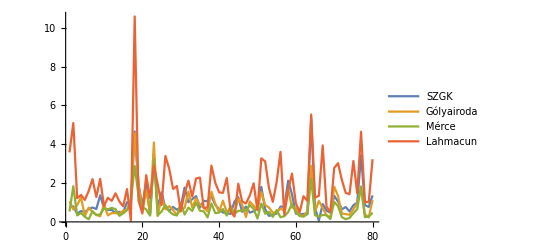

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[1]][[roomN]]
},{roomN,1,Length[roomsOnCycle]}]
,{day,1,Length[seasonFitEvaluation]}]],Joined->True,PlotRange->{All,All},PlotLegends->roomNames[[roomsOnCycle]]
]
```

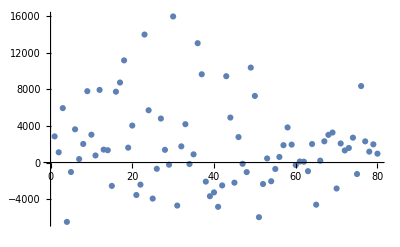

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[2]][[heatMeasureType]]
},{heatMeasureType,1,1}],{day,1,Length[seasonFitEvaluation]}]]
]
```

#### fit for multiple days cycle 1

```mathematica
daysToFit={32,37,42,57,67,72,77,82,92,122,127};
```

##### calc fit

calc

```mathematica
SetSimulatedCycle[1];
SetSimulationParameters[];
```

```mathematica
tournamentSize=10;
tournamentWinnerNumber=3;
tournamentRounds=4;
mutationMagnitude=0.1;
```

```mathematica
initialPopulationSize=30;
chromosomeLength=2Length[roomsOnCycle];
```

```mathematica
daysToFitCandidates={32,37,42,47,52,57,62,67,72,77,82,87,92,103,107,112,117,122,127};
testIndividual=RandomReal[{0,2},chromosomeLength];
dataExistenceCheck=Map[
Quiet[
{
#,
Check[
TimeConstrained[
{
SetSimulatedDayForComparison[#,ConstantArray[None,Length[roomsOnCycle]],None];
EvaluateParameterVector[
testIndividual[[1;;chromosomeLength/2]],
testIndividual[[chromosomeLength/2+1;;chromosomeLength]]
];
},
5,
"error"
],
"error"]
}
]&,
daysToFitCandidates];
errorDays=daysToFitCandidates[[Transpose[Position[dataExistenceCheck,"error"]][[1]]]];
daysToFit=Complement[daysToFitCandidates,errorDays];
```

```mathematica
dayFitResults={};
numOfGenerations=30;
tempErrorWeight=1;
heatErrorWeight=0;heatMeasureType=2;
Table[
dayN=daysToFit[[dayNN]];
startPopulation=Table[RandomReal[{0,2},chromosomeLength],{n,1,initialPopulationSize}];
Module[
{evolution},
Echo[DateString[Date[]]<>": starting "<>DateString[NormalizeDate[seasonDays[[dayN]]]]];
SetSimulatedDayForComparison[dayN,ConstantArray[None,Length[roomsOnCycle]],None];
evolution=Module[
{generations,population,newGeneration,newPopulation},
generations={};
Table[
If[
Mod[g,2]==0,
Echo[DateString[Date[]]<>": starting generation "<>ToString[g]];
];
If[g==1,population=startPopulation,population=generations[[-1]][[-1]]];
newGeneration=GenerateNewPopulation[
FitnessFunction,tempErrorWeight,heatErrorWeight,heatMeasureType,
population,
tournamentSize,tournamentWinnerNumber,tournamentRounds,
mutationMagnitude
];
If[g==1,generations={newGeneration},generations=Join[generations,{newGeneration}]];
,{g,1,numOfGenerations}];
generations
];
If[dayFitResults=={},dayFitResults={evolution},dayFitResults=Join[dayFitResults,{evolution}]];
Export[NotebookDirectory[]<>"\\ga_3.mx",dayFitResults];
]
,{dayNN,1,Length[daysToFit]}];
```

```mathematica
dayFitResults=Import[NotebookDirectory[]<>"\\ga_3.mx"];
```

```mathematica
dayFitResults//Dimensions
```

{17,30,5}

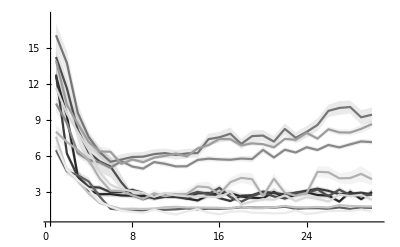

```mathematica
ErrorListPlot[
Table[Transpose[Table[
Flatten[{g,GetMeanAndSEM[100 /dayFitResults[[fittedDay]][[g]][[1]]]}]
,{g,1,30}]],{fittedDay,1,Length[dayFitResults]}],
Map[GrayLevel[1/(Length[dayFitResults]+2)+#/(Length[dayFitResults]+2)]&,Range[Length[dayFitResults]]],
{},
{True,True,False}
]
```

```mathematica
(*Export[NotebookDirectory[]<>"\\ga_1.mx",dayFitResults];*)
```

best fits for each day fitted

```mathematica
bestFiveFromEachDay=Table[Reverse[SortBy[Flatten[Table[Transpose[{dayFitResults[[day]][[generation]][[1]],dayFitResults[[day]][[generation-1]][[-1]]}],{generation,2,30}],1],First]][[1;;5]]
,{day,1,Length[dayFitResults]}];
```

```mathematica
ErrorListPlot[
{
Join[
{Range[8]},
GetMeanAndSEM[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]]
]
},
{Black},
{},
{False,False,True}
]
```

-Graphics-

```mathematica
bestFitMeansOverall=Mean[Transpose[Flatten[bestFiveFromEachDay,1]][[2]]];
```

seasonal trends in correction?

```mathematica
(*{
populationFitness,
offspringFitness,
population,
offspring,
newPopulation
}*)
```

```mathematica
seasonalCorrector=Mean[Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-20;;-1]]][[2]]]
,{fittedDayN,1,Length[daysToFit]}]]];
```

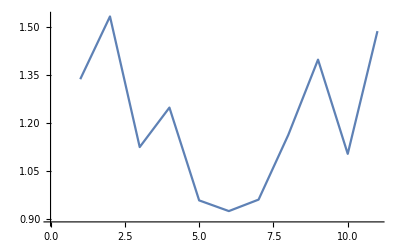

```mathematica
ListPlot[seasonalCorrector,Joined->True]
```

```mathematica
startDayN=1;
endDayN=170;
```

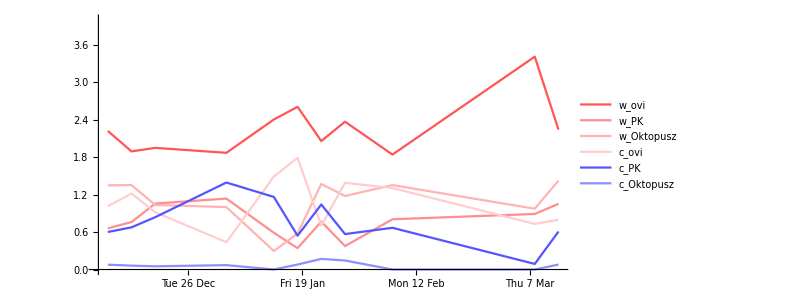

```mathematica
ListPlot[
Transpose[Table[
Transpose[{
ConstantArray[daysToFit[[fittedDayN]],Length[roomsOnCycle]2],
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
}]
,{fittedDayN,1,Length[daysToFit]}]],
Joined->True,PlotStyle->Flatten[{Map[Nest[Lighter,Red,#]&,Range[1,4]],Map[Nest[Lighter,Blue,#]&,Range[1,4]]}],
PlotLegends->Flatten[{Map["w_"<>#&,roomNames[[roomsOnCycle]]],Map["c_"<>#&,roomNames[[roomsOnCycle]]]}],
ImageSize->600,AspectRatio->0.5,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{0,4}}
]
```

```mathematica
seasonCorrectedBestFits=Map[Mean,Transpose[Table[
Mean[Transpose[SortBy[Flatten[Map[Transpose[#[[{1,3}]]]&,dayFitResults[[fittedDayN]]],1],First][[-10;;-1]]][[2]]]/seasonalCorrector[[fittedDayN]]
,{fittedDayN,1,Length[daysToFit]}]]]
```

```mathematica
seasonCorrectedBestFits={2.2612754125177195,0.7672629015155057,1.083197120703778,1.0727627094334409,0.7447439197371224,0.06677408038862163}
```

{2.26128,0.767263,1.0832,1.07276,0.744744,0.0667741}

##### eval fit

for one day

```mathematica
bestFitMeansOverall={3.1725563115559083,1.0683009750379302,1.29468510022947,1.278422223763722,1.9544085048287771,0.6946838470957711,0.3455993563985235,0.9222435820921898};
```

```mathematica
individual=bestFitMeansOverall
```

{4.82679,1.43645,1.59447,1.53515,2.32085,0.53767,0.398612,0.65944}

```mathematica
warmingParams=bestFitMeansOverall[[1 ;; 4]];
coolingParams=bestFitMeansOverall[[5 ;; 8]];
warmingCorrection={1,1,1,1,1,1,1,1,1,1};
coolingCorrection={1,1,1,1,1,1,1,1,1,1};
Table[
warmingCorrection[[roomsOnCycle[[roomN]]]]=warmingParams[[roomN]];
coolingCorrection[[roomsOnCycle[[roomN]]]]=coolingParams[[roomN]];
,{roomN,1,Length[roomsOnCycle]}];
warmingCorrection
coolingCorrection
```

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
```

```mathematica
roomTempStart
```

{0,0,0,0}

```mathematica
Evaluate[NumberQ[None]]
```

False

```mathematica
simulatedDay=29;
SetSimulatedDayForComparison[simulatedDay,{0,0,0,0},1];
{
daySimulation,
daySimulatedHeatDynamics,
dayHeatingSimulatedState,
dayRoomSimulatedTemp
}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomSimulatedTemp=dayRoomSimulatedTemp;
heatingSimulatedState=dayHeatingSimulatedState;
simulatedHeatDynamics=daySimulatedHeatDynamics;
Table[
Quiet[Plot[
{
roomsSetTemp[[roomN]][t]-roomsLowerBuffer[[roomN]][t],
roomsSetTemp[[roomN]][t],
roomsSetTemp[[roomN]][t]+roomsUpperBuffer[[roomN]][t],
roomsTrueTemp[[roomN]][t],
roomSimulatedTemp[[roomN]][t]
},{t,0,24 60},PlotStyle->{LightGreen,None,LightGreen,Black,Red},
PlotRange->{All,{10,30}},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]<>", "<>DateString[NormalizeDate[seasonDays[[dayN]]]],ImageSize->300,
Prolog->{
Table[If[
heatingTrueState[t]==1,
{RGBColor[1,0,0,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}],
Table[If[
heatingSimulatedState[t]==1,
{RGBColor[0,0,1,0.1],Rectangle[{t,-100},{t+5,100}]},
Nothing
]
,{t,0,24 60 -5,5}]
}
]
],{roomN,1,Length[roomsOnCycle]}]//Row
Join[
{100heatStockDaily[[cycle]][[dayN]][[-1]][[2]]},
Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]],
{
Mean[Total[Map[
Map[Total,#]
&,simulatedHeatDynamics]]]
}
]
```

-Graphics--Graphics--Graphics--Graphics-

{15600.,12206.5,49042.7,30624.6}

for season

```mathematica
warmingCorrection={1,1,2,1.0683009750379302,1.5,1,1,1,1,1.278422223763722};
coolingCorrection={1,1,1.8,0.8,0.7,1,1,1,1,1.1};
```

```mathematica
seasonFitEvaluation=Quiet[
Module[
{roomEndTemps,heatingStateEnd},
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=None;
Table[
Check[
TimeConstrained[
Module[
{evaluationResults},
SetSimulatedDayForComparison[day,roomEndTemps,heatingStateEnd];
evaluationResults=EvaluateParameterVector[
warmingCorrection[[roomsOnCycle]],
coolingCorrection[[roomsOnCycle]]
];
roomEndTemps=ConstantArray[None,Length[roomsOnCycle]];
heatingStateEnd=Map[#[24 60]&,evaluationResults[[6]]];
evaluationResults[[{7,8}]]
],
5,
DateString[NormalizeDate[seasonDays[[day]]]]<>": timeout error"
],
DateString[NormalizeDate[seasonDays[[day]]]]<>": other error"]
,{day,simulatedDays}]
]
];
```

```mathematica
simulatedDays={29,30,31,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,53,54,57,59,60,61,62,63,64,65,66,67,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,98,99,103,104,105,106,107,108,111,112,114,120,121,122,125,126,127,128,129,132,133,134,135,136,139};
```

```mathematica
simulatedDays=Complement[Range[Length[seasonDays]],Flatten[Map[Position[seasonFitEvaluation,#]&,Select[seasonFitEvaluation,StringQ]]]];
```

```mathematica
seasonFitEvaluation//Length
```

80

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[1]][[roomN]]
},{roomN,1,Length[roomsOnCycle]}]
,{day,1,Length[seasonFitEvaluation]}]],Joined->True,PlotRange->{All,All},PlotLegends->roomNames[[roomsOnCycle]]
]
```

-Graphics-

```mathematica
ListPlot[
Transpose[Table[
Table[{
day,
seasonFitEvaluation[[day]][[2]][[heatMeasureType]]
},{heatMeasureType,1,1}],{day,1,Length[seasonFitEvaluation]}]]
]
```

-Graphics-

#### summary

```mathematica
daysFitted={
{32,37,42,57,67,72,77,82,92,122,127},
{34,38,43,47,53,63,73,78,83,88,93,98,103,108,114,122,128}
};
```

```mathematica
seasonCorrectedBestFits={
{2.2612754125177195,0.7672629015155057,1.083197120703778,1.0727627094334409,0.7447439197371224,0.06677408038862163},
{2.3480290895305607,0.7801014999645991,0.9513837546933651,0.9297576319359259,1.4780859968954623,0.5046262989177167,0.2679036077336363,0.6731878383370469}
};
```

## deploy

### settings

```mathematica
startDayN=Position[seasonDays,heatDataDays[[1]]][[1]][[1]];
endDayN=Position[seasonDays,heatDataDays[[-1]]][[1]][[1]];
simulatedDayNToDayN=Range[startDayN,endDayN];
```

```mathematica
(*{room,day}, 1-es kör: dec 24 -  jan 2 + jan 13, 2-es kör: dec 24 - jan 2*)
offdays=Flatten[{
Flatten[Table[Transpose[{ConstantArray[room,Length[Range[47,56]]],Range[47,56]}],{room,Flatten[Position[roomToCycle,1]]}],1],
Flatten[Table[Transpose[{ConstantArray[room,Length[Range[47,56]]],Range[47,56]}],{room,Flatten[Position[roomToCycle,2]]}],1],
Table[Transpose[{room,67}],{room,Flatten[Position[roomToCycle,1]]}],
Table[{10,dayN},{dayN,15,29}]
},1];
```

```mathematica
simulatedRooms=Sort[Flatten[{roomsByCycle[[1]],roomsByCycle[[2]]}]];
```

```mathematica
trueHeatConsumptionForSeason=Transpose[Table[
Transpose[SortBy[Flatten[Table[
Transpose[{
roomsByCycle[[cycle]],
Total[Transpose[heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDayN]]]]][[2]]]roomHeatTakeupRatios[[roomsByCycle[[cycle]]]]
}],{cycle,1,2}],1],First]][[2]]
,{simulatedDayN,1,Length[simulatedDayNToDayN]}]];
```

Part::partd: Part specification roomHeatTakeupRatios⟦{1,2,9}⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{1,2,9},8745.57 roomHeatTakeupRatios⟦{1,2,9}⟧} cannot be transposed.

Part::partd: Part specification roomHeatTakeupRatios⟦{3,4,5,10}⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {{3,4,5,10},9140.53 roomHeatTakeupRatios⟦{3,4,5,10}⟧} cannot be transposed.

Part::partd: Part specification roomHeatTakeupRatios⟦{1,2,9}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1,2,9},10966.4 roomHeatTakeupRatios⟦{1,2,9}⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

### comparison baselines

```mathematica
trueTempDivergencesForSeason=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]]][[2]];
temp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[1]]][[2]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
{
-Map[Last,Select[Transpose[{heating,(setTemp-lowerBuffer)-temp}],#[[1]]==0&&0<#[[2]]&]],(*underheated*)
Map[Last,Select[Transpose[{heating,temp-(setTemp+upperBuffer)}],#[[1]]==1&&0<#[[2]]&]]    (*overheated*)
},
{None,None}
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

```mathematica
trueTempUnderSamplingRatio=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]]][[2]];
temp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[1]]][[2]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
Length[Select[Transpose[{
heating,
temp,
setTemp,
lowerBuffer,
upperBuffer
}],NumberQ[Total[#]]&]]/288
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

```mathematica
trueOverheatingHeat=Quiet[Table[
Table[
Module[
{dayN,roomTemp,setTemp,buffer,heatGain},
dayN=simulatedDayNToDayN[[simulatedDayN]];
If[
Length[roomTempsDaily[[room]][[dayN]]]!=0&&Length[roomHeatTakeupDaily[[room]][[dayN]]]!=0,
heatGain=Transpose[roomHeatTakeupDaily[[room]][[dayN]]][[2]]100;
roomTemp=Transpose[roomTempsDaily[[room]][[dayN]][[1]]][[2]];
setTemp=Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]];
buffer=Transpose[roomTempsDaily[[room]][[dayN]][[3]]][[2]];
Map[
#[[{4,5}]]
&,Select[
Transpose[{roomTemp,setTemp,buffer,heatGain,roomTemp-(setTemp+buffer)}],
#[[2]]+#[[3]]<#[[1]]&&0<#[[4]]&
]],
None
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}
],{room,simulatedRooms}]];
```

### replikálás

#### set temps

```mathematica
roomNames
```

{ovi,PK,SZGK,Gólyairoda,Mérce,vendégtér,kisterem,trafóház,Oktopusz,Lahmacun,Kazán közös terek,műhely}

```mathematica
noneTemps={14,14,14,14,14,14,14,14,12,14};
roomsSeasonSetTemps=Table[
Table[
If[
Length[roomTempsDaily[[room]][[dayN]]]==0||DeleteDuplicates[Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]]][[1]]=="n",
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[noneTemps[[room]],288]}],InterpolationOrder->0],
Interpolation[Select[Transpose[{Range[0,24 60-5,5],Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]]}],NumberQ[Total[#]]&],InterpolationOrder->0]
]
,{dayN,startDayN,endDayN}],{room,1,10}];
roomsSeasonLowerBuffers=Table[
Table[
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0.5,288]}],InterpolationOrder->0]
,{dayN,startDayN,endDayN}],{room,1,10}];
roomsSeasonUpperBuffers=Table[
Table[
Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0.5,288]}],InterpolationOrder->0]
,{dayN,startDayN,endDayN}],{room,1,10}];
```

```mathematica
ConstantArray[{12,12,12,12,12,12,12,12,10,12}[[room]],288]
```

```mathematica
startDay=69+6;
roomsOffdaySetTemps=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0,288]}],InterpolationOrder->0],7]
,{room,1,10}];
roomsOffdayLowerBuffer=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[roomTempsDaily[[room]][[startDay]][[3]][[1]][[2]],288]}],InterpolationOrder->0],7],{room,1,10}];
roomsOffdayUpperBuffer=Table[
ConstantArray[Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[roomTempsDaily[[room]][[startDay]][[4]][[1]][[2]],288]}],InterpolationOrder->0],7],{room,1,10}];
```

#### simulation

```mathematica
cycle=2;
SetSimulatedCycle[cycle];
SetSimulationParameters[];
```

```mathematica
simulationStarted=False;
dayN=startDayN;
simulatedSeasonForCycle=Table[
If[
simulationStarted==False,
{
roomsTempStartIn={21,18,18,18};
heatingStateStartIn=0;
simulationStarted=True;
}
];
dayN=simulatedDayNToDayN[[simulatedDayN]];
dayOfWeek=DateValue[seasonDays[[dayN]],"DayNameShort"]/.dayNameToDayOfWeek;
roomsSetTempIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdaySetTemps[[room]][[dayOfWeek]],
roomsSeasonSetTemps[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
roomsLowerBufferIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdayLowerBuffer[[room]][[dayOfWeek]],
roomsSeasonLowerBuffers[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
roomsUpperBufferIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdayUpperBuffer[[room]][[dayOfWeek]],
roomsSeasonUpperBuffers[[room]][[simulatedDayN]]
]
],{roomN,1,Length[roomsOnCycle]}];
SetSimulatedDay[dayN,roomsSetTempIn,roomsLowerBufferIn,roomsUpperBufferIn,roomsTempStartIn,heatingStateStartIn];
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp}=SimulateDayForCycle[warmingCorrection,coolingCorrection];
roomsTempStartIn=Map[#[24 60]&,roomsSimulatedTemp];
heatingStateStartIn=heatingSimulatedState[24 60];
{{dayN,seasonDays[[dayN]]},simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp,roomsSetTemp,roomsLowerBuffer,roomsUpperBuffer}
,{simulatedDayN,1,Length[simulatedDayNToDayN]}];
```

```mathematica
warmingCorrection={0.53,0.515,0.59,0.555,  0.63,1,1,1,0.65,0.48};(*csökkentés jó eséllyel lefelé tol*)
       coolingCorrection={0.75,0.80,  0.71,   0.79, 0.60,1,1,1,0.64,0.44   };(*csökkentés jó eséllyel jobbra tol*)
roomsRadiatorOffTemp={21,      23,    25.5,22.5,22.5,26,0,24.5,20,21};
```

```mathematica
warmingCorrection=ConstantArray[1,10];
coolingCorrection=ConstantArray[1,10];
roomsRadiatorOffTemp={21,23,22,22.5,22.5,26,0,24.5,20,21};
```

#### plot

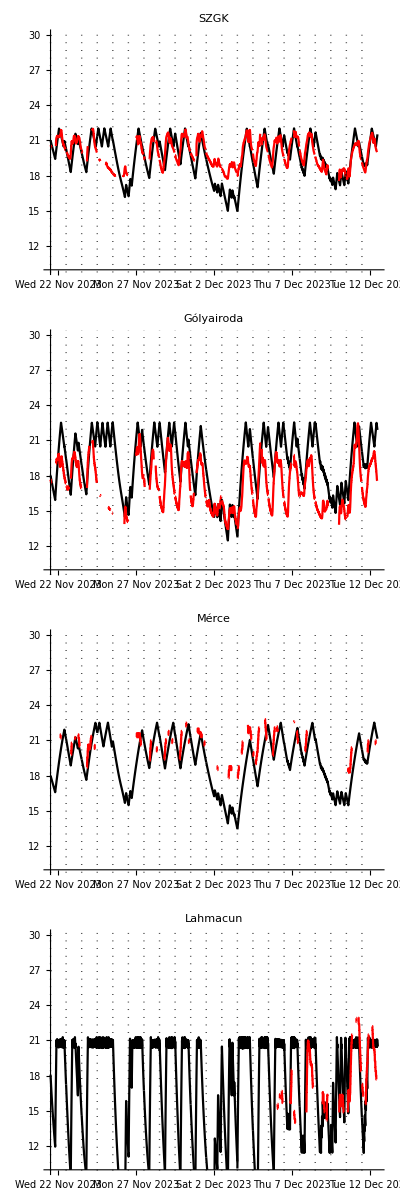

```mathematica
plotDay=1;
Table[
ListPlot[
Flatten[Table[Map[
Transpose[{
(simulatedDay-1) 24 60+Range[0,24 60-5,5],
#
}]
&,Join[
Transpose[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60-5,5}]],
{
If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
ConstantArray[0,288]
]
}
]
],{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]]}],1],
PlotStyle->{Black,Red},ImageSize->1000,Joined->True,AspectRatio->0.1,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]],
Ticks->{
Table[
{
(simulatedDay-1) 24 60+12 60,
Rotate[DateString[NormalizeDate[seasonDays[[startDayN+simulatedDay-1]]]],Pi/2]
}
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]],1}],
Automatic
},
Prolog->{
Black,Thin,Dotted,
Table[
Line[{{(simulatedDay-1) 24 60,-50},{(simulatedDay-1) 24 60,50}}]
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycle]]}]
},PlotRange->{All,{10,30}}
],{roomN,1,Length[roomsOnCycle]}]//Column
```

```mathematica
plotDay=80;
Table[
Table[
ListPlot[
Join[
Transpose[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]-simulatedSeasonForCycle[[simulatedDay]][[6]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]+simulatedSeasonForCycle[[simulatedDay]][[7]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60,5}]],
{
If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Nothing
]
}
],
PlotStyle->{LightGreen,LightGreen,Black,Red},ImageSize->200,Joined->True,PlotLabel->DateString[NormalizeDate[seasonDays[[simulatedDay]]]]
],{roomN,1,Length[roomsOnCycle]}],{simulatedDay,plotDay,plotDay+2}]//Grid
```

#### evaluation

##### heat (cost)

```mathematica
(*simulatedHeatDynamics: loss, gain*)
```

```mathematica
simulatedVsTrueHeatStockDailyForCycle=Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDay]]]][[-1]][[2]]roomHeatTakeupRatios[[roomsOnCycle]],
Table[
Total[simulatedSeasonForCycle[[simulatedDay]][[2]][[roomN]][[2]]]
,{roomN,1,Length[roomsOnCycle]}]
}
,{simulatedDay,1,Length[simulatedSeasonForCycle]}];
```

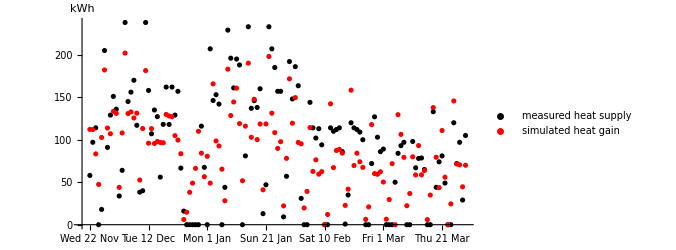

```mathematica
ListPlot[
Transpose[Map[
{
{#[[1]],Total[#[[2]]]},
{#[[1]],Total[#[[3]]]}
}&,simulatedVsTrueHeatStockDailyForCycle]],
PlotStyle->{Black,Red},
PlotRange->{All,All},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,5]
],
Automatic
},PlotLegends->Placed[{"measured heat supply","simulated heat gain"},Bottom],ImageSize->500,AspectRatio->0.5,AxesLabel->{None,"kWh"}
]
```

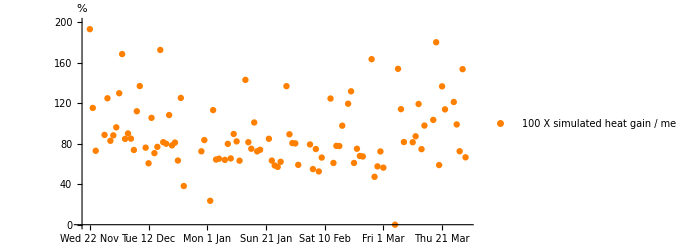

```mathematica
ListPlot[
Quiet[Map[
{#[[1]],100Total[#[[3]]]/Total[#[[2]]]}
&,simulatedVsTrueHeatStockDailyForCycle]],
PlotStyle->{Orange},
PlotRange->{All,{0,200}},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,5]
],
Automatic
},PlotLegends->Placed[{"100 X simulated heat gain / measured heat supply"},Bottom],ImageSize->500,AspectRatio->0.5,AxesLabel->{None,"%"}
]
```

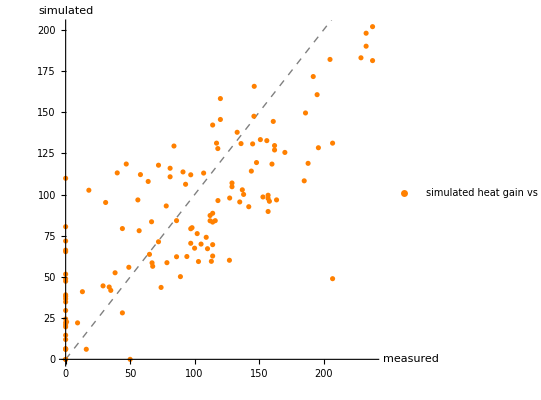

```mathematica
ListPlot[
Quiet[Map[
{Total[#[[2]]],Total[#[[3]]]}
&,simulatedVsTrueHeatStockDailyForCycle]],
PlotStyle->{Orange},
PlotRange->{All,All},AspectRatio->1,PlotLegends->Placed[{"simulated heat gain vs measured heat supply"},Bottom],ImageSize->400,AspectRatio->0.5,AxesLabel->{"measured","simulated"},Prolog->{Gray,Dashed,Line[{{0,0},{1000,1000}}]}
]
```

```mathematica
Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]]
```

11961.8

```mathematica
Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[3]]]]
100(Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[3]]]])/(Total[Total[Transpose[simulatedVsTrueHeatStockDailyForCycle][[2]]]])-100
```

11243.4

-6.00551

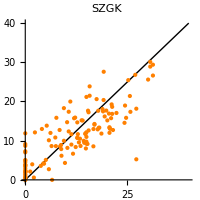
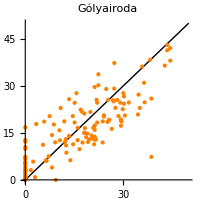
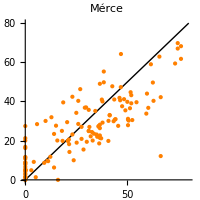
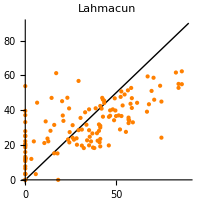

```mathematica
Table[
Module[
{heatData,maxHeat},
heatData=Map[
{
#[[2]][[roomN]],
#[[3]][[roomN]]
}
&,simulatedVsTrueHeatStockDailyForCycle];
maxHeat=Ceiling[Max[heatData],10];
ListPlot[
heatData,
AspectRatio->1,PlotRange->{{0,maxHeat},{0,maxHeat}},Prolog->{Thin,Black,Line[{{0,0},{maxHeat,maxHeat}}]},
PlotStyle->{PointSize->0.025,Orange},PlotLabel->roomNames[[roomsOnCycle[[roomN]]]],ImageSize->200
]
]
,{roomN,1,Length[roomsOnCycle]}]//Row
```

##### temperature (performance)

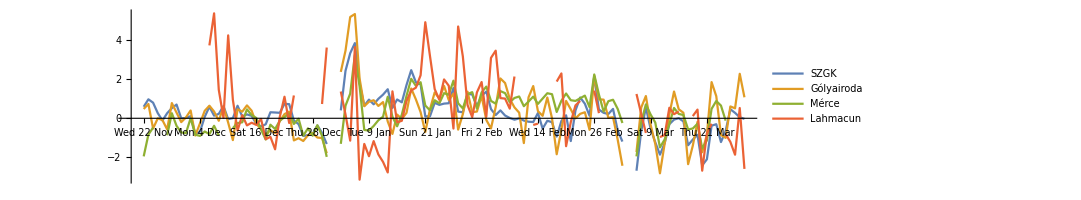

```mathematica
simulatedDailyTempVsTrueTempForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
#[[2]]-#[[1]]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Table[simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],{t,0,24 60-5,5}]
}],
NumberQ[Total[Flatten[#]]]
&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
ListPlot[
Transpose[Table[Map[
{
simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[1]],
Mean[#]
}
&,simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[2]]
],{simulatedDay,1,Length[simulatedSeasonForCycle]}]],Joined->True,AspectRatio->0.25,ImageSize->800,PlotRange->{All,All},
Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotLegends->roomNames[[roomsOnCycle]]
]
```

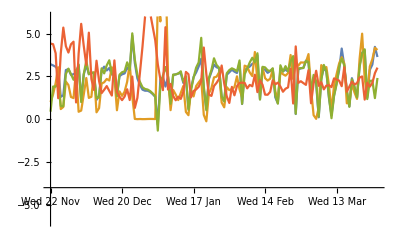
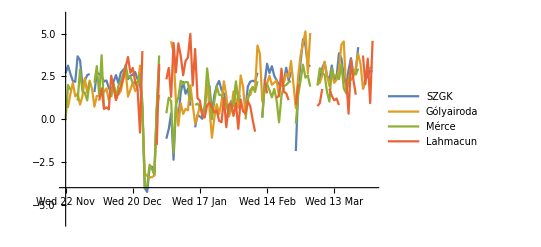

```mathematica
simulatedDailyTempDivergenceVsTrueDivergenceForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[Map[
If[
#[[1]]<#[[2]],
#[[1]]-#[[2]],
#[[1]]-#[[3]]
]&,
Select[
Table[{
simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]-simulatedSeasonForCycle[[simulatedDay]][[6]][[roomN]][t],
simulatedSeasonForCycle[[simulatedDay]][[5]][[roomN]][t]+simulatedSeasonForCycle[[simulatedDay]][[7]][[roomN]][t]
},{t,0,24 60-5,5}],
Between[
#[[1]],
#[[2;;3]]
]==False&]
],{roomN,1,Length[roomsOnCycle]}],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
If[
#[[1]]<#[[2]],
#[[1]]-#[[2]],
#[[1]]-#[[3]]
]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[2]]][[2]]-Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[3]]][[2]],
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[2]]][[2]]+Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[4]]][[2]]
}],
Between[
#[[1]],
#[[2;;3]]
]==False&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
Table[
ListPlot[
Transpose[Table[
Map[{
simulatedDailyTempDivergenceVsTrueDivergenceForCycle[[simulatedDay]][[1]],
Mean[#]
}&,simulatedDailyTempDivergenceVsTrueDivergenceForCycle[[simulatedDay]][[simulatedOrTrue]]]
,{simulatedDay,1,Length[simulatedSeasonForCycle]}]],
Joined->True,ImageSize->400,Ticks->{
Map[
{
#,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[#]]]]," "][[1;;3]]," "],Pi/2]
}
&,Range[startDayN,endDayN,4]
],
Automatic
},PlotRange->{All,{-6,6}},AxesOrigin->{startDayN,-4},PlotLegends->{None,roomNames[[roomsOnCycle]]}[[simulatedOrTrue-1]]
],{simulatedOrTrue,2,3}]//Row
```

##### heat vs temp (cost vs performance)

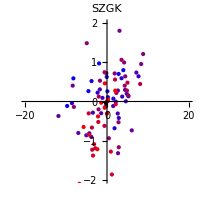
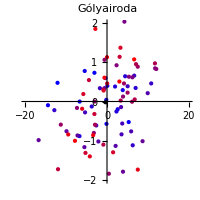
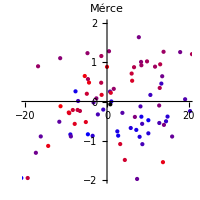
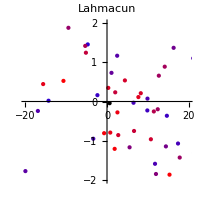

```mathematica
fittedDays=Complement[Range[1,Length[simulatedDayNToDayN]],Range[55,85]];
simulatedVsTrueHeatStockDailyForCycle=Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
heatStockDaily[[cycle]][[simulatedDayNToDayN[[simulatedDay]]]][[-1]][[2]]roomHeatTakeupRatios[[roomsOnCycle]],
Table[
Total[simulatedSeasonForCycle[[simulatedDay]][[2]][[roomN]][[2]]]
,{roomN,1,Length[roomsOnCycle]}]
}
,{simulatedDay,1,Length[simulatedSeasonForCycle]}];
simulatedDailyTempVsTrueTempForCycle=Quiet[Table[
{
simulatedSeasonForCycle[[simulatedDay]][[1]][[1]],
Table[If[
Length[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]]]!=0,
Map[
#[[2]]-#[[1]]&,
Select[
Transpose[{
Transpose[roomTempsDaily[[roomsOnCycle[[roomN]]]][[simulatedSeasonForCycle[[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Table[simulatedSeasonForCycle[[simulatedDay]][[4]][[roomN]][t],{t,0,24 60-5,5}]
}],
NumberQ[Total[Flatten[#]]]
&]
],
{}
]
,{roomN,1,Length[roomsOnCycle]}]
},{simulatedDay,1,Length[simulatedSeasonForCycle]}]];
heatSumError=Transpose[Table[
(simulatedVsTrueHeatStockDailyForCycle[[simulatedDay]][[2]]-simulatedVsTrueHeatStockDailyForCycle[[simulatedDay]][[3]])
,{simulatedDay,fittedDays}]];
dailyTempError=Transpose[Table[
Map[If[Length[#]!=0,Mean[#],Missing]&,simulatedDailyTempVsTrueTempForCycle[[simulatedDay]][[2]]]
,{simulatedDay,fittedDays}]];
Table[
Module[
{errorMeans,errorSEMs},
errorMeans={
Mean[RemoveOutliers[DeleteCases[heatSumError[[roomN]],Missing],3]],
Mean[RemoveOutliers[DeleteCases[dailyTempError[[roomN]],Missing],3]]
};
errorSEMs={
StandardError[RemoveOutliers[DeleteCases[heatSumError[[roomN]],Missing],3]],
StandardError[RemoveOutliers[DeleteCases[dailyTempError[[roomN]],Missing],3]]
};
ListPlot[
{},
PlotRange->{{-20,20},{-2,2}},
Epilog->{
{
Table[
Module[
{data},
data=Transpose[{heatSumError[[roomN]],dailyTempError[[roomN]]}];
{
RGBColor[n/Length[data],0,1-n/Length[data]],
PointSize->0.0125,
data[[n]]//If[NumberQ[Total[#]],Point[#],Nothing]&
}
],{n,1,Length[Transpose[{heatSumError[[roomN]],dailyTempError[[roomN]]}]]}],
Black,PointSize->0.025,
Point[{errorMeans[[1]],errorMeans[[2]]}],
RGBColor[0,0,0,0],
EdgeForm[{Thick,Black}],
Ellipsoid[{errorMeans[[1]],errorMeans[[2]]},15{errorSEMs[[1]],errorSEMs[[2]]}]
}
},AspectRatio->1,ImageSize->200,PlotLabel->roomNames[[roomsOnCycle[[roomN]]]]
]
],{roomN,1,Length[roomsOnCycle]}]//Row
```

```mathematica
(*final jav*)
	       			       (*ovi  PK   SZGK     GI   M   k  v  t  Okt  Lah*)
       warmingCorrection={0.53,0.515,0.59,0.555,  0.63,1,1,1,0.65,0.48};(*csökkentés jó eséllyel lefelé tol*)
       coolingCorrection={0.75,0.80,  0.71,   0.79, 0.60,1,1,1,0.64,0.44   };(*csökkentés jó eséllyel jobbra tol*)
roomsRadiatorOffTemp={21,      23,    25.5,22.5,22.5,26,0,24.5,20,21};
```

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics--Graphics-

##### both cycles

ugyanazok szerint a mértékek szerint, mint amivel az időprogramot is néztem

### időprogram

#### set room schedules

```mathematica
offdaySchedule=Interpolation[Transpose[{Range[0,24 60-5,5],ConstantArray[0,288]}],InterpolationOrder->0];(*0*)
ondayScheduleForOktopusz=Interpolation[{{0,0},{15 60-1,0},{15 60,1},{24 60-1,1},{24 60,0}},InterpolationOrder->0];(*3*)
ondayMondaySchedule=Interpolation[{{0,0},{1,0},{2,1},{17 60-1,1},{17 60,0}},InterpolationOrder->0];(*2*)
ondaySchedule=Interpolation[{{0,0},{5 60-1,0},{5 60,1},{17 60-1,1},{17 60,0}},InterpolationOrder->0];(*1*)
sundaySchedule=Interpolation[{{0,0},{15 60-1,0},{15 60,1},{24 60-1,1},{24 60,0}},InterpolationOrder->0];(*-1*)
```

```mathematica
(*buta időprogram*)
roomDayCategories={
{2,1,1,1,0,0,0},(*ovi*)
{2,1,1,1,1,0,0},(*PK*)
{2,1,1,1,1,0,0},(*SZGK*)
{2,1,1,1,1,0,0},(*Gólyairoda*)
{2,1,1,1,1,0,0},(*Mérce*)
{2,1,1,1,1,0,0},(*vendégtér*)
{2,1,1,1,1,0,0},(*kisterem*)
{2,1,1,1,1,0,0},(*trafóház*)
{2,1,1,1,1,0,0},(*Oktopusz*)
{2,1,1,1,1,0,0}   (*Lahmacun*)
};
```

```mathematica
(*okos időprogram*)
roomDayCategories={
{2,1,1,1,0,0,-1},(*ovi*)
{2,1,1,1,1,0,-1},(*PK*)
{2,1,1,1,1,0,-1},(*SZGK*)
{2,1,1,1,1,0,-1},(*Gólyairoda*)
{2,1,1,1,1,0,-1},(*Mérce*)
{2,1,1,1,1,0,-1},(*vendégtér*)
{2,1,1,1,1,0,-1},(*kisterem*)
{2,1,1,1,1,0,-1},(*trafóház*)
{0,3,0,3,3,3,-1},(*Oktopusz*)
{2,1,1,1,1,0,-1}   (*Lahmacun*)
};
```

```mathematica
roomsWeeklySchedules=roomDayCategories/.{
-1->sundaySchedule,
0->offdaySchedule,
1->ondaySchedule,
2->ondayMondaySchedule,
3->ondayScheduleForOktopusz
};
```

```mathematica
roomsOffdaySchedules=Table[offdaySchedule,{room,1,10}];
```

#### simulation

```mathematica
simulatedSeasonForCycles=
Table[
SetSimulatedCycle[cycle];
SetSimulationParameters[];
simulatedDayNToDayN=Range[startDayN,endDayN];
simulationStarted=False;
dayN=startDayN;
Table[
If[
simulationStarted==False,
{
roomsTempStartIn={{20,20,20},{21,18,18,18}}[[cycle]];
heatingStateStartIn=0;
radiatorStateStartIn={{1,1,1},{1,1,1,1}}[[cycle]];
simulationStarted=True;
}
];
dayN=simulatedDayNToDayN[[simulatedDayN]];
dayOfWeek=DateValue[seasonDays[[dayN]],"DayNameShort"]/.dayNameToDayOfWeek;
roomsSchedulesIn=Table[
Module[
{room,offdayForRoom},
room=roomsOnCycle[[roomN]];
offdayForRoom=MemberQ[offdays,{room,dayN}];
If[
offdayForRoom,
roomsOffdaySchedules[[room]],
roomsWeeklySchedules[[room]][[dayOfWeek]]
]
],{roomN,1,Length[roomsOnCycle]}];
SetSimulatedDayWithTimedHeating[dayN,roomsSchedulesIn,roomsTempStartIn,radiatorStateStartIn];
{simulation,simulatedHeatDynamics,heatingSimulatedState,roomsSimulatedTemp,radiatorSimulatedState}=SimulateDayForCycleWithTimedHeating[warmingCorrection,coolingCorrection];
roomsTempStartIn=Map[#[24 60]&,roomsSimulatedTemp];
radiatorStateStartIn=Map[#[24 60]&,radiatorSimulatedState];
heatingStateStartIn=heatingSimulatedState[24 60];
{
{dayN,seasonDays[[dayN]]},
simulatedHeatDynamics,
heatingSimulatedState,roomsSimulatedTemp
}
,{simulatedDayN,1,Length[simulatedDayNToDayN]}]
,{cycle,1,2}];
```

#### plot

```mathematica
plotDay=1;
Table[Table[
ListPlot[
Flatten[Table[Map[
Transpose[{
(simulatedDay-1) 24 60+Range[0,24 60-5,5],
#
}]
&,Join[
Transpose[Table[
{
simulatedSeasonForCycles[[cycle]][[simulatedDay]][[4]][[roomN]][t]
}
,{t,0,24 60-5,5}]],
{
If[
Length[roomTempsDaily[[roomsByCycle[[cycle]][[roomN]]]][[simulatedSeasonForCycles[[cycle]][[simulatedDay]][[1]][[1]]]]]!=0,
Transpose[roomTempsDaily[[roomsByCycle[[cycle]][[roomN]]]][[simulatedSeasonForCycles[[cycle]][[simulatedDay]][[1]][[1]]]][[1]]][[2]],
Nothing
]
}
]
],{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]]}],1],
PlotStyle->{Black,Red},ImageSize->1000,Joined->True,AspectRatio->0.1,PlotLabel->roomNames[[roomsByCycle[[cycle]][[roomN]]]],
Ticks->{
Table[
{
(simulatedDay-1) 24 60+12 60,
Rotate[StringRiffle[StringSplit[DateString[NormalizeDate[seasonDays[[startDayN+simulatedDay-1]]]]," "][[{3,2,1}]]," "],Pi/2]
}
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]],1}],
Automatic
},
Prolog->{
Black,Thin,Dotted,
Table[
Line[{{(simulatedDay-1) 24 60,-50},{(simulatedDay-1) 24 60,50}}]
,{simulatedDay,plotDay,Min[plotDay+20,Length[simulatedSeasonForCycles[[cycle]]]]}]
}
],{roomN,1,Length[roomsByCycle[[cycle]]]}],{cycle,1,2}]//Flatten//Column
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

#### evaluation

##### calc

```mathematica
simulatedHeatConsumptionForSeason=Transpose[Table[
Transpose[SortBy[Flatten[Table[
Transpose[{
roomsByCycle[[cycle]],
Table[Total[simulatedSeasonForCycles[[cycle]][[simulatedDayN]][[2]][[roomN]][[2]]],{roomN,1,Length[roomsByCycle[[cycle]]]}]
}],{cycle,1,2}],1],First]][[2]]
,{simulatedDayN,1,Length[simulatedSeasonForCycles[[1]]]}]];
```

```mathematica
simulatedTempDivergencesForSeason=Table[Table[
Module[
{heating,temp,setTemp,lowerBuffer,upperBuffer},
If[
Length[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&Length[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0,
heating=Map[simulatedSeasonForCycles[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]][[simulatedDayN]][[3]][#]&,Range[5,24 60,5]];
temp=Map[simulatedSeasonForCycles[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]][[simulatedDayN]][[4]][[Position[roomsByCycle[[roomToCycle[[simulatedRooms[[simulatedRoomN]]]]]],simulatedRooms[[simulatedRoomN]]][[1]][[1]]]][#]&,Range[5,24 60,5]];setTemp=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[2]]][[2]];
lowerBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[3]]][[2]];
upperBuffer=Transpose[roomTempsDaily[[simulatedRooms[[simulatedRoomN]]]][[simulatedDayNToDayN[[simulatedDayN]]]][[4]]][[2]];
{
-Map[Last,Select[Transpose[{heating,(setTemp-lowerBuffer)-temp}],#[[1]]==0&&0<#[[2]]&]],(*underheated*)
Map[Last,Select[Transpose[{heating,temp-(setTemp+upperBuffer)}],#[[1]]==1&&0<#[[2]]&]]    (*overheated*)
},
{None,None,None}
]
],{simulatedDayN,1,Length[simulatedDayNToDayN]}],{simulatedRoomN,1,Length[simulatedRooms]}];
```

```mathematica
simulatedOverheatingHeat=Table[
Module[
{room,cycle,roomN},
room=simulatedRooms[[simulatedRoomN]];
cycle=roomToCycle[[room]];
roomN=Position[roomsByCycle[[cycle]],room][[1]][[1]];
Table[
Module[
{dayN,roomTemp,setTemp,buffer,heatGain},
dayN=simulatedDayNToDayN[[simulatedDayN]];
heatGain=simulatedSeasonForCycles[[cycle]][[simulatedDayN]][[2]][[roomN]][[2]];
roomTemp=Map[simulatedSeasonForCycles[[cycle]][[simulatedDayN]][[4]][[roomN]],Range[5,24 60,5]];
If[
Length[roomTempsDaily[[room]][[dayN]]]!=0,
setTemp=Transpose[roomTempsDaily[[room]][[dayN]][[2]]][[2]];
buffer=Transpose[roomTempsDaily[[room]][[dayN]][[3]]][[2]];
Map[
#[[{4,5}]]
&,Select[
Transpose[{roomTemp,setTemp,buffer,heatGain,roomTemp-(setTemp+buffer)}],
#[[2]]+#[[3]]<#[[1]]&&0<#[[4]]&
]],
None
]
],{simulatedDayN,1,Length[simulatedSeasonForCycles[[1]]]}
]
],{simulatedRoomN,1,Length[simulatedRooms]}];
```

##### heat

```mathematica
ListPlot[{
Transpose[{Range[7]-0.08,Map[Total,trueHeatConsumptionForSeason]/100}],
Transpose[{Range[7]+0.08,Map[Total,simulatedHeatConsumptionForSeason]/100}]
},PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{-1000,11000}},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->"szezon teljes hőfogyasztása (különbség: "<>ToString[Round[100 Total[Map[Total,simulatedHeatConsumptionForSeason]]/Total[Map[Total,trueHeatConsumptionForSeason]]-100,0.1]]<>"%)",AxesLabel->{None,"kWh"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,-650}]&,Range[7]]}
]
```

-Graphics-

```mathematica
ListPlot[
{
Transpose[{Range[7]-0.08,Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]]]&,trueOverheatingHeat[[simulatedRoomN]]],NumberQ]]]/100,{simulatedRoomN,1,7}]}],
Transpose[{Range[7]+0.08,Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]]]&,simulatedOverheatingHeat[[simulatedRoomN]]],NumberQ]/100]],{simulatedRoomN,1,7}]}]
},
PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{-600,6000}},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->"feleslegesen leadott hő",AxesLabel->{None,"kWh"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,-400}]&,Range[7]]}
]
```

-Graphics-

```mathematica
(*a szezon teljes hőfogyasztásának hány százaléka felesleges?*)
100 Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,trueOverheatingHeat]/100]/Total[Map[Total,trueHeatConsumptionForSeason]/100]
100 Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,simulatedOverheatingHeat]/100]/Total[Map[Total,simulatedHeatConsumptionForSeason]/100]
```

19.7935

63.3034

```mathematica
(*hány kWh-val több a felesleges fűtés?*)
Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,simulatedOverheatingHeat]/100]-Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,trueOverheatingHeat]/100]
```

4631.18

```mathematica
((Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,simulatedOverheatingHeat]/100]-Total[Map[Total[Select[Map[Total,Flatten[#,1]],NumberQ]]&,trueOverheatingHeat]/100])/energyContentInGasPerCubicMeter)gasPricePerCubicMeter//N
```

343252.

```mathematica
ListPlot[
{
Transpose[{Range[7]-0.08,Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]](1+Transpose[#][[2]])]&,trueOverheatingHeat[[simulatedRoomN]]],NumberQ]]]/100,{simulatedRoomN,1,7}]}],
Transpose[{Range[7]+0.08,Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]](1+Transpose[#][[2]])]&,simulatedOverheatingHeat[[simulatedRoomN]]],NumberQ]/100]],{simulatedRoomN,1,7}]}]
},
PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{-1000,10000}},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->"feleslegesen leadott hő, eltéréssel súlyozva",AxesLabel->{None,"kWh x °C"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,-700}]&,Range[7]]}
]
```

-Graphics-

##### temp

```mathematica
ListPlot[
Flatten[Table[{
Table[
{
simulatedRoomN-0.08,
Mean[Select[Table[
trueTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//Mean
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
}
,{simulatedRoomN,1,Length[simulatedRooms]}],
Table[
{
simulatedRoomN+0.08,
Mean[Select[Table[
simulatedTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//Quiet[RandomSample[#,Round[Length[#]trueTempUnderSamplingRatio[[simulatedRoomN]][[simulatedDayN]]]]]&//Mean
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
}
,{simulatedRoomN,1,Length[simulatedRooms]}]
},{underOrOverHeated,1,2}],1],PlotStyle->{Red,Black},PlotRange->{{0.5,7.5},{-5,5}},
Filling->Axis,FillingStyle->{Thickness[0.02]},Ticks->{None,Automatic},
PlotLabel->"átlagos napi eltérések átlaga",AxesLabel->{None,"°C"},PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
ImageSize->400,Epilog->{Black,Map[Text[roomNames[[simulatedRooms]][[#]],{#,-4.5}]&,Range[7]]}
]
```

-Graphics-

jellemzően milyen hőmérsékletek munkanapokon munkaidőben?

```mathematica
Table[
Quiet[Module[
{room,trueTempSample,simulatedTempSample},
room=simulatedRooms[[simulatedRoomN]];
trueTempSample=Table[
If[
(DateValue[simulatedSeasonForCycles[[roomToCycle[[room]]]][[simulatedDayN]][[1]][[2]],"DayNameShort"]/.dayNameToDayOfWeek)<6&&
Length[roomTempsDaily[[room]][[simulatedDayNToDayN[[simulatedDayN]]]]]!=0&&
0<Mean[Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[room]]]]][[2]]],
DeleteCases[Transpose[roomTempsDaily[[room]][[simulatedDayNToDayN[[simulatedDayN]]]][[1]][[(9 60)/5+1;;(18 60)/5+1]]][[2]],"n"],
None
]
,{simulatedDayN,1,Length[simulatedDayNToDayN]}];
simulatedTempSample=Table[
If[
(DateValue[simulatedSeasonForCycles[[roomToCycle[[room]]]][[simulatedDayN]][[1]][[2]],"DayNameShort"]/.dayNameToDayOfWeek)<6&&
0.1<Mean[Transpose[heatingStateDaily[[simulatedDayNToDayN[[simulatedDayN]]]][[1+roomToCycle[[room]]]]][[2]]],
RandomSample[
Map[simulatedSeasonForCycles[[roomToCycle[[room]]]][[simulatedDayN]][[4]][[Position[roomsByCycle[[roomToCycle[[room]]]],room][[1]][[1]]]],Range[9 60,18 60]],Length[trueTempSample[[simulatedDayN]]]
],
None
]
,{simulatedDayN,1,Length[simulatedDayNToDayN]}];
Histogram[
{
Flatten[DeleteCases[trueTempSample,None]],
Flatten[DeleteCases[simulatedTempSample,None]]
},{0.5},ChartStyle->{Red,Black},PlotLabel->roomNames[[room]],AspectRatio->1,PlotRange->{{5,25},All},AxesLabel->{"°C","gyakoriság"},Ticks->{Automatic,None},ImageSize->200
]
]]
,{simulatedRoomN,1,Length[simulatedRooms]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

az energiának mekkora része pazarlódik? vagyis: mennyi energiát fogyaszt el a határérték feletti fűtés?

##### heat vs temp

```mathematica
Module[
{plotData,shortenedRoomNames},
plotData={
Transpose[{
Map[Total,trueHeatConsumptionForSeason]/100000,
Total[Abs[Table[Table[
Mean[Select[Table[
trueTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//Mean
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}],
Transpose[{
Map[Total,simulatedHeatConsumptionForSeason]/100000,
Total[Abs[Table[Table[
Quiet[Mean[Select[Table[
simulatedTempDivergencesForSeason[[simulatedRoomN]][[simulatedDayN]][[underOrOverHeated]]//Quiet[RandomSample[#,Round[Length[#]trueTempUnderSamplingRatio[[simulatedRoomN]][[simulatedDayN]]]]]&//Mean
,{simulatedDayN,1,Length[simulatedDayNToDayN]}],NumberQ]]]
,{simulatedRoomN,1,Length[simulatedRooms]}],{underOrOverHeated,1,2}]]]
}]
};
shortenedRoomNames=Map[StringTake[#,2]&,roomNames[[simulatedRooms]]];
ListPlot[
plotData,
AspectRatio->1,PlotRange->{{0,10},{0,7}},PlotStyle->{Red,Black},
AxesLabel->{"költség (MWh)","eltérés\n(°C)"},ImageSize->350,PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
Prolog->{
Thickness[0.005],GrayLevel[0.2],
Map[Arrow[Reverse[#]]&,Transpose[plotData]],
PointSize->0.025,
Red,Map[Point,plotData[[1]]],
Black,Map[Point,plotData[[2]]]
},
Epilog->{
FontSize->10,
Map[
Module[
{startPos,endPos,vector},
startPos=plotData[[1]][[#]];
endPos=plotData[[2]][[#]];
vector=endPos-startPos;
{
White,Ellipsoid[startPos+0.5vector,{0.1,0.05}],
Black,Text[shortenedRoomNames[[#]],startPos+0.5vector]
}
]&,Range[Length[simulatedRooms]]]
}
]
]
```

-Graphics-

```mathematica
Module[
{plotData,shortenedRoomNames},
plotData={
Transpose[{
Map[Total,trueHeatConsumptionForSeason]/100000,
Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]]]&,trueOverheatingHeat[[simulatedRoomN]]],NumberQ]]]/100000,{simulatedRoomN,1,7}]
}],
Transpose[{
Map[Total,simulatedHeatConsumptionForSeason]/100000,
Table[Quiet[Total[Select[Map[Total[Transpose[#][[1]]]&,simulatedOverheatingHeat[[simulatedRoomN]]],NumberQ]]]/100000,{simulatedRoomN,1,7}]
}]
};
shortenedRoomNames=Map[StringTake[#,2]&,roomNames[[simulatedRooms]]];
ListPlot[
plotData,
AspectRatio->1,PlotRange->{{0,10},{0,4}},PlotStyle->{Red,Black},
AxesLabel->{"költség (MWh)","pazarlás\n(MWh)"},ImageSize->350,PlotLegends->Placed[{"mért (termosztatikus)","szimulált (időprogram)"},Bottom],
Prolog->{
Thickness[0.005],GrayLevel[0.2],
Map[Arrow[Reverse[#]]&,Transpose[plotData]],
PointSize->0.025,
Red,Map[Point,plotData[[1]]],
Black,Map[Point,plotData[[2]]]
},
Epilog->{
FontSize->10,
Map[
Module[
{startPos,endPos,vector},
startPos=plotData[[1]][[#]];
endPos=plotData[[2]][[#]];
vector=endPos-startPos;
{
White,Ellipsoid[startPos+0.5vector,{0.1,0.05}],
Black,Text[shortenedRoomNames[[#]],startPos+0.5vector]
}
]&,Range[Length[simulatedRooms]]]
}
]
]
```

-Graphics-

### fejlesztés: Lahmacun, Oktopusz, Gólyairoda

refittelés az érintett szobákat leszámítva?

### fejlesztés: termosztatikus radiátorok

### fejlesztés: Lahmacun, Oktopusz, Gólyairoda, termosztatikus radiátorok

### spórolás: csökkentett komfort

## milyen hőigény érhető el, ha le is van szigetelve az épület? hogy viszonyul ez egy hőszivattyúhoz?

## milyen időprogrammal lenne replikálható a termosztatikus szezon?

## 2024 őszi kör

## szobák R értékének becslése

R: hőellenállás, K/W, reciproka az U: hőkonduktivitás
felületre vonatkoztatva jön ki a felület minősége

```mathematica
(*Define a function to estimate R for a given period*)
EstimateR[TimeData_,TroomData_,ToutsideData_,roomV_]:=Module[
{deltaT,roomThermalCapacitance,ModelTemperature,ErrorFunction,result,Roptimal},
deltaT=TimeData[[2]]-TimeData[[1]];(*Time step*)
roomThermalCapacitance=roomV airSpecificMass airSpecificHeatCapacity;(*Thermal capacitance in J/K*);
(*Define the model function and error function*)
ModelTemperature[R_?Positive]:=Module[
{Tmodel,n},
n=Length[TroomData];
Tmodel=Table[0,{n}];
Tmodel[[1]]=TroomData[[1]];
Do[
Tmodel[[i+1]]=Tmodel[[i]]-(deltaT/(roomThermalCapacitance R))(Tmodel[[i]]-ToutsideData[[i]]);,
{i,1,n-1}
];
Tmodel
];

ErrorFunction[R_?Positive]:=Module[
{Tmodel},
Tmodel=ModelTemperature[R];
Total[(Tmodel-TroomData)^2]
];

(*Perform the optimization*)
result=NMinimize[{ErrorFunction[R],R>0},R];
Roptimal=R/. result[[2]];

Return[Roptimal]
]
```

```mathematica
heatingStoppedDays=Flatten[Map[
Position[
seasonDays,
#
]&,
DateRange[
DateObject[{2023,12,23,0,0,0}],
DateObject[{2024,1,2,0,0,0}]
]
]];
```

```mathematica
roomTempToExternalTempMinDiff=10;
maxExternalTempChange=5(5/60);(*conversion from degrees per hour*)
minPeriodLength=4 60/5(*mins*)
```

```mathematica
roomREstimates=Table[Module[
{daysWithMissingTempDataForRoom,daysWithMissingExternalTempData,daysWithMissingHeatingStateData,daysForRoom,concatenatedDataForRCalculationPre,concatenatedDataForRCalculation,selectedConcatenatedDataForRCalculation,periods},
daysWithMissingTempDataForRoom=Flatten[Position[roomTempsDaily[[room]],None]];
daysWithMissingExternalTempData=Flatten[Position[externalTempDaily,None]];
daysWithMissingHeatingStateData=Flatten[Position[heatingStateDaily,None]];
daysForRoom=Complement[
Range[Length[seasonDays]],
Flatten[
{
daysWithMissingTempDataForRoom,
daysWithMissingExternalTempData,
daysWithMissingHeatingStateData,
heatingStoppedDays
}
]
];
concatenatedDataForRCalculationPre=Transpose[Flatten[Table[
Transpose[{
Map[(UnixTime[#]-UnixTime[seasonDays[[1]]])&,roomTempsDaily[[room]][[day]][[1]][[All,1]]],
externalTempDaily[[day]][[All,2]],
heatingStateDaily[[day]][[roomToCycle[[room]]]][[All,2]],
roomTempsDaily[[room]][[day]][[1]][[All,2]]
}],{day,daysForRoom}],1]];
concatenatedDataForRCalculation=Transpose[{
Drop[concatenatedDataForRCalculationPre[[1]],1],(*1 time*)
Drop[concatenatedDataForRCalculationPre[[2]],1],(*2 external temp*)
Differences[concatenatedDataForRCalculationPre[[2]]],(*3 external temp change since prev*)
Drop[concatenatedDataForRCalculationPre[[3]],1],(*4 heating state*)
Differences[concatenatedDataForRCalculationPre[[3]]],(*5 heating state change*)
Drop[concatenatedDataForRCalculationPre[[4]],1],(*6 room temp*)
Differences[concatenatedDataForRCalculationPre[[4]]](*7 room temp change*)
}];
selectedConcatenatedDataForRCalculation=Select[
concatenatedDataForRCalculation,
#[[4]]==0&&roomTempToExternalTempMinDiff<=#[[6]]-#[[2]]&&Abs[#[[3]]]<maxExternalTempChange&&#[[7]]<=0&
];
periods=Select[
FindContiguousPositions[Clip[Floor[Differences[selectedConcatenatedDataForRCalculation[[All,1]]]/301],{0,1}],0],
minPeriodLength<=#[[2]]-#[[1]]&
];
{
selectedConcatenatedDataForRCalculation,
periods,
Table[
Module[
{estimationData},
estimationData=selectedConcatenatedDataForRCalculation[[period[[1]];;period[[2]]]];
EstimateR[
estimationData[[All,1]],estimationData[[All,6]],estimationData[[All,2]],
roomAreas[[room]]roomHeight
]
]
,{period,periods}]
}
],{room,{1,2,3,4,5,9,10}}];
```

```mathematica
estimatedRooms={1,2,3,4,5,9,10};
```

```mathematica
Map[
Length[#[[3]]]&,
roomREstimates
]
```

{65,75,88,63,61,1,6}

```mathematica
roomREstimateMeans=Map[
Mean[#[[3]]]&,
roomREstimates
];
```

```mathematica
Transpose[{roomNames[[estimatedRooms]],roomREstimateMeans}]//Grid
```

ovi | 1.48891
PK | 2.68476
SZGK | 3.48176
Gólyairoda | 2.51474
Mérce | 1.11367
Oktopusz | 1.26766
Lahmacun | 0.845538

```mathematica
ListPlot[
{
Transpose[{
Range[Length[estimatedRooms]]-0.25,
Round[1/roomREstimateMeans,0.01]
}],
Transpose[{
Range[Length[estimatedRooms]]-0.15,
Round[roomEnvelopeThermalConductivities,0.01][[estimatedRooms]]
}],
Transpose[{
Range[Length[estimatedRooms]]+0.15,
Round[roomRadiatorThermalConductivities,0.01][[estimatedRooms]]
}]
},
PlotRange->All,PlotStyle->{Blue,Purple,Red},Filling->Axis,FillingStyle->{Thickness[0.03]},
Ticks->{Transpose[{Range[Length[estimatedRooms]],Map[Rotate[#,Pi/2]&,roomNames[[estimatedRooms]]]}],Automatic}
]
```

-Graphics-

```mathematica
roomsInsulatedness=(1/roomEnvelopeThermalConductivities)[[estimatedRooms]](roomExternalWallLength[[estimatedRooms]])
```

{5.82512,6.82437,8.72386,5.42242,4.44749,1.47319,1.91383}

```mathematica
ListPlot[
roomsInsulatedness,Ticks->{Transpose[{Range[Length[estimatedRooms]],Map[Rotate[#,Pi/2]&,roomNames[[estimatedRooms]]]}],Automatic}
]
```

-Graphics-

```mathematica
ListPlot[
roomEnvelopeThermalConductivities[[estimatedRooms]]/(roomExternalWallLength[[estimatedRooms]])
]
```

-Graphics-

$Aborted[]